# Light front wave function data generation

## 02/02/2023 - Pion data, see “state[0,1]” - Basis functions definitions

## Model Parameters

```mathematica
cwd = NotebookDirectory[]

ALPHAS=0.89;  (*strong coupling*)
QUARK=0.48;  (*quark mass*)
KAPPA=0.61; (*confinement strengh*)
NMAX=8; (*Transverse cutoff*)
LMAX=24; (*Longitudinal cutoff*)
MUG=0.02; (*Regulator cutoff*)
ALPHA=(4 QUARK^2)/KAPPA^2;(*Equal mass case*)
BETA=ALPHA;(*Equal mass case*)

fs=40;(*fontsize*)

spinlabel[tots_,projs_]:=
Which[{tots,projs}=={1,1},"↑↑",{tots,projs}=={1,-1},"↓↓",{tots,projs}=={1,0},"↑↓+↓↑",{tots,projs}=={0,0},"↑↓-↓↑"];
spinlabel2[spins_]:=
Which[spins=={1,1},"↑↑",spins=={-1,-1},"↓↓",spins=={1,-1},"↑↓",spins=={-1,1},"↓↑"];
coeffspin[state_,{s1_,s2_}]:=Module[{result},
result={};
Do[If[state[[i,4]]==s1 && state[[i,5]]==s2,AppendTo[result,state[[i]]],0],{i,Length[state]}];
result] (*collect all the coefficient for the specifc spin config*)

timeSince[t_]:=Print["Elapsed time: "<>ToString[AbsoluteTime[]-t]<>"s"]
timeSinceInSecond[t_]:=AbsoluteTime[]-t
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2_private\Qian\PionLFWF_Generation\together\

## Loading data files (Do not run this part!)

Each data file corresponds to a different mJ, magnetic projection
Each row is a basis function with columns of n, m, l, s1, s2, coeff1, coeff2, ..., coeff50
For calculating pion’s LFWF, you want to use mJ=0 file with coeff=coeff1, which is state[0,1] defined below.

```mathematica
SetDirectory[NotebookDirectory[]]
fileDirectory = NotebookDirectory[]<>"BLFQ_LFWF_pion";
cvt[x_]:=ToString[IntegerPart[Mod[x,10]]]<>"p"<>ToString[IntegerPart[Mod[x*10,10]]]<>ToString[IntegerPart[Mod[x*100,10]]];
data[0]=Import[fileDirectory<>"/evect_a0p89_mf0p48_kap0p61_mJ0_mug0.02_grid64_N8_L24_lambda0p56.dat","Table"];(*mj=0 data*)
data[1]=Import[fileDirectory<>"/evect_a0p89_mf0p48_kap0p61_mJ1_mug0.02_grid64_N8_L24_lambda0p56.dat","Table"];(*mj=1 data*)
data[-1]=Import[fileDirectory<>"/evect_a0p89_mf0p48_kap0p61_mJm1_mug0.02_grid64_N8_L24_lambda0p56.dat","Table"];(*mj=-1 data*)
stategen[mJ_,which_]:=data[mJ][[All,{1,2,3,4,5,which+5}]]; (*collect all the basis quantum number and coefficients for the desired state*)
Do[state[0,i]=stategen[0,i],{i,1,20}]; (*storing*)
Do[state[1,i]=stategen[1,i],{i,1,20}]; (*storing*)
Do[state[-1,i]=stategen[-1,i],{i,1,20}]; (*storing*)
Normality[array_]:=Sum[Abs[array[[i,6]]]^2,{i,1,Length[array]}];
Print["Number of States: " ,Dimensions[data[0]][[2]]-5]
Print["Number of Basis Functions: ",Dimensions[data[0]][[1]]]
Print["Sum of C_i squared = ",NumberForm[Normality[state[0,1]],10], " for the 1st state at m_J=0"]
Print["Sum of C_i squared = ",NumberForm[Normality[state[0,2]],10], " for the 2nd state at m_J=0"]
Print["Sum of C_i squared = ",NumberForm[Normality[state[0,3]],10], " for the 3rd state at m_J=0"]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\OniumV2_Calculation

Number of States: 50

Number of Basis Functions: 400

Sum of C_i squared = 1.000000001 for the 1st state at m_J=0

Sum of C_i squared = 0.9999999919 for the 2nd state at m_J=0

Sum of C_i squared = 1.000000017 for the 3rd state at m_J=0

## The complete Pion (mJ=0) light-front wave functions:

### - Each row is a basis function with entries of n, m, l, s1, s2, coefficient

```mathematica
(*Everything you need for Pion LFWF is exported here*)
state[0,1]={{0,1,0,-1,-1,-0.29865025},{0,1,1,-1,-1,-5.784796*^-16},{0,1,2,-1,-1,-0.06975905},{0,1,3,-1,-1,-5.0202301*^-16},{0,1,4,-1,-1,-0.022885298},{0,1,5,-1,-1,-1.6222933*^-16},{0,1,6,-1,-1,-0.0090790754},{0,1,7,-1,-1,7.3552479*^-17},{0,1,8,-1,-1,-0.0041498752},{0,1,9,-1,-1,2.2015332*^-16},{0,1,10,-1,-1,-0.0021267303},{0,1,11,-1,-1,3.6972683*^-16},{0,1,12,-1,-1,-0.0011989873},{0,1,13,-1,-1,4.9252189*^-16},{0,1,14,-1,-1,-0.00073183349},{0,1,15,-1,-1,7.6229989*^-16},{0,1,16,-1,-1,-0.00047656358},{0,1,17,-1,-1,1.5984802*^-15},{0,1,18,-1,-1,-0.00032662761},{0,1,19,-1,-1,4.0841478*^-16},{0,1,20,-1,-1,-0.00023282766},{0,1,21,-1,-1,-1.316906*^-14},{0,1,22,-1,-1,-0.00017092997},{0,1,23,-1,-1,3.1884371*^-14},{0,1,24,-1,-1,-0.00012829913},{1,1,0,-1,-1,0.22019838},{1,1,1,-1,-1,2.9310326*^-16},{1,1,2,-1,-1,0.060777844},{1,1,3,-1,-1,5.2506316*^-16},{1,1,4,-1,-1,0.022137361},{1,1,5,-1,-1,1.8897569*^-16},{1,1,6,-1,-1,0.0093959541},{1,1,7,-1,-1,-7.6058683*^-17},{1,1,8,-1,-1,0.0044869367},{1,1,9,-1,-1,-2.4713968*^-16},{1,1,10,-1,-1,0.0023617684},{1,1,11,-1,-1,-4.3311168*^-16},{1,1,12,-1,-1,0.0013504455},{1,1,13,-1,-1,-5.9027573*^-16},{1,1,14,-1,-1,0.00082861942},{1,1,15,-1,-1,-9.561541*^-16},{1,1,16,-1,-1,0.00053937253},{1,1,17,-1,-1,-2.1082445*^-15},{1,1,18,-1,-1,0.00036838954},{1,1,19,-1,-1,-4.5069011*^-16},{1,1,20,-1,-1,0.00026134297},{1,1,21,-1,-1,1.8440517*^-14},{1,1,22,-1,-1,0.0001908967},{1,1,23,-1,-1,-4.4407914*^-14},{1,1,24,-1,-1,0.00014258214},{2,1,0,-1,-1,-0.1522439},{2,1,1,-1,-1,-2.2461901*^-16},{2,1,2,-1,-1,-0.048060128},{2,1,3,-1,-1,-4.9001109*^-16},{2,1,4,-1,-1,-0.019091739},{2,1,5,-1,-1,-2.2233806*^-16},{2,1,6,-1,-1,-0.0085775302},{2,1,7,-1,-1,4.7600302*^-17},{2,1,8,-1,-1,-0.0042522151},{2,1,9,-1,-1,2.0322638*^-16},{2,1,10,-1,-1,-0.0022907274},{2,1,11,-1,-1,3.8282871*^-16},{2,1,12,-1,-1,-0.001325868},{2,1,13,-1,-1,5.6600507*^-16},{2,1,14,-1,-1,-0.00081663515},{2,1,15,-1,-1,1.0052846*^-15},{2,1,16,-1,-1,-0.000530473},{2,1,17,-1,-1,2.3669582*^-15},{2,1,18,-1,-1,-0.00036027203},{2,1,19,-1,-1,3.6102832*^-16},{2,1,20,-1,-1,-0.00025371091},{2,1,21,-1,-1,-2.2414848*^-14},{2,1,22,-1,-1,-0.00018388599},{2,1,23,-1,-1,5.3520324*^-14},{2,1,24,-1,-1,-0.00013631638},{3,1,0,-1,-1,0.10231557},{3,1,1,-1,-1,1.5219233*^-16},{3,1,2,-1,-1,0.03601927},{3,1,3,-1,-1,4.1598498*^-16},{3,1,4,-1,-1,0.015492275},{3,1,5,-1,-1,2.310175*^-16},{3,1,6,-1,-1,0.0073396821},{3,1,7,-1,-1,2.4318697*^-17},{3,1,8,-1,-1,0.0037634112},{3,1,9,-1,-1,-1.0958868*^-16},{3,1,10,-1,-1,0.0020669692},{3,1,11,-1,-1,-2.3586575*^-16},{3,1,12,-1,-1,0.0012062505},{3,1,13,-1,-1,-4.4343381*^-16},{3,1,14,-1,-1,0.00074285783},{3,1,15,-1,-1,-9.3087157*^-16},{3,1,16,-1,-1,0.00047970231},{3,1,17,-1,-1,-2.4422606*^-15},{3,1,18,-1,-1,0.00032280048},{3,1,19,-1,-1,-1.5920789*^-16},{3,1,20,-1,-1,0.00022497505},{3,1,21,-1,-1,2.5724886*^-14},{3,1,22,-1,-1,0.00016144923},{3,1,23,-1,-1,-6.0658288*^-14},{3,1,24,-1,-1,0.00011867514},{0,0,0,-1,1,-0.4424662},{0,0,1,-1,1,9.7838404*^-16},{0,0,2,-1,1,-0.14185452},{0,0,3,-1,1,-1.9081958*^-15},{0,0,4,-1,1,-0.057351761},{0,0,5,-1,1,-2.2135072*^-15},{0,0,6,-1,1,-0.026806755},{0,0,7,-1,1,-2.4008573*^-15},{0,0,8,-1,1,-0.014001358},{0,0,9,-1,1,-2.402592*^-15},{0,0,10,-1,1,-0.007993633},{0,0,11,-1,1,-2.3748364*^-15},{0,0,12,-1,1,-0.0049080662},{0,0,13,-1,1,-2.6372134*^-15},{0,0,14,-1,1,-0.0031985422},{0,0,15,-1,1,-2.2785593*^-15},{0,0,16,-1,1,-0.0021876932},{0,0,17,-1,1,-2.972015*^-15},{0,0,18,-1,1,-0.0015552247},{0,0,19,-1,1,-3.307684*^-15},{0,0,20,-1,1,-0.0011396918},{0,0,21,-1,1,-4.1778647*^-15},{0,0,22,-1,1,-0.0008551627},{0,0,23,-1,1,-3.8784297*^-14},{0,0,24,-1,1,-0.00065372247},{1,0,0,-1,1,0.23473397},{1,0,1,-1,1,-1.2490009*^-16},{1,0,2,-1,1,0.085603842},{1,0,3,-1,1,1.4814538*^-15},{1,0,4,-1,1,0.038633527},{1,0,5,-1,1,1.7451318*^-15},{1,0,6,-1,1,0.019479898},{1,0,7,-1,1,1.8873791*^-15},{1,0,8,-1,1,0.010718722},{1,0,9,-1,1,1.9459261*^-15},{1,0,10,-1,1,0.0063410899},{1,0,11,-1,1,1.9311809*^-15},{1,0,12,-1,1,0.0039868767},{1,0,13,-1,1,2.1733917*^-15},{1,0,14,-1,1,0.0026381386},{1,0,15,-1,1,1.8310006*^-15},{1,0,16,-1,1,0.0018213188},{1,0,17,-1,1,2.5645718*^-15},{1,0,18,-1,1,0.0013017235},{1,0,19,-1,1,2.5543803*^-15},{1,0,20,-1,1,0.00095657765},{1,0,21,-1,1,1.735374*^-15},{1,0,22,-1,1,0.00071857616},{1,0,23,-1,1,3.422772*^-14},{1,0,24,-1,1,0.00054929429},{2,0,0,-1,1,-0.1335192},{2,0,1,-1,1,1.6132928*^-16},{2,0,2,-1,1,-0.054676901},{2,0,3,-1,1,-9.5756736*^-16},{2,0,4,-1,1,-0.026913104},{2,0,5,-1,1,-1.3045121*^-15},{2,0,6,-1,1,-0.014429835},{2,0,7,-1,1,-1.4571677*^-15},{2,0,8,-1,1,-0.0082946252},{2,0,9,-1,1,-1.5278577*^-15},{2,0,10,-1,1,-0.0050601664},{2,0,11,-1,1,-1.5118115*^-15},{2,0,12,-1,1,-0.0032486905},{2,0,13,-1,1,-1.7857352*^-15},{2,0,14,-1,1,-0.002178776},{2,0,15,-1,1,-1.4129323*^-15},{2,0,16,-1,1,-0.0015162383},{2,0,17,-1,1,-2.1787043*^-15},{2,0,18,-1,1,-0.0010882206},{2,0,19,-1,1,-1.8242786*^-15},{2,0,20,-1,1,-0.00080106018},{2,0,21,-1,1,6.108395*^-16},{2,0,22,-1,1,-0.00060188975},{2,0,23,-1,1,-2.9833991*^-14},{2,0,24,-1,1,-0.0004597756},{3,0,0,-1,1,0.078487416},{3,0,1,-1,1,2.6020852*^-18},{3,0,2,-1,1,0.035171637},{3,0,3,-1,1,6.5572547*^-16},{3,0,4,-1,1,0.018730191},{3,0,5,-1,1,9.2807706*^-16},{3,0,6,-1,1,0.010632825},{3,0,7,-1,1,1.0720591*^-15},{3,0,8,-1,1,0.0063611796},{3,0,9,-1,1,1.1359186*^-15},{3,0,10,-1,1,0.0039877816},{3,0,11,-1,1,1.1340755*^-15},{3,0,12,-1,1,0.0026060422},{3,0,13,-1,1,1.3867488*^-15},{3,0,14,-1,1,0.0017666657},{3,0,15,-1,1,1.0041881*^-15},{3,0,16,-1,1,0.0012366094},{3,0,17,-1,1,1.8032722*^-15},{3,0,18,-1,1,0.00088984501},{3,0,19,-1,1,1.1094641*^-15},{3,0,20,-1,1,0.00065557964},{3,0,21,-1,1,-2.8898325*^-15},{3,0,22,-1,1,0.00049265949},{3,0,23,-1,1,2.5564403*^-14},{3,0,24,-1,1,0.0003764106},{0,0,0,1,-1,0.4424662},{0,0,1,1,-1,5.2215177*^-15},{0,0,2,1,-1,0.14185452},{0,0,3,1,-1,3.3757719*^-15},{0,0,4,1,-1,0.057351761},{0,0,5,1,-1,2.8518854*^-15},{0,0,6,1,-1,0.026806755},{0,0,7,1,-1,2.5708602*^-15},{0,0,8,1,-1,0.014001358},{0,0,9,1,-1,2.5500435*^-15},{0,0,10,1,-1,0.007993633},{0,0,11,1,-1,2.4095309*^-15},{0,0,12,1,-1,0.0049080662},{0,0,13,1,-1,2.7144086*^-15},{0,0,14,1,-1,0.0031985422},{0,0,15,1,-1,2.3128201*^-15},{0,0,16,1,-1,0.0021876932},{0,0,17,1,-1,2.9837244*^-15},{0,0,18,1,-1,0.0015552247},{0,0,19,1,-1,3.3367406*^-15},{0,0,20,1,-1,0.0011396918},{0,0,21,1,-1,4.1986813*^-15},{0,0,22,1,-1,0.0008551627},{0,0,23,1,-1,3.8797958*^-14},{0,0,24,1,-1,0.00065372247},{1,0,0,1,-1,-0.23473397},{1,0,1,1,-1,-2.471981*^-15},{1,0,2,1,-1,-0.085603842},{1,0,3,1,-1,-2.2273849*^-15},{1,0,4,1,-1,-0.038633527},{1,0,5,1,-1,-2.1059543*^-15},{1,0,6,1,-1,-0.019479898},{1,0,7,1,-1,-2.0504431*^-15},{1,0,8,1,-1,-0.010718722},{1,0,9,1,-1,-2.0825355*^-15},{1,0,10,1,-1,-0.0063410899},{1,0,11,1,-1,-1.9624059*^-15},{1,0,12,1,-1,-0.0039868767},{1,0,13,1,-1,-2.2555742*^-15},{1,0,14,1,-1,-0.0026381386},{1,0,15,1,-1,-1.8713329*^-15},{1,0,16,1,-1,-0.0018213188},{1,0,17,1,-1,-2.5773654*^-15},{1,0,18,1,-1,-0.0013017235},{1,0,19,1,-1,-2.573896*^-15},{1,0,20,1,-1,-0.00095657765},{1,0,21,1,-1,-1.7453487*^-15},{1,0,22,1,-1,-0.00071857616},{1,0,23,1,-1,-3.423596*^-14},{1,0,24,1,-1,-0.00054929429},{2,0,0,1,-1,0.1335192},{2,0,1,1,-1,1.3617579*^-15},{2,0,2,1,-1,0.054676901},{2,0,3,1,-1,1.5508428*^-15},{2,0,4,1,-1,0.026913104},{2,0,5,1,-1,1.5543122*^-15},{2,0,6,1,-1,0.014429835},{2,0,7,1,-1,1.5942109*^-15},{2,0,8,1,-1,0.0082946252},{2,0,9,1,-1,1.6304232*^-15},{2,0,10,1,-1,0.0050601664},{2,0,11,1,-1,1.5456386*^-15},{2,0,12,1,-1,0.0032486905},{2,0,13,1,-1,1.837289*^-15},{2,0,14,1,-1,0.002178776},{2,0,15,1,-1,1.4467594*^-15},{2,0,16,1,-1,0.0015162383},{2,0,17,1,-1,2.1907389*^-15},{2,0,18,1,-1,0.0010882206},{2,0,19,1,-1,1.8357711*^-15},{2,0,20,1,-1,0.00080106018},{2,0,21,1,-1,-5.9652804*^-16},{2,0,22,1,-1,0.00060188975},{2,0,23,1,-1,2.9847002*^-14},{2,0,24,1,-1,0.0004597756},{3,0,0,1,-1,-0.078487416},{3,0,1,1,-1,-7.7195195*^-16},{3,0,2,1,-1,-0.035171637},{3,0,3,1,-1,-9.8879238*^-16},{3,0,4,1,-1,-0.018730191},{3,0,5,1,-1,-1.1084883*^-15},{3,0,6,1,-1,-0.010632825},{3,0,7,1,-1,-1.1778772*^-15},{3,0,8,1,-1,-0.0063611796},{3,0,9,1,-1,-1.2127886*^-15},{3,0,10,1,-1,-0.0039877816},{3,0,11,1,-1,-1.1772267*^-15},{3,0,12,1,-1,-0.0026060422},{3,0,13,1,-1,-1.4227443*^-15},{3,0,14,1,-1,-0.0017666657},{3,0,15,1,-1,-1.0325941*^-15},{3,0,16,1,-1,-0.0012366094},{3,0,17,1,-1,-1.8169331*^-15},{3,0,18,1,-1,-0.00088984501},{3,0,19,1,-1,-1.1208482*^-15},{3,0,20,1,-1,-0.00065557964},{3,0,21,1,-1,2.8820262*^-15},{3,0,22,1,-1,-0.00049265949},{3,0,23,1,-1,-2.5581317*^-14},{3,0,24,1,-1,-0.0003764106},{0,-1,0,1,1,-0.29865025},{0,-1,1,1,1,-4.7508044*^-16},{0,-1,2,1,1,-0.06975905},{0,-1,3,1,1,-4.7317956*^-16},{0,-1,4,1,1,-0.022885298},{0,-1,5,1,1,-1.5650491*^-16},{0,-1,6,1,1,-0.0090790754},{0,-1,7,1,1,7.4418112*^-17},{0,-1,8,1,1,-0.0041498752},{0,-1,9,1,1,2.1850769*^-16},{0,-1,10,1,1,-0.0021267303},{0,-1,11,1,1,3.6991442*^-16},{0,-1,12,1,1,-0.0011989873},{0,-1,13,1,1,4.9156855*^-16},{0,-1,14,1,1,-0.00073183349},{0,-1,15,1,1,7.6251682*^-16},{0,-1,16,1,1,-0.00047656358},{0,-1,17,1,1,1.5980947*^-15},{0,-1,18,1,1,-0.00032662761},{0,-1,19,1,1,4.0706773*^-16},{0,-1,20,1,1,-0.00023282766},{0,-1,21,1,1,-1.3170194*^-14},{0,-1,22,1,1,-0.00017092997},{0,-1,23,1,1,3.1883726*^-14},{0,-1,24,1,1,-0.00012829913},{1,-1,0,1,1,0.22019838},{1,-1,1,1,1,2.1140991*^-16},{1,-1,2,1,1,0.060777844},{1,-1,3,1,1,4.9533733*^-16},{1,-1,4,1,1,0.022137361},{1,-1,5,1,1,1.9008901*^-16},{1,-1,6,1,1,0.0093959541},{1,-1,7,1,1,-7.0820241*^-17},{1,-1,8,1,1,0.0044869367},{1,-1,9,1,1,-2.4465012*^-16},{1,-1,10,1,1,0.0023617684},{1,-1,11,1,1,-4.292063*^-16},{1,-1,12,1,1,0.0013504455},{1,-1,13,1,1,-5.8965243*^-16},{1,-1,14,1,1,0.00082861942},{1,-1,15,1,1,-9.550869*^-16},{1,-1,16,1,1,0.00053937253},{1,-1,17,1,1,-2.1062922*^-15},{1,-1,18,1,1,0.00036838954},{1,-1,19,1,1,-4.4914858*^-16},{1,-1,20,1,1,0.00026134297},{1,-1,21,1,1,1.844111*^-14},{1,-1,22,1,1,0.0001908967},{1,-1,23,1,1,-4.4407557*^-14},{1,-1,24,1,1,0.00014258214},{2,-1,0,1,1,-0.1522439},{2,-1,1,1,1,-1.518848*^-16},{2,-1,2,1,1,-0.048060128},{2,-1,3,1,1,-4.8604443*^-16},{2,-1,4,1,1,-0.019091739},{2,-1,5,1,1,-2.431765*^-16},{2,-1,6,1,1,-0.0085775302},{2,-1,7,1,1,4.193757*^-17},{2,-1,8,1,1,-0.0042522151},{2,-1,9,1,1,2.0372557*^-16},{2,-1,10,1,1,-0.0022907274},{2,-1,11,1,1,3.649915*^-16},{2,-1,12,1,1,-0.001325868},{2,-1,13,1,1,5.609272*^-16},{2,-1,14,1,1,-0.00081663515},{2,-1,15,1,1,9.8783743*^-16},{2,-1,16,1,1,-0.000530473},{2,-1,17,1,1,2.3799762*^-15},{2,-1,18,1,1,-0.00036027203},{2,-1,19,1,1,3.5951485*^-16},{2,-1,20,1,1,-0.00025371091},{2,-1,21,1,1,-2.2398449*^-14},{2,-1,22,1,1,-0.00018388599},{2,-1,23,1,1,5.3552841*^-14},{2,-1,24,1,1,-0.00013631638},{3,-1,0,1,1,0.10231557},{3,-1,1,1,1,-8.8453327*^-17},{3,-1,2,1,1,0.03601927},{3,-1,3,1,1,2.2518706*^-16},{3,-1,4,1,1,0.015492275},{3,-1,5,1,1,7.6271011*^-16},{3,-1,6,1,1,0.0073396821},{3,-1,7,1,1,8.6921839*^-17},{3,-1,8,1,1,0.0037634112},{3,-1,9,1,1,-8.4483149*^-17},{3,-1,10,1,1,0.0020669692},{3,-1,11,1,1,-1.8970851*^-16},{3,-1,12,1,1,0.0012062505},{3,-1,13,1,1,-3.0767408*^-16},{3,-1,14,1,1,0.00074285783},{3,-1,15,1,1,-1.0885962*^-15},{3,-1,16,1,1,0.00047970231},{3,-1,17,1,1,-2.4147351*^-15},{3,-1,18,1,1,0.00032280048},{3,-1,19,1,1,-1.8041124*^-16},{3,-1,20,1,1,0.00022497505},{3,-1,21,1,1,2.5701663*^-14},{3,-1,22,1,1,0.00016144923},{3,-1,23,1,1,-6.0661545*^-14},{3,-1,24,1,1,0.00011867514}};
```

```mathematica
Length[state[0,1]]
```

400

```mathematica
Sum[state[0,1][[i,6]]^2,{i,1,Length[state[0,1]]}]
```

1.

```mathematica
(*Most dominate 20 basis states, regardless of spins*)
pion=1;numBasis=20;
tableContent =Sort[state[0,pion],Abs[#1[[6]]]≥Abs[#2[[6]]]&][[1;;numBasis,{1,2,3,4,5,6}]];
TableForm[ tableContent, TableHeadings-> {None,{"n","m", "l", "s_1", "s_2", "ψ_h(n,m,l,s_1,s_2)"}} , TableAlignments->Right]
```

n | m | l | s_1 | s_2 | ψ_h(n,m,l,s_1,s_2)
0 | 0 | 0 | -1 | 1 | -0.442466
0 | 0 | 0 | 1 | -1 | 0.442466
0 | 1 | 0 | -1 | -1 | -0.29865
0 | -1 | 0 | 1 | 1 | -0.29865
1 | 0 | 0 | -1 | 1 | 0.234734
1 | 0 | 0 | 1 | -1 | -0.234734
1 | 1 | 0 | -1 | -1 | 0.220198
1 | -1 | 0 | 1 | 1 | 0.220198
2 | 1 | 0 | -1 | -1 | -0.152244
2 | -1 | 0 | 1 | 1 | -0.152244
0 | 0 | 2 | -1 | 1 | -0.141855
0 | 0 | 2 | 1 | -1 | 0.141855
2 | 0 | 0 | -1 | 1 | -0.133519
2 | 0 | 0 | 1 | -1 | 0.133519
3 | 1 | 0 | -1 | -1 | 0.102316
3 | -1 | 0 | 1 | 1 | 0.102316
1 | 0 | 2 | -1 | 1 | 0.0856038
1 | 0 | 2 | 1 | -1 | -0.0856038
3 | 0 | 0 | -1 | 1 | 0.0784874
3 | 0 | 0 | 1 | -1 | -0.0784874

```mathematica
Sum[tableContent[[i,6]]^2, {i, 1,20}]
```

0.947281

```mathematica
tableContent[[2,6]]^2
```

0.0551

```mathematica
0.44^2
```

0.1936

```mathematica
(*Most dominate 20 basis states with specified spins = (1, -1)*)
pion=1;numBasis=20;spins={1, -1};
tableContent =Sort[coeffspin[state[0,pion],spins],Abs[#1[[6]]]≥Abs[#2[[6]]]&] [[1;;numBasis,{1,2,3,4,5,6}]];
TableForm[ tableContent, TableHeadings-> {None,{"n","m", "l", "s_1", "s_2", "coeff"}} , TableAlignments->Right]
```

n | m | l | s_1 | s_2 | coeff
0 | 0 | 0 | 1 | -1 | 0.442466
1 | 0 | 0 | 1 | -1 | -0.234734
0 | 0 | 2 | 1 | -1 | 0.141855
2 | 0 | 0 | 1 | -1 | 0.133519
1 | 0 | 2 | 1 | -1 | -0.0856038
3 | 0 | 0 | 1 | -1 | -0.0784874
0 | 0 | 4 | 1 | -1 | 0.0573518
2 | 0 | 2 | 1 | -1 | 0.0546769
1 | 0 | 4 | 1 | -1 | -0.0386335
3 | 0 | 2 | 1 | -1 | -0.0351716
2 | 0 | 4 | 1 | -1 | 0.0269131
0 | 0 | 6 | 1 | -1 | 0.0268068
1 | 0 | 6 | 1 | -1 | -0.0194799
3 | 0 | 4 | 1 | -1 | -0.0187302
2 | 0 | 6 | 1 | -1 | 0.0144298
0 | 0 | 8 | 1 | -1 | 0.0140014
1 | 0 | 8 | 1 | -1 | -0.0107187
3 | 0 | 6 | 1 | -1 | -0.0106328
2 | 0 | 8 | 1 | -1 | 0.00829463
0 | 0 | 10 | 1 | -1 | 0.00799363

```mathematica
(*Most dominate 20 basis states with specified spins = (1, 1)*)
pion=1;numBasis=20;spins={1, 1};
tableContent =Sort[coeffspin[state[0,pion],spins],Abs[#1[[6]]]≥Abs[#2[[6]]]&] [[1;;numBasis,{1,2,3,4,5,6}]];
TableForm[ tableContent, TableHeadings-> {None,{"n","m", "l", "s_1", "s_2", "coeff"}} , TableAlignments->Right]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
1 | -1 | 0 | 1 | 1 | 0.220198
2 | -1 | 0 | 1 | 1 | -0.152244
3 | -1 | 0 | 1 | 1 | 0.102316
0 | -1 | 2 | 1 | 1 | -0.0697591
1 | -1 | 2 | 1 | 1 | 0.0607778
2 | -1 | 2 | 1 | 1 | -0.0480601
3 | -1 | 2 | 1 | 1 | 0.0360193
0 | -1 | 4 | 1 | 1 | -0.0228853
1 | -1 | 4 | 1 | 1 | 0.0221374
2 | -1 | 4 | 1 | 1 | -0.0190917
3 | -1 | 4 | 1 | 1 | 0.0154923
1 | -1 | 6 | 1 | 1 | 0.00939595
0 | -1 | 6 | 1 | 1 | -0.00907908
2 | -1 | 6 | 1 | 1 | -0.00857753
3 | -1 | 6 | 1 | 1 | 0.00733968
1 | -1 | 8 | 1 | 1 | 0.00448694
2 | -1 | 8 | 1 | 1 | -0.00425222
0 | -1 | 8 | 1 | 1 | -0.00414988
3 | -1 | 8 | 1 | 1 | 0.00376341

## Basis functions

```mathematica
χ[l_,x_]:=If[x==0||x==1,0,√(4π(2 l+ALPHA+BETA+1))√((Gamma[l+1] Gamma[l+ALPHA+BETA+1])/(Gamma[l+ALPHA+1]Gamma[l+BETA+1]))x^(BETA/2)(1-x)^(ALPHA/2)JacobiP[l,ALPHA,BETA,2x-1]];
```

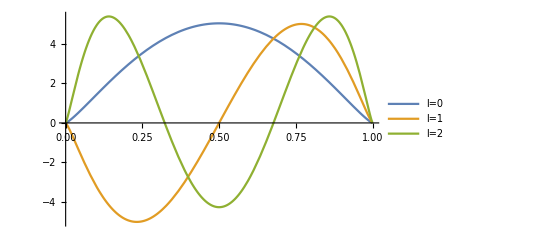

```mathematica
Plot[{χ[0,x],χ[1,x], χ[2,x]},{x,0,1},PlotLegends->{"l=0","l=1", "l=2"}]
```

```mathematica
ϕmom[n_,m_,q_]:=KAPPA^-1 √((4π (n!))/((n+Abs[m])!))(q/KAPPA)^Abs[m] Exp[-q^2/(2 KAPPA^2)]LaguerreL[n,Abs[m], q^2/KAPPA^2];
ϕmomAngle[m_,θ_]:=Exp[ⅈ m θ]

(*ϕmomFull[n_,m_,q_,θ_]:=ϕmom[n,m,q] ϕmomAngle[m,θ]*)

ϕpos[n_,m_,ρ_]:=If[ρ==0 && m == 0, 
KAPPA √(1/π),
KAPPA √((n!)/(π(n+Abs[m])!))(KAPPA ρ)^Abs[m] Exp[(-KAPPA^2 ρ^2)/2]LaguerreL[n,Abs[m], KAPPA^2 ρ^2]];
ϕposAngle[n_,m_,θ_]:=(-1)^(n+Abs[m]/2)  Exp[ⅈ m θ ]

(*ϕposFull[n_,m_,ρ_,θ_]:=ϕpos[n,m,ρ] ϕposAngle[n,m,θ]*)
```

```mathematica
LaguerreL[9,0, 0]
```

1

```mathematica
ϕposAngle[0,0,π/2]
```

1

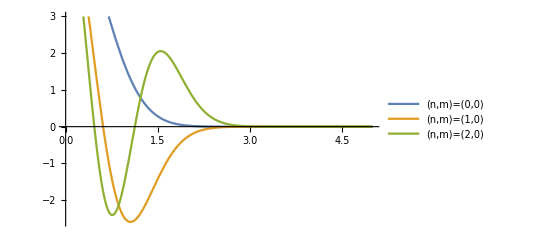

```mathematica
Plot[{ϕmom[0,0,q],ϕmom[1,0,q], ϕmom[2,0,q]},{q,0,5},PlotLegends->{"(n,m)=(0,0)","(n,m)=(1,0)", "(n,m)=(2,0)"}]
```

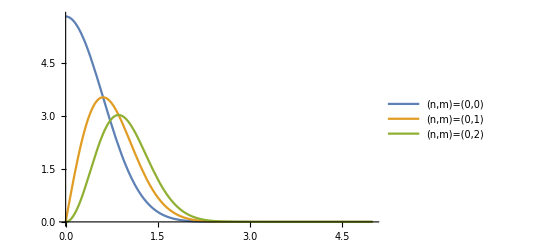

```mathematica
Plot[{ϕmom[0,0,q],ϕmom[0,1,q], ϕmom[0,2,q]},{q,0,5},PlotLegends->{"(n,m)=(0,0)","(n,m)=(0,1)", "(n,m)=(0,2)"}]
```

```mathematica
ϕpos[0,0,0.1]
```

0.343516

## LFWF in Momentum space:

```mathematica
LFWFmomBasis[k_,x_,{n_,m_,l_}]:=ϕmom[n,m,k/√(x(1-x))]χ[l,x]
LFWFmomBasisFull[k_,x_,θ_,{n_,m_,l_}]:=ϕmom[n,m,k/√(x(1-x))]χ[l,x ] ϕmomAngle[m,θ]
```

## LFWF in Position space:

1 fm^-1 = 197.3 MeV, 1 GeV = 5.068 fm^-1 => 1 GeV^-1 = (1/5.068) fm

```mathematica
CartesianToAngle[x_,y_]:=Module[{θ},
θ=Arg[x+ⅈ y] *180/π;
If[θ<0,θ+360,θ]
]
CartesianToRadian[x_,y_]:=Module[{θ},
θ=Arg[x+ⅈ y] ;
If[θ<0,θ+2π,θ]
]
With[{r=1.99},
TableForm[Table[
x =r*Cos[θ/180.*π];
y=r*Sin[θ/180.*π];
{x, y,CartesianToAngle[x,y],CartesianToRadian[x,y]},
{θ,0,360,10}],TableHeadings->{{},{"x","y","θ","Rad"}}]
]
```

| x | y | θ | Rad
 | 1.99 | 0. | 0. | 0.
 | 1.95977 | 0.34556 | 10. | 0.174533
 | 1.86999 | 0.68062 | 20. | 0.349066
 | 1.72339 | 0.995 | 30. | 0.523599
 | 1.52443 | 1.27915 | 40. | 0.698132
 | 1.27915 | 1.52443 | 50. | 0.872665
 | 0.995 | 1.72339 | 60. | 1.0472
 | 0.68062 | 1.86999 | 70. | 1.22173
 | 0.34556 | 1.95977 | 80. | 1.39626
 | 1.21852×10^-16 | 1.99 | 90. | 1.5708
 | -0.34556 | 1.95977 | 100. | 1.74533
 | -0.68062 | 1.86999 | 110. | 1.91986
 | -0.995 | 1.72339 | 120. | 2.0944
 | -1.27915 | 1.52443 | 130. | 2.26893
 | -1.52443 | 1.27915 | 140. | 2.44346
 | -1.72339 | 0.995 | 150. | 2.61799
 | -1.86999 | 0.68062 | 160. | 2.79253
 | -1.95977 | 0.34556 | 170. | 2.96706
 | -1.99 | 2.43705×10^-16 | 180. | 3.14159
 | -1.95977 | -0.34556 | 190. | 3.31613
 | -1.86999 | -0.68062 | 200. | 3.49066
 | -1.72339 | -0.995 | 210. | 3.66519
 | -1.52443 | -1.27915 | 220. | 3.83972
 | -1.27915 | -1.52443 | 230. | 4.01426
 | -0.995 | -1.72339 | 240. | 4.18879
 | -0.68062 | -1.86999 | 250. | 4.36332
 | -0.34556 | -1.95977 | 260. | 4.53786
 | -3.65557×10^-16 | -1.99 | 270. | 4.71239
 | 0.34556 | -1.95977 | 280. | 4.88692
 | 0.68062 | -1.86999 | 290. | 5.06145
 | 0.995 | -1.72339 | 300. | 5.23599
 | 1.27915 | -1.52443 | 310. | 5.41052
 | 1.52443 | -1.27915 | 320. | 5.58505
 | 1.72339 | -0.995 | 330. | 5.75959
 | 1.86999 | -0.68062 | 340. | 5.93412
 | 1.95977 | -0.34556 | 350. | 6.10865
 | 1.99 | -4.87409×10^-16 | 360. | 6.28319

```mathematica
Clear[LFWFposBasis,LFWFposBasisFull,LFWFposBasisFullbyRxRy];
Clear[LFWFposSquaredbySpin,LFWFposSquared];

LFWFposBasis[r_,x_,{n_,m_,l_}]:=√(x(1-x))  ϕposAngle[n,m,0]ϕpos[n,m,√(x(1-x))r]χ[l,x]; (* angle = 0 *)
LFWFposBasisFull[r_,x_,θ_,{n_,m_,l_}]:=If[x==0 ||x==1, 0,√(x(1-x))  ϕposAngle[n,m,θ]ϕpos[n,m,√(x(1-x))r]χ[l,x]]; (* with specified angle *)
LFWFposBasisFullbyRxRy[rx_,ry_,x_,{n_,m_,l_}]:=LFWFposBasisFull[Sqrt[rx^2+ry^2],x,CartesianToRadian[rx,ry],{n,m,l}]
LFWFposSquaredbySpin[rx_,ry_,x_,{s1_,s2_},topk_:100,mj_:0,hadron_:1]:=Module[{bs,data,val,n,r,θ,amp},
data=state[mj,hadron];
bs=Sort[coeffspin[data,{s1,s2}],Abs[#1[[6]]]≥Abs[#2[[6]]]&][[1;;topk]];
amp=Sum[bs[[i,6]]*LFWFposBasisFullbyRxRy[rx,ry, x,{bs[[i,1]],bs[[i,2]],bs[[i,3]]}],{i,1, Length[bs]}];
Abs[amp]^2
]

LFWFposSquared[rx_,ry_,x_,topk_:100,mj_:0,hadron_:1]:=Module[{s11,s1m1,sm11,sm1m1},
s11=LFWFposSquaredbySpin[rx,ry,x,{1,1},topk,mj,hadron];
s1m1=LFWFposSquaredbySpin[rx,ry,x,{1,-1},topk,mj,hadron];
sm11=LFWFposSquaredbySpin[rx,ry,x,{-1,1},topk,mj,hadron];
sm1m1=LFWFposSquaredbySpin[rx,ry,x,{-1,-1},topk,mj,hadron];
s11+s1m1+sm11+sm1m1
]
PrintLFWFposSquaredbySpin[rx_,ry_,x_,{s1_,s2_},topk_:100,mj_:0,hadron_:1]:=Module[{bs,data,val,n,r,θ,amp},
data=state[mj,hadron];
bs=Sort[coeffspin[data,{s1,s2}],Abs[#1[[6]]]≥Abs[#2[[6]]]&][[1;;topk]];
bs
]
PrintLFWFposSquared[rx_,ry_,x_,topk_:100,mj_:0,hadron_:1]:=Module[{s11,s1m1,sm11,sm1m1,tableContent},
s11=PrintLFWFposSquaredbySpin[rx,ry,x,{1,1},topk,mj,hadron];
s1m1=PrintLFWFposSquaredbySpin[rx,ry,x,{1,-1},topk,mj,hadron];
sm11=PrintLFWFposSquaredbySpin[rx,ry,x,{-1,1},topk,mj,hadron];
sm1m1=PrintLFWFposSquaredbySpin[rx,ry,x,{-1,-1},topk,mj,hadron];
tableContent=Join[s11,s1m1,sm11,sm1m1];
TableForm[ tableContent, TableHeadings-> {None,{"n","m", "l", "s_1", "s_2", "coeff"}} , TableAlignments->Right]
]

(*checkNorm[lfwfsquareInterp_]:=Module[{rx, ry, x},
NIntegrate[lfwfsquareInterp[rx,ry,x],{rx,-10,10},{ry,-10,10},{x,0,1}]/4/π
]

CRadius1[{n_,m_,l_}]:=Module[{radius},
radius=(2π)3/2(1/(4π))NIntegrate[(Abs[LFWFposBasisFull[r, x,0,{n,m,l}]]^2)*r^3(1-x)^2,{r, 0, Infinity},{x,0,1}];
Sqrt[radius]/5.068
]
CRadius2[{n_,m_,l_}]:=Module[{radius},
radius=3/2(1/(4π))NIntegrate[(Abs[LFWFposBasisFullbyRxRy[rx, ry,x,{n,m,l}]]^2)*(rx^2+ry^2)(1-x)^2,{rx, -Infinity, Infinity},{ry, -Infinity, Infinity},{x,0,1}];
Sqrt[radius]/5.068
]
CRadiusWithAngle[{n_,m_,l_}]:=Module[{radius},
radius=3/2(1/(4π))NIntegrate[(Abs[LFWFposBasisFull[r, x,t,{n,m,l}]]^2)*r^3(1-x)^2,{r, 0, Infinity},{t,0,2π},{x,0,1}];
Sqrt[radius]/5.068
]
CRadius3[{n_,m_,l_}]:=CRadiusWithAngle[{n,m,l}]*)
```

```mathematica
PrintLFWFposSquared[-0.1,0.9,0.6,1]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
0 | 0 | 0 | 1 | -1 | 0.442466
0 | 0 | 0 | -1 | 1 | -0.442466
0 | 1 | 0 | -1 | -1 | -0.29865

```mathematica
LFWFcoeffSquare[{s1_,s2_},topk_:100,mj_:0,hadron_:1]:=Module[{bs,data,val,n,r,θ,prob},
data=state[mj,hadron];
bs=Sort[coeffspin[data,{s1,s2}],Abs[#1[[6]]]≥Abs[#2[[6]]]&][[1;;topk]];
prob=Sum[bs[[i,6]]^2,{i,1, Length[bs]}]
]
LFWFcoeffSquareTotal[topk_:100,mj_:0,hadron_:1]:=Module[{s11,s1m1,sm11,sm1m1},
s11=LFWFcoeffSquare[{1,1},topk,mj,hadron];
s1m1=LFWFcoeffSquare[{1,-1},topk,mj,hadron];
sm11=LFWFcoeffSquare[{-1,1},topk,mj,hadron];
sm1m1=LFWFcoeffSquare[{-1,-1},topk,mj,hadron];
{s11,s1m1,sm11,sm1m1, s11+s1m1+sm11+sm1m1}
]
LFWFcoeffSquareTotal[5]
LFWFcoeffSquareTotal[25]
LFWFcoeffSquareTotal[50]
LFWFcoeffSquareTotal[100]
```

{0.176192,0.296154,0.296154,0.176192,0.944694}

{0.185501,0.314408,0.314408,0.185501,0.999817}

{0.18551,0.31449,0.31449,0.18551,0.999999}

{0.18551,0.31449,0.31449,0.18551,1.}

```mathematica
LFWFposSquaredbySpin[-0.1,0.9,0.6,{1,-1},100]
```

0.29492

```mathematica
LFWFposSquared[-0.1,0.9,0.6,50]
```

0.65858

```mathematica
Flatten[Table[{rx,x,Abs[LFWFposBasisFull[rx,x,0,{0,0,0}]]^2}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1]
```

{{-10.,0.,0},{-10.,0.01,6.96124×10^-6},{-10.,0.02,0.0000521449},{-10.,0.03,0.000144687},{-10.,0.04,0.000268457},{-10.,0.05,0.000400811},{-10.,0.06,0.000522914},{-10.,0.07,0.000622939},{-10.,0.08,0.00069564},{-10.,0.09,0.000740625},20282,{10.,0.92,0.00069564},{10.,0.93,0.000622939},{10.,0.94,0.000522914},{10.,0.95,0.000400811},{10.,0.96,0.000268457},{10.,0.97,0.000144687},{10.,0.98,0.0000521449},{10.,0.99,6.96124×10^-6},{10.,1.,0}}
 |  |  |  |

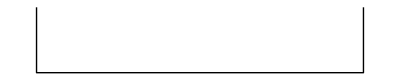

```mathematica
ScaleGraphics[length_,ticksize_]:=Graphics[{Thick,Line[{{0,0.5+ticksize},{0,0.5},{length,0.5},{length,0.5+ticksize}}]}]
ScaleGraphics[0.46938012112625566*5.068,0.02]
```

### Pion (0, 0, 0)

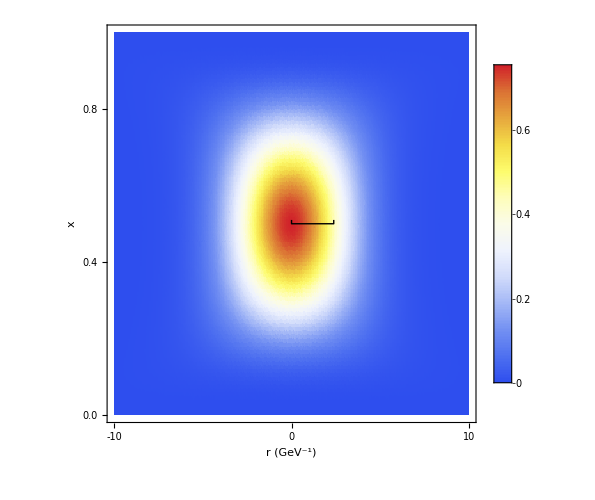

```mathematica
dataList = Flatten[Table[{r,x,Abs[LFWFposBasisFull[r,x,0,{0,0,0}]]^2}, {r,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[
ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.46938012112625566*5.068,0.01]
]
```

```mathematica
nml={0,0,0};
Print["CRadius1 = ", CRadius1[nml], " fm"]; (* 2D integral, using (r, x) with theta = 0, or anything*)
Print["CRadius2 = ", CRadius2[nml], " fm"]; (* 3D integral, using (rx, ry, x) *)
Print["CRadius3 = ", CRadiusWithAngle[nml], " fm"];(* 3D integral,using (r, x, t) *)
Clear[nml]
```

CRadius1 = 0.46938 fm

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

CRadius2 = 0.46938 fm

CRadius3 = 0.46938 fm

```mathematica
Export[ToFileName[{cwd},"Pion_LFWFSquare_000_with_radius.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\Pion_LFWFSquare_000_with_radius.pdf

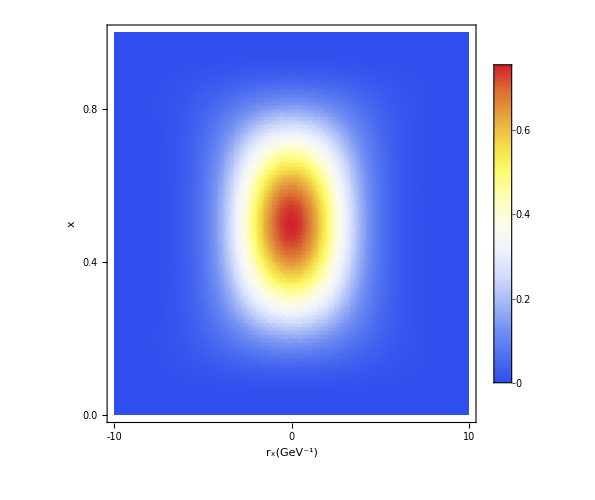

```mathematica
(* Proving it is same to plot (rx, ry=0, x) or (|r|, x)*)
dataList = Flatten[Table[{rx,x,Abs[LFWFposBasisFullbyRxRy[rx,0,x,{0,0,0}]]^2}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r_x(GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0]
```

### Pion (0, 1, 0)

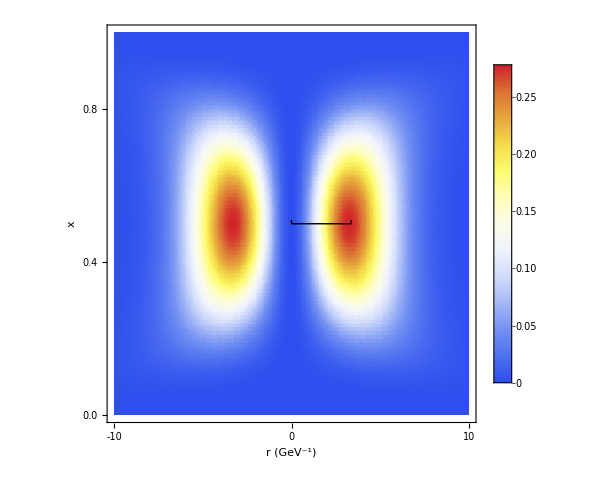

```mathematica
dataList = Flatten[Table[{r,x,Abs[LFWFposBasisFull[r,x,0,{0,1,0}]]^2}, {r,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[
ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.6638033249769942*5.068,0.01]
]
```

```mathematica
nml={0,1,0};
Print["CRadius1 = ", CRadius1[nml], " fm"]; (* 2D integral, using (r, x) with theta = 0, or anything*)
Print["CRadius2 = ", CRadius2[nml], " fm"]; (* 3D integral, using (rx, ry, x) *)
Print["CRadius3 = ", CRadiusWithAngle[nml], " fm"];(* 3D integral,using (r, x, t) *)
Clear[nml]
```

CRadius1 = 0.663803 fm

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

CRadius2 = 0.663804 fm

CRadius3 = 0.663803 fm

```mathematica
Export[ToFileName[{cwd},"Pion_LFWFSquare_010_with_radius.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\Pion_LFWFSquare_010_with_radius.pdf

### Pion (1, 0, 0)

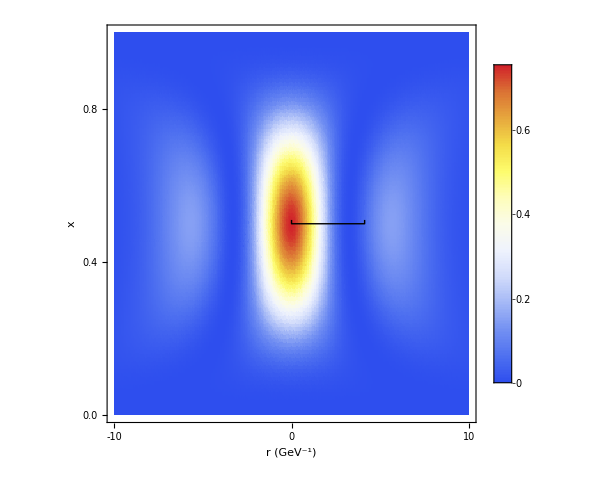

```mathematica
dataList = Flatten[Table[{r,x,Abs[LFWFposBasisFull[r,x,0,{1,0,0}]]^2}, {r,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[
ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.8129903164137553*5.068,0.01]
]
```

```mathematica
nml={1,0,0};
Print["CRadius1 = ", CRadius1[nml], " fm"]; (* 2D integral, using (r, x) with theta = 0, or anything*)
Print["CRadius2 = ", CRadius2[nml], " fm"]; (* 3D integral, using (rx, ry, x) *)
Print["CRadius3 = ", CRadiusWithAngle[nml], " fm"];(* 3D integral,using (r, x, t) *)
Clear[nml]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

CRadius1 = 0.81299 fm

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

CRadius2 = 0.81299 fm

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

CRadius3 = 0.81299 fm

```mathematica
Export[ToFileName[{cwd},"Pion_LFWFSquare_100_with_radius.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\Pion_LFWFSquare_100_with_radius.pdf

### Full Pion (testing)

```mathematica
cwd
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\LFWF_data\

```mathematica
summedFullLFWFdata=<<(ToFileName[{cwd},"summed_LFWF_squared_4080501points.dat"])
```

{1}
 |  |  |  |

```mathematica
summedFullLFWFinterp=Interpolation[Flatten[summedFullLFWFdata,2], Method->"Hermite", InterpolationOrder->3] (* this is sufficient *)
```

InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 1.}}, <>]

```mathematica
summedFullLFWFinterp[0.1,0.1,0.5]
```

0.738193

```mathematica
summedFullLFWFinterp2=Interpolation[Flatten[summedFullLFWFdata,2], Method->"Hermite", InterpolationOrder->10]
```

InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 1.}}, <>]

```mathematica
summedFullLFWFinterp2[0.1,0.1,0.5]
```

0.738193

```mathematica
summedFullLFWFinterp
```

InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 1.}}, <>]

```mathematica
summedFullLFWFinterp[-15,-15,0.2]
```

InterpolatingFunction::dmval: Input value {-15,-15,0.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

-2.34009×10^-11

```mathematica
CRadiusOfInterp[interpFunc_]:=Module[{radius},
radius=3/2(1/(4π))NIntegrate[(summedFullLFWFinterp[rx, ry, x])*(rx^2+ry^2)(1-x)^2,{rx, -10, 10},{ry, -10, 10},{x,0,1}];
Sqrt[radius]/5.068
]
CRadiusOfInterp2[interpFunc_]:=Module[{radius},
radius=3/2(1/(4π))(2π)NIntegrate[(summedFullLFWFinterp[r, 0, x])*r^3(1-x)^2,{r, -10, 10},{x,0,1}];
Sqrt[radius]/5.068
]
CRadiusOfInterp3[interpFunc_]:=Module[{radius},
radius=3/2(1/(4π))NIntegrate[(summedFullLFWFinterp[rx, ry, x])*(rx^2+ry^2)(1-x)^2,{rx, -Infinity, Infinity},{ry, -Infinity, Infinity},{x,0,1}];
Sqrt[radius]/5.068
]
```

```mathematica
CRadiusOfInterp[summedFullLFWFinterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.7584 and 0.000202464 for the integral and error estimates.

0.396091

```mathematica
CRadiusOfInterp2[summedFullLFWFinterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.21309×10^-10 and 1.71896×10^-6 for the integral and error estimates.

2.54211×10^-6

```mathematica
CRadiusOfInterp3[summedFullLFWFinterp]
```

NIntegrate::inumr: The integrand (Power[rx, 2] + Power[ry, 2]) Power[1 - x, 2] InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 1.}}, <>][rx, ry, x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{0.,-4.0247×10^31},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

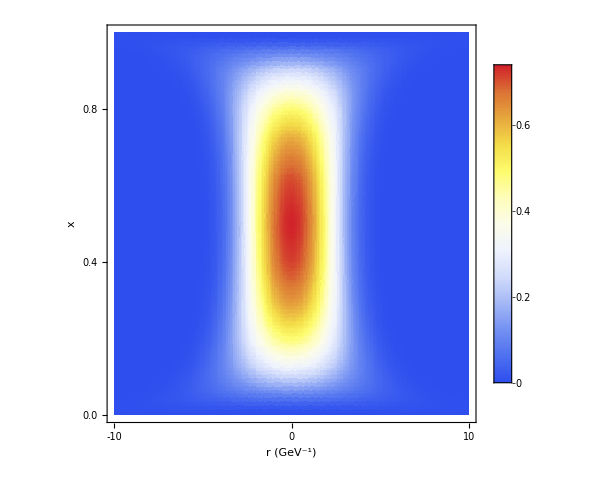

```mathematica
(* InterpolationOrder->0 *)
dataList = Flatten[Table[{rx,x,summedFullLFWFinterp2[rx,0,x]}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1];
(*dataListInterp =Interpolation[dataList];*)
plotResult = ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->0,PlotRangePadding->0]
```

```mathematica
Export[ToFileName[{cwd},"Pion_LFWFSquare_Full_Interpolation_0.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\LFWF_data\Pion_LFWFSquare_Full_Interpolation_0.pdf

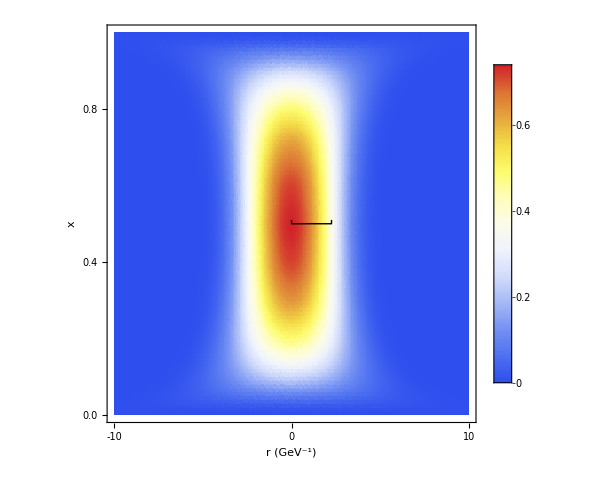

```mathematica
dataList = Flatten[Table[{rx,x,summedFullLFWFinterp[rx,0,x]}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1];
(*dataListInterp =Interpolation[dataList];*)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.444486*5.068,0.01]
]
```

```mathematica
Export[ToFileName[{cwd},"Pion_LFWFSquare_Full_with_radius0p44.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\Pion_LFWFSquare_Full_with_radius0p44.pdf

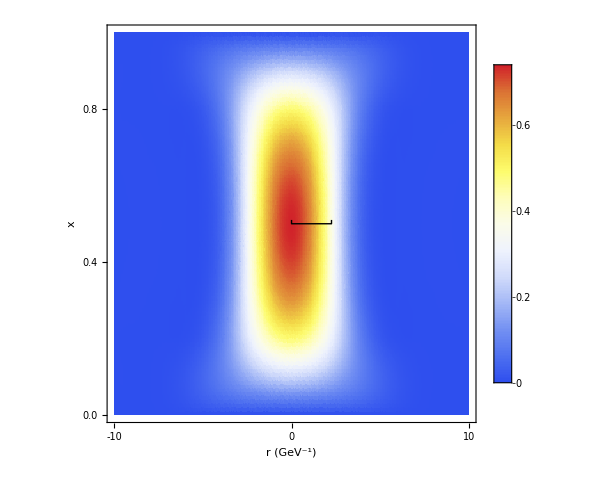

```mathematica
(*testing*)
dataList = Flatten[Table[{rx,x,interp1[rx,0,x]}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.444486*5.068,0.01]
]
```

```mathematica
LFWFposSquared[-5,5,0.1]
```

0.00262038

### Charmonium J/Ψ (0,0,0)

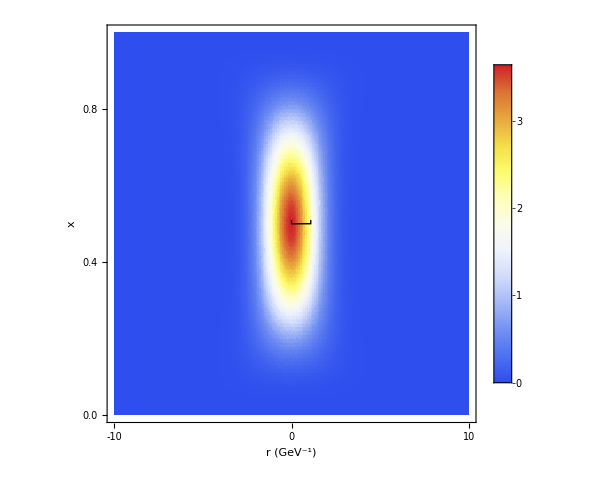

```mathematica
KAPPA=1.34;QUARK=1.27;
dataList = Flatten[Table[{r,x,Abs[LFWFposBasisFull[r,x,0,{0,0,0}]]^2}, {r,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.213673*5.068,0.01]
]
```

```mathematica
nml={0,0,0};
Print["CRadius1 = ", CRadius1[nml], " fm"]; (* 2D integral, using (r, x) with theta = 0, or anything*)
Print["CRadius2 = ", CRadius2[nml], " fm"]; (* 3D integral, using (rx, ry, x) *)
Print["CRadius3 = ", CRadiusWithAngle[nml], " fm"];(* 3D integral,using (r, x, t) *)
Clear[nml]
```

CRadius1 = 0.213673 fm

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

CRadius2 = 0.213673 fm

CRadius3 = 0.213673 fm

```mathematica
Export[ToFileName[{cwd},"JPsi_LFWFSquare_000_with_radius.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\JPsi_LFWFSquare_000_with_radius.pdf

### Charmonium (0,0,0)

```mathematica
KAPPA=0.985;QUARK=1.570;
dataList = Flatten[Table[{r,x,Abs[LFWFposBasisFull[r,x,0,{0,0,0}]]^2}, {r,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.290682*5.068,0.01]
]
```

-Graphics-

```mathematica
nml={0,0,0};
Print["CRadius1 = ", CRadius1[nml], " fm"]; (* 2D integral, using (r, x) with theta = 0, or anything*)
Print["CRadius2 = ", CRadius2[nml], " fm"]; (* 3D integral, using (rx, ry, x) *)
Print["CRadius3 = ", CRadiusWithAngle[nml], " fm"];(* 3D integral,using (r, x, t) *)
Clear[nml]
```

CRadius1 = 0.290682 fm

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

CRadius2 = 0.290682 fm

CRadius3 = 0.290682 fm

```mathematica
Export[ToFileName[{cwd},"Charmonium_eta_c_LFWFSquare_000_with_radius.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\Charmonium_eta_c_LFWFSquare_000_with_radius.pdf

### Bottomonium (0,0,0)

```mathematica
KAPPA=1.387;QUARK=4.894;
dataList = Flatten[Table[{r,x,Abs[LFWFposBasisFull[r,x,0,{0,0,0}]]^2}, {r,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.206433*5.068,0.01]
]
```

-Graphics-

```mathematica
nml={0,0,0};
Print["CRadius1 = ", CRadius1[nml], " fm"]; (* 2D integral, using (r, x) with theta = 0, or anything*)
Print["CRadius2 = ", CRadius2[nml], " fm"]; (* 3D integral, using (rx, ry, x) *)
Print["CRadius3 = ", CRadiusWithAngle[nml], " fm"];(* 3D integral,using (r, x, t) *)
Clear[nml]
```

CRadius1 = 0.206433 fm

CRadius2 = 0.206433 fm

CRadius3 = 0.206433 fm

```mathematica
Export[ToFileName[{cwd},"Bottomium_eta_b_LFWFSquare_000_with_radius.pdf"],plotResult]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\Bottomium_eta_b_LFWFSquare_000_with_radius.pdf

```mathematica
Grids 1: 21  x 21 x 11
```

## Rotational symmetry, θ-free spin sum

```mathematica
With[{r=1.99, x=0.5},
TableForm[Table[
rx =r*Cos[θ/180.*π];
ry=r*Sin[θ/180.*π];
spinsum=LFWFposSquared[rx, ry, x];
{θ,spinsum},
{θ,0,360,10}],TableHeadings->{{},{"θ","Spin Sum"}}]
]
```

| θ | Spin Sum
 | 0 | 0.452614
 | 10 | 0.452614
 | 20 | 0.452614
 | 30 | 0.452614
 | 40 | 0.452614
 | 50 | 0.452614
 | 60 | 0.452614
 | 70 | 0.452614
 | 80 | 0.452614
 | 90 | 0.452614
 | 100 | 0.452614
 | 110 | 0.452614
 | 120 | 0.452614
 | 130 | 0.452614
 | 140 | 0.452614
 | 150 | 0.452614
 | 160 | 0.452614
 | 170 | 0.452614
 | 180 | 0.452614
 | 190 | 0.452614
 | 200 | 0.452614
 | 210 | 0.452614
 | 220 | 0.452614
 | 230 | 0.452614
 | 240 | 0.452614
 | 250 | 0.452614
 | 260 | 0.452614
 | 270 | 0.452614
 | 280 | 0.452614
 | 290 | 0.452614
 | 300 | 0.452614
 | 310 | 0.452614
 | 320 | 0.452614
 | 330 | 0.452614
 | 340 | 0.452614
 | 350 | 0.452614
 | 360 | 0.452614

## Grid-1: 21 x 21 x 11 = 4851

```mathematica
rxMin=-10; rxMax=10;rxStep=1;
ryMin=-10; ryMax=10; ryStep=1;
xMin=0.0;xMax=1.0;xStep=0.1;
```

```mathematica
t0=AbsoluteTime[];
lfwfSquareList=ParallelTable[t=LFWFposSquared[rx, ry, x];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Elapsed time: 12.415084s

```mathematica
flattenList1 = Flatten[lfwfSquareList,2];
interp1 = Interpolation[Flatten[lfwfSquareList,2], Method->"Hermite", InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
dataList = Flatten[Table[{rx,x,interp1[rx,0,x]}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
flattenList1>>cwd<>"LFWFSpinSumSquared_4851pts.dat"
```

```mathematica
importedList=<<(cwd<>"LFWFSpinSumSquared_4851pts.dat");
importedList==flattenList1
```

True

## Grid-2: 201 x 201 x 101 = 4.1 million

```mathematica
rxMin=-10; rxMax=10;rxStep=0.1;
ryMin=-10; ryMax=10; ryStep=0.1;
xMin=0.0;xMax=1.0;xStep=0.01;
```

```mathematica
(*Apparently it is faster to do it by spins then sum*)
```

```mathematica
t0=AbsoluteTime[];
lfwfSquareList11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Elapsed time: 4478.916774s

```mathematica
t0=AbsoluteTime[];
lfwfSquareList1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,-1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Elapsed time: 3977.007959s

```mathematica
t0=AbsoluteTime[];
lfwfSquareListm11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{-1,1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Elapsed time: 3943.273932s

```mathematica
t0=AbsoluteTime[];
lfwfSquareListm1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{-1,-1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Elapsed time: 4457.730331s

```mathematica
Dimensions[Flatten[lfwfSquareListm1m1,2]]
```

{4080501,2}

```mathematica
(*Summing L1 distance, proving identical spin parts as expected*)
```

```mathematica
Sum[Abs[lfwfSquareList1m1[[r1,r2,xi,2]]-lfwfSquareListm11[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]
```

9.2057×10^-10

```mathematica
Sum[Abs[lfwfSquareList11[[r1,r2,xi,2]]-lfwfSquareListm1m1[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]
```

3.24257×10^-11

```mathematica
(*Exporting both by spins and by sums*)
```

```mathematica
lfwfSquareList11>>cwd<>"LFWFSumSquared_Spin11_4080501pts.dat"
```

```mathematica
lfwfSquareList1m1>>cwd<>"LFWFSumSquared_Spin1m1_4080501pts.dat"
```

```mathematica
lfwfSquareListm11>>cwd<>"LFWFSumSquared_Spinm11_4080501pts.dat"
```

```mathematica
lfwfSquareListm1m1>>cwd<>"LFWFSumSquared_Spinm1m1_4080501pts.dat"
```

```mathematica
GetSummedLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList11[[r1,r2,xi,1]],
Assert[lfwfSquareList11[[r1,r2,xi,1]]==lfwfSquareList1m1[[r1,r2,xi,1]]];
Assert[lfwfSquareList1m1[[r1,r2,xi,1]]==lfwfSquareListm11[[r1,r2,xi,1]]];
Assert[lfwfSquareListm11[[r1,r2,xi,1]]==lfwfSquareListm1m1[[r1,r2,xi,1]]];
lfwfSquareList11[[r1,r2,xi,2]]+
lfwfSquareList1m1[[r1,r2,xi,2]]+
lfwfSquareListm11[[r1,r2,xi,2]]+
lfwfSquareListm1m1[[r1,r2,xi,2]]}
```

```mathematica
(*lfwfSquareList11[[133,133,49]]
lfwfSquareList1m1[[133,133,49]]
lfwfSquareListm11[[133,133,49]]
lfwfSquareListm1m1[[133,133,49]]
lfwfSquareList11[[133,133,49]]+lfwfSquareList1m1[[133,133,49]]+lfwfSquareListm11[[133,133,49]]+lfwfSquareListm1m1[[133,133,49]]
GetSummedLFWFSquare[133,133,49]*)
```

```mathematica
Dimensions[lfwfSquareListm1m1]
```

{201,201,101,2}

```mathematica
LFWFSpinSumSquareListGrid2=Table[GetSummedLFWFSquare[r1,r2,xi],{r1, 1, 201},{r2,1,201},{xi,1,101}]
```

```mathematica
LFWFSpinSumSquareListGrid2>>cwd<>"LFWFSpinSumSquared_4080501pts.dat"
```

```mathematica
Flatten[LFWFSpinSumSquareListGrid2,2][[1555]]
```

{{-10.,-8.5,0.39},0.000161925}

```mathematica
(*this shows previous data is confirmed to be correct*)
Sum[Abs[thisData[[r1,r2,xi,2]]-prevData[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]
```

3.33648×10^-11

### Spin Component Spin Sums

```mathematica
interpData = Interpolation[Flatten[lfwfSquareList11, 2], Method -> "Hermite", InterpolationOrder -> 3]; 
dataList = Flatten[Table[{rx, x, interpData[rx, 0, x]}, {rx, -10, 10, 0.1}, {x, 0, 1., 0.01}], 1]; 
plotResult = Show[ListDensityPlot[dataList, ColorFunction -> "TemperatureMap", LabelStyle -> Directive[Black, 28, AbsoluteThickness[1], FontFamily -> "Times"], 
    FrameLabel -> {Style["r (GeV^-1)", 37], Style["x", 37]}, FrameStyle -> Directive[Black, 28, AbsoluteThickness[1], FontFamily -> "Times"], 
    FrameTicks -> {Table[If[Mod[i, 10] == 0, {0.5*i, IntegerPart[0.5*i], {0, -0.03}}, {0.5*i, Null, {0, -0.02}}], {i, -40, 40, 1}], 
      Table[If[Mod[i, 4] == 0, {0.05*i, NumberForm[0.05*i, {2, 1}], {0, -0.03}}, {0.05*i, Null, {0, -0.02}}], {i, -10, 40, 1}]}, 
    PlotLegends -> BarLegend[Automatic, LegendMarkerSize -> 330], PlotRange -> {{-10, 10}, {0, 1}, All}, Frame -> True, ImageSize -> 500, InterpolationOrder -> 1, 
    PlotRangePadding -> 0, PlotLabel -> "Spin ↑↑ "]]
```

-Graphics-

```mathematica
interpData = Interpolation[Flatten[lfwfSquareList1m1, 2], Method -> "Hermite", InterpolationOrder -> 3];
dataList = Flatten[Table[{rx,x,interpData[rx,0,x]}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin ↑↓ "]
]
```

-Graphics-

### Spin Summed

```mathematica
thisInterp=Interpolation[Flatten[LFWFSpinSumSquareListGrid2,2], Method->"Hermite", InterpolationOrder->3];
dataList = Flatten[Table[{rx,x,thisInterp[rx,0,x]}, {rx,-10,10,0.1},{x,0,1.00,0.01}],1];
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

## Grid-3: 401 x 401 x 101 = 16 mil , All 400 basis

```mathematica
401  * 401 * 101
```

16240901

```mathematica
rxMin=-20; rxMax=20;rxStep=0.1;
ryMin=-20; ryMax=20; ryStep=0.1;
xMin=0.0;xMax=1.0;xStep=0.01;
```

```mathematica
(*Apparently it is faster to do it by spins then sum*)
```

```mathematica
t0=AbsoluteTime[];
lfwfSquareList11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Elapsed time: 9261.427141s

```mathematica
t0=AbsoluteTime[];
lfwfSquareList1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,-1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Elapsed time: 8151.042971s

```mathematica
(*SKIP, same as 1m1 case *)
(*t0=AbsoluteTime[];
lfwfSquareListm11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{-1,1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];*)
```

```mathematica
(*SKIP, same as 11 case *)
(*t0=AbsoluteTime[];
lfwfSquareListm1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{-1,-1}];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];*)
```

```mathematica
Dimensions[Flatten[lfwfSquareListm1m1,2]]
```

```mathematica
(*Summing L1 distance, proving identical spin parts as expected*)
```

```mathematica
(*Sum[Abs[lfwfSquareList1m1[[r1,r2,xi,2]]-lfwfSquareListm11[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*Sum[Abs[lfwfSquareList11[[r1,r2,xi,2]]-lfwfSquareListm1m1[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*Exporting both by spins and by sums*)
```

```mathematica
lfwfSquareList11>>cwd<>"LFWFSumSquared_Spin11_9150701pts.dat"(*DONE!!!!*)
```

```mathematica
lfwfSquareList1m1>>cwd<>"LFWFSumSquared_Spin1m1_9150701pts.dat"
```

```mathematica
(*SKIP *)(*lfwfSquareListm11>>cwd<>"LFWFSumSquared_Spinm11_9150701pts.dat"*)
```

```mathematica
(*SKIP *)(*lfwfSquareListm1m1>>cwd<>"LFWFSumSquared_Spinm1m1_9150701pts.dat"*)
```

```mathematica
GetSummedLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList11[[r1,r2,xi,1]],
Assert[lfwfSquareList11[[r1,r2,xi,1]]==lfwfSquareList1m1[[r1,r2,xi,1]]];
Assert[lfwfSquareList1m1[[r1,r2,xi,1]]==lfwfSquareListm11[[r1,r2,xi,1]]];
Assert[lfwfSquareListm11[[r1,r2,xi,1]]==lfwfSquareListm1m1[[r1,r2,xi,1]]];
lfwfSquareList11[[r1,r2,xi,2]]+
lfwfSquareList1m1[[r1,r2,xi,2]]+
lfwfSquareListm11[[r1,r2,xi,2]]+
lfwfSquareListm1m1[[r1,r2,xi,2]]}
```

```mathematica
(*lfwfSquareList11[[133,133,49]]
lfwfSquareList1m1[[133,133,49]]
lfwfSquareListm11[[133,133,49]]
lfwfSquareListm1m1[[133,133,49]]
lfwfSquareList11[[133,133,49]]+lfwfSquareList1m1[[133,133,49]]+lfwfSquareListm11[[133,133,49]]+lfwfSquareListm1m1[[133,133,49]]
GetSummedLFWFSquare[133,133,49]*)
```

```mathematica
Dimensions[lfwfSquareList1m1]
```

{401,401,101,2}

```mathematica
Dimensions[lfwfSquareListm1m1]
```

```mathematica
LFWFSpinSumSquareListGrid3=Table[GetSummedLFWFSquare[r1,r2,xi],{r1, 1, 401},{r2,1,401},{xi,1,101}]
```

```mathematica
LFWFSpinSumSquareListGrid3>>cwd<>"LFWFSpinSumSquared_9150701pts.dat"
```

## Grid-3: 401 x 401 x 101 = 16 mil , leading 25*4=100 basis

```mathematica
plotdata=Table[LFWFposSquared[-0.1,0.9,0.6,cutoff],{cutoff, 1, 100}]
```

{0.246457,0.562649,0.470684,0.678119,0.596232,0.690191,0.704734,0.652381,0.666449,0.640424,0.649909,0.65739,0.662102,0.667802,0.671165,0.660247,0.651897,0.653431,0.647503,0.656613,0.652986,0.660486,0.665977,0.65942,0.662981,0.657461,0.653249,0.657534,0.661086,0.658344,0.65602,0.658708,0.656704,0.658551,0.659561,0.658028,0.658914,0.657839,0.657679,0.658376,0.658229,0.658719,0.658362,0.658247,0.657962,0.657868,0.658462,0.658238,0.658722,0.65858,0.658952,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243,0.659243}

```mathematica
LFWFposSquared[-0.1,0.9,0.6,25]
```

0.662981

```mathematica
plotdata=Table[LFWFposSquaredbySpin[-0.1,0.9,0.6,{1,1},cutoff],{cutoff, 1, 100}]
```

{0.0039784,0.0159859,0.0317192,0.0469522,0.0433413,0.0392426,0.0356038,0.0327081,0.0330911,0.0335992,0.0341201,0.0345932,0.0347385,0.0348418,0.0349989,0.0351486,0.0349213,0.0346681,0.0345148,0.0342672,0.0344468,0.0346527,0.034772,0.0349795,0.0348581,0.0347179,0.0345763,0.0344977,0.0345705,0.0346552,0.034741,0.0347883,0.0347493,0.0347041,0.0346587,0.0346334,0.0346499,0.0346689,0.0346796,0.0346986,0.0346959,0.0346929,0.0346912,0.0346882,0.0346832,0.0346775,0.0346743,0.0346688,0.034677,0.0346864,0.0346918,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009}

```mathematica
Module[{plotdata,plotdata1,plotdata2,plotdata3,plotdataAll, rx,ry,x},
rx=0;
ry=3.5;
x=0.5;
plotdata=Table[LFWFposSquaredbySpin[rx,ry,x,{1,-1},cutoff],{cutoff, 1, 100}];
(*plotdata1=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,1},cutoff],{cutoff, 1, 100}];*)
(*plotdata2=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,-1},cutoff],{cutoff, 1, 100}];*)
plotdata3=Table[LFWFposSquaredbySpin[rx,ry,x,{1,1},cutoff],{cutoff, 1, 100}];
plotdataAll=Table[LFWFposSquared[rx,ry,x,cutoff],{cutoff, 1, 100}];
ListPlot[{plotdata,plotdata3,plotdataAll},PlotStyle->{Blue, Darker@Green,Red},AxesLabel->{"Num of basis"},PlotLegends->{"|∑ψ_(nml, (1, -1))|^2", "|∑ψ_(nml, (1, 1))|^2", "Full LFWF"}]]
```

-Graphics-

```mathematica
Module[{plotdata,plotdata1,plotdata2,plotdata3,plotdataAll, rx,ry,x},
rx=0;
ry=3.5;
x=0.5;
plotdataAll=Table[LFWFposSquared[rx,ry,x,cutoff],{cutoff, 1, 100}];
ListPlot[{plotdataAll},PlotStyle->{Red},AxesLabel->{"Num of basis"},PlotLegends->{"Full LFWF \n(4 X Num of basis)"}]]
```

-Graphics-

```mathematica
401  * 401 * 101
```

16240901

```mathematica
Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
```

```mathematica
cutoff=25;
rxMin=-20; rxMax=20;rxStep=0.1;
ryMin=-20; ryMax=20; ryStep=0.1;
xMin=0.0;xMax=1.0;xStep=0.01;

numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);
Print["Cutoff = ",cutoff];Print["Num Pts = ",numPts]
```

Cutoff = 25

Num Pts = 1.62409×10^7

```mathematica
(*5043 pts needs 5.8988505 seconds*)
(*Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
cutoff=25;
rxMin=-20; rxMax=20;rxStep=1;
ryMin=-20; ryMax=20; ryStep=1;
xMin=0.0;xMax=1.0;xStep=0.5;
numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1)*)
(*Estimation*)
5.8988505/5043*16240901/60/60. (*hr*)
```

5.27699

```mathematica
(*Apparently it is faster to do it by spins then sum*)
```

```mathematica
t0=AbsoluteTime[];
lfwfSquareList11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1},cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

{1}
 |  |  |  |

Elapsed time: 29603.5251797s

```mathematica
lfwfSquareList11>>cwd<>"LFWFSumSquared_Spin11_16Mpts_top100.dat"
```

```mathematica
t0=AbsoluteTime[];
lfwfSquareList1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,-1}, cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

{1}
 |  |  |  |

Elapsed time: 29912.7471631s

```mathematica
lfwfSquareList1m1>>cwd<>"LFWFSumSquared_Spin1m1_16Mpts_top100.dat"
```

```mathematica
(*Need to verify*)
```

```mathematica
t0=AbsoluteTime[];
GetSummedLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList11[[r1,r2,xi,1]],
Assert[lfwfSquareList11[[r1,r2,xi,1]]==lfwfSquareList1m1[[r1,r2,xi,1]]];
(*Assert[lfwfSquareList1m1[[r1,r2,xi,1]]==lfwfSquareListm11[[r1,r2,xi,1]]];
Assert[lfwfSquareListm11[[r1,r2,xi,1]]==lfwfSquareListm1m1[[r1,r2,xi,1]]];*)
2*lfwfSquareList11[[r1,r2,xi,2]]+
2*lfwfSquareList1m1[[r1,r2,xi,2]]
}
LFWFSpinSumSquareListGrid3Top100=Table[GetSummedLFWFSquare[r1,r2,xi],{r1, 1, 401},{r2,1,401},{xi,1,101}];
LFWFSpinSumSquareListGrid3Top100>>cwd<>"LFWFSpinSumSquared_16Mpts_top100_trial2.dat";
timeSince[t0];
```

Elapsed time: 312.6247420s

```mathematica
Dimensions[LFWFSpinSumSquareListGrid3Top100]
```

{401,401,101,2}

```mathematica
Dimensions[Flatten[lfwfSquareList11,2]]
```

{16240901,2}

```mathematica
(*Summing L1 distance, proving identical spin parts as expected*)
```

```mathematica
(*Sum[Abs[lfwfSquareList1m1[[r1,r2,xi,2]]-lfwfSquareListm11[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*Sum[Abs[lfwfSquareList11[[r1,r2,xi,2]]-lfwfSquareListm1m1[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*SKIP *)(*lfwfSquareListm1m1>>cwd<>"LFWFSumSquared_Spinm1m1_9150701pts.dat"*)
```

```mathematica
Dimensions[lfwfSquareList1m1]
```

{401,401,101,2}

## Grid-3: 401 x 401 x 101 = 16 mil , leading 15*4=60 basis

```mathematica
plotdata=Table[LFWFposSquared[-0.1,0.9,0.6,cutoff],{cutoff, 1, 15}]
```

{0.246457,0.562649,0.470684,0.678119,0.596232,0.690191,0.704734,0.652381,0.666449,0.640424,0.649909,0.65739,0.662102,0.667802,0.671165}

```mathematica
LFWFposSquared[-0.1,0.9,0.6,15]
```

0.671165

```mathematica
plotdata=Table[LFWFposSquaredbySpin[-0.1,0.9,0.6,{1,1},cutoff],{cutoff, 1, 100}]
```

{0.0039784,0.0159859,0.0317192,0.0469522,0.0433413,0.0392426,0.0356038,0.0327081,0.0330911,0.0335992,0.0341201,0.0345932,0.0347385,0.0348418,0.0349989,0.0351486,0.0349213,0.0346681,0.0345148,0.0342672,0.0344468,0.0346527,0.034772,0.0349795,0.0348581,0.0347179,0.0345763,0.0344977,0.0345705,0.0346552,0.034741,0.0347883,0.0347493,0.0347041,0.0346587,0.0346334,0.0346499,0.0346689,0.0346796,0.0346986,0.0346959,0.0346929,0.0346912,0.0346882,0.0346832,0.0346775,0.0346743,0.0346688,0.034677,0.0346864,0.0346918,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009}

```mathematica
Module[{plotdata,plotdata1,plotdata2,plotdata3,plotdataAll, rx,ry,x},
rx=0;
ry=3.5;
x=0.5;
plotdata=Table[LFWFposSquaredbySpin[rx,ry,x,{1,-1},cutoff],{cutoff, 1, 100}];
(*plotdata1=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,1},cutoff],{cutoff, 1, 100}];*)
(*plotdata2=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,-1},cutoff],{cutoff, 1, 100}];*)
plotdata3=Table[LFWFposSquaredbySpin[rx,ry,x,{1,1},cutoff],{cutoff, 1, 100}];
plotdataAll=Table[LFWFposSquared[rx,ry,x,cutoff],{cutoff, 1, 100}];
ListPlot[{plotdata,plotdata3,plotdataAll},PlotStyle->{Blue, Darker@Green,Red},AxesLabel->{"Num of basis"},PlotLegends->{"|∑ψ_(nml, (1, -1))|^2", "|∑ψ_(nml, (1, 1))|^2", "Full LFWF"}]]
```

-Graphics-

```mathematica
Module[{plotdata,plotdata1,plotdata2,plotdata3,plotdataAll, rx,ry,x},
rx=0;
ry=3.5;
x=0.5;
plotdataAll=Table[LFWFposSquared[rx,ry,x,cutoff],{cutoff, 1, 100}];
ListPlot[{plotdataAll},PlotStyle->{Red},AxesLabel->{"Num of basis"},PlotLegends->{"Full LFWF \n(4 X Num of basis)"}]]
```

-Graphics-

```mathematica
401  * 401 * 101
```

16240901

```mathematica
Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
```

```mathematica
cutoff=15;
rxMin=-20; rxMax=20;rxStep=0.1;
ryMin=-20; ryMax=20; ryStep=0.1;
xMin=0.0;xMax=1.0;xStep=0.01;

numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);
Print["Cutoff = ",cutoff];Print["Num Pts = ",numPts]
```

Cutoff = 15

Num Pts = 1.62409×10^7

```mathematica
(*5043 pts needs 3.223960 seconds*)
(*Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
cutoff=15;
rxMin=-20; rxMax=20;rxStep=1;
ryMin=-20; ryMax=20; ryStep=1;
xMin=0.0;xMax=1.0;xStep=0.5;
numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1)*)
(*Estimation*)
3.223960/5043*16240901/60/60. (*hr*)
```

2.88409

```mathematica
(*Apparently it is faster to do it by spins then sum*)
```

```mathematica
t0=AbsoluteTime[];
lfwfSquareList11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1},cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

{1}
 |  |  |  |

Elapsed time: 12641.937157s

```mathematica
lfwfSquareList11>>cwd<>"LFWFSumSquared_Spin11_16Mpts_top60.dat"
```

```mathematica
t0=AbsoluteTime[];
lfwfSquareList1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,-1}, cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

{1}
 |  |  |  |

Elapsed time: 11533.901240s

```mathematica
lfwfSquareList1m1>>cwd<>"LFWFSumSquared_Spin1m1_16Mpts_top60.dat"
```

```mathematica
(*Need to verify*)
```

```mathematica
t0=AbsoluteTime[];
GetSummedLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList11[[r1,r2,xi,1]],
Assert[lfwfSquareList11[[r1,r2,xi,1]]==lfwfSquareList1m1[[r1,r2,xi,1]]];
(*Assert[lfwfSquareList1m1[[r1,r2,xi,1]]==lfwfSquareListm11[[r1,r2,xi,1]]];
Assert[lfwfSquareListm11[[r1,r2,xi,1]]==lfwfSquareListm1m1[[r1,r2,xi,1]]];*)
2*lfwfSquareList11[[r1,r2,xi,2]]+
2*lfwfSquareList1m1[[r1,r2,xi,2]]
}
LFWFSpinSumSquareListGrid3Top100=Table[GetSummedLFWFSquare[r1,r2,xi],{r1, 1, 401},{r2,1,401},{xi,1,101}];
LFWFSpinSumSquareListGrid3Top100>>cwd<>"LFWFSpinSumSquared_16Mpts_top60.dat";
timeSince[t0];
```

Elapsed time: 353.112966s

```mathematica
Dimensions[LFWFSpinSumSquareListGrid3Top100]
```

{401,401,101,2}

```mathematica
Dimensions[Flatten[lfwfSquareList11,2]]
```

{16240901,2}

{16240901,2}

```mathematica
(*Summing L1 distance, proving identical spin parts as expected*)
```

```mathematica
(*Sum[Abs[lfwfSquareList1m1[[r1,r2,xi,2]]-lfwfSquareListm11[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*Sum[Abs[lfwfSquareList11[[r1,r2,xi,2]]-lfwfSquareListm1m1[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*SKIP *)(*lfwfSquareListm1m1>>cwd<>"LFWFSumSquared_Spinm1m1_9150701pts.dat"*)
```

```mathematica
Dimensions[lfwfSquareList1m1]
```

{401,401,101,2}

## Grid-3: 401 x 401 x 101 = 16 mil , leading 5*4=20 basis

```mathematica
plotdata=Table[LFWFposSquared[-0.1,0.9,0.6,cutoff],{cutoff, 1, 15}]
```

{0.246457,0.562649,0.470684,0.678119,0.596232,0.690191,0.704734,0.652381,0.666449,0.640424,0.649909,0.65739,0.662102,0.667802,0.671165}

```mathematica
LFWFposSquared[-0.1,0.9,0.6,15]
```

0.671165

```mathematica
plotdata=Table[LFWFposSquaredbySpin[-0.1,0.9,0.6,{1,1},cutoff],{cutoff, 1, 100}]
```

{0.0039784,0.0159859,0.0317192,0.0469522,0.0433413,0.0392426,0.0356038,0.0327081,0.0330911,0.0335992,0.0341201,0.0345932,0.0347385,0.0348418,0.0349989,0.0351486,0.0349213,0.0346681,0.0345148,0.0342672,0.0344468,0.0346527,0.034772,0.0349795,0.0348581,0.0347179,0.0345763,0.0344977,0.0345705,0.0346552,0.034741,0.0347883,0.0347493,0.0347041,0.0346587,0.0346334,0.0346499,0.0346689,0.0346796,0.0346986,0.0346959,0.0346929,0.0346912,0.0346882,0.0346832,0.0346775,0.0346743,0.0346688,0.034677,0.0346864,0.0346918,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009,0.0347009}

```mathematica
Module[{plotdata,plotdata1,plotdata2,plotdata3,plotdataAll, rx,ry,x},
rx=0;
ry=3.5;
x=0.5;
plotdata=Table[LFWFposSquaredbySpin[rx,ry,x,{1,-1},cutoff],{cutoff, 1, 100}];
(*plotdata1=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,1},cutoff],{cutoff, 1, 100}];*)
(*plotdata2=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,-1},cutoff],{cutoff, 1, 100}];*)
plotdata3=Table[LFWFposSquaredbySpin[rx,ry,x,{1,1},cutoff],{cutoff, 1, 100}];
plotdataAll=Table[LFWFposSquared[rx,ry,x,cutoff],{cutoff, 1, 100}];
ListPlot[{plotdata,plotdata3,plotdataAll},PlotStyle->{Blue, Darker@Green,Red},AxesLabel->{"Num of basis"},PlotLegends->{"|∑ψ_(nml, (1, -1))|^2", "|∑ψ_(nml, (1, 1))|^2", "Full LFWF"}]]
```

-Graphics-

```mathematica
401  * 401 * 101
```

16240901

```mathematica
(*Estimation using smaller simulation to project total time*)
Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
cutoff=5;
rxMin=-20; rxMax=20;rxStep=1;
ryMin=-20; ryMax=20; ryStep=1;
xMin=0.0;xMax=1.0;xStep=0.5;
numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);
Print["Cutoff = ",cutoff];
Print["Num Pts = ",numPts];
t0=AbsoluteTime[];
testResult=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1},cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}];
elapsedTime = timeSinceInSecond[t0];
Print["Elapsed time = ", elapsedTime, " s"];
(*Estimation*)
estimationTime = elapsedTime/numPts*16240901/60/60. (*hr*);
Print["Estimation time = ",estimationTime， " hr"];
```

Cutoff = 5

Num Pts = 5043.

Elapsed time = 3.9340443 s

Estimation time = 3.51931  hr ，

```mathematica
Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
```

```mathematica
cutoff=5;
rxMin=-20; rxMax=20;rxStep=0.1;
ryMin=-20; ryMax=20; ryStep=0.1;
xMin=0.0;xMax=1.0;xStep=0.01;

numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);
Print["Cutoff = ",cutoff];Print["Num Pts = ",numPts]
```

Cutoff = 5

Num Pts = 1.62409×10^7

```mathematica
(*Apparently it is faster to do it by spins then sum*)
```

```mathematica
Print["Cutoff = ",cutoff];
t0=AbsoluteTime[];
lfwfSquareList11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1},cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Cutoff = 5

{1}
 |  |  |  |

Elapsed time: 30558.3154899s

```mathematica
lfwfSquareList11>>cwd<>"LFWFSumSquared_Spin11_16Mpts_top20.dat"
```

```mathematica
Print["Cutoff = ",cutoff];
t0=AbsoluteTime[];
lfwfSquareList1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,-1}, cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Cutoff = 5

{1}
 |  |  |  |

Elapsed time: 33265.7921237s

```mathematica
lfwfSquareList1m1>>cwd<>"LFWFSumSquared_Spin1m1_16Mpts_top20.dat"
```

```mathematica
(*Need to verify*)
```

```mathematica
t0=AbsoluteTime[];
GetSummedLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList11[[r1,r2,xi,1]],
Assert[lfwfSquareList11[[r1,r2,xi,1]]==lfwfSquareList1m1[[r1,r2,xi,1]]];
(*Assert[lfwfSquareList1m1[[r1,r2,xi,1]]==lfwfSquareListm11[[r1,r2,xi,1]]];
Assert[lfwfSquareListm11[[r1,r2,xi,1]]==lfwfSquareListm1m1[[r1,r2,xi,1]]];*)
2*lfwfSquareList11[[r1,r2,xi,2]]+
2*lfwfSquareList1m1[[r1,r2,xi,2]]
}
LFWFSpinSumSquareListGrid3=Table[GetSummedLFWFSquare[r1,r2,xi],{r1, 1, 401},{r2,1,401},{xi,1,101}];
LFWFSpinSumSquareListGrid3>>cwd<>"LFWFSpinSumSquared_16Mpts_top20.dat";
timeSince[t0];
```

Elapsed time: 932.0557274s

```mathematica
Dimensions[lfwfSquareList1m1]
```

{401,401,101,2}

```mathematica
Dimensions[LFWFSpinSumSquareListGrid3]
```

{401,401,101,2}

```mathematica
Dimensions[Flatten[lfwfSquareList11,2]]
```

{16240901,2}

```mathematica
(*Summing L1 distance, proving identical spin parts as expected*)
```

```mathematica
(*Sum[Abs[lfwfSquareList1m1[[r1,r2,xi,2]]-lfwfSquareListm11[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*Sum[Abs[lfwfSquareList11[[r1,r2,xi,2]]-lfwfSquareListm1m1[[r1,r2,xi,2]]],{r1, 1, 201},{r2,1,201},{xi,1,101}]*)
```

```mathematica
(*SKIP *)(*lfwfSquareListm1m1>>cwd<>"LFWFSumSquared_Spinm1m1_9150701pts.dat"*)
```

## Grid-3: small basis test 18K, leading 1*4=4 basis to 4*4 =16 basis

```mathematica
plotdata=Table[LFWFposSquared[-0.1,0.9,0.6,cutoff],{cutoff, 1, 5}]
```

{0.246457,0.562649,0.470684,0.678119,0.596232}

```mathematica
LFWFposSquared[-0.1,0.9,0.6,5]
```

0.596232

```mathematica
plotdata=Table[LFWFposSquaredbySpin[-0.1,0.9,0.6,{1,1},cutoff],{cutoff, 1, 15}]
```

{0.0039784,0.0159859,0.0317192,0.0469522,0.0433413,0.0392426,0.0356038,0.0327081,0.0330911,0.0335992,0.0341201,0.0345932,0.0347385,0.0348418,0.0349989}

```mathematica
DiffL2[arr1_,arr2_]:=Sum[(arr1[[i]]-arr2[[i]])^2,{i, 1, Length[arr1]}]
DiffL1[arr1_,arr2_]:=Sum[Abs[(arr1[[i]]-arr2[[i]])],{i, 1, Length[arr1]}]
```

```mathematica
Module[{plotdata,plotdata1,plotdata2,plotdata3,plotdataAll, rx,ry,x},
On[Assert];
rx=0;
ry=3.5;
x=0.5;
plotdata=Table[LFWFposSquaredbySpin[rx,ry,x,{1,-1},cutoff],{cutoff, 1, 15}];
plotdata1=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,1},cutoff],{cutoff, 1, 15}];
plotdata2=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,-1},cutoff],{cutoff, 1, 15}];
plotdata3=Table[LFWFposSquaredbySpin[rx,ry,x,{1,1},cutoff],{cutoff, 1, 15}];
plotdataAll=Table[LFWFposSquared[rx,ry,x,cutoff],{cutoff, 1, 15}];
Assert[DiffL2[plotdata, plotdata1]==0];
Assert[DiffL2[plotdata2, plotdata3]==0];
ListPlot[{plotdata,plotdata3,plotdataAll},
(*PlotStyle->{Blue, Darker@Green,Red},*)
AxesLabel->{"Num of basis"},
PlotLegends->{"|∑ψ_(nml, (1, -1))|^2", "|∑ψ_(nml, (1, 1))|^2", "Full LFWF"}]]
```

-Graphics-

```mathematica
(*Estimation using smaller simulation to project total time*)
Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
cutoff=3;
rxMin=-10; rxMax=10;rxStep=1;
ryMin=-10; ryMax=10; ryStep=1;
xMin=0.0;xMax=1.0;xStep=0.5;
numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);
Print["Cutoff = ",cutoff];
Print["Num Pts = ",numPts];
t0=AbsoluteTime[];
testResult=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1},cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}];
elapsedTime = timeSinceInSecond[t0];
Print["Elapsed time = ", elapsedTime, " s"];
(*Estimation*)
estimationTime = elapsedTime/numPts*18491/60. (*min*);
Print["Estimation time = ",estimationTime， " mins"];
```

Cutoff = 3

Num Pts = 1323.

Elapsed time = 1.091249 s

Estimation time = 0.254199  mins ，

```mathematica
Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
```

```mathematica
cutoff=1;
rxMin=-10; rxMax=10;rxStep=0.5;
ryMin=-10; ryMax=10; ryStep=0.5;
xMin=0.0;xMax=1.0;xStep=0.1;
numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);

numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);
Print["Cutoff = ",cutoff];Print["Num Pts = ",numPts]
```

Cutoff = 1

Num Pts = 18491.

```mathematica
(*Apparently it is faster to do it by spins then sum*)
```

```mathematica
Print["Cutoff = ",cutoff];
t0=AbsoluteTime[];
lfwfSquareList11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1},cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Cutoff = 1

{{{{{-10.,-10.,0.},0.},{{-10.,-10.,0.1},0.0000159571},{{-10.,-10.,0.2},1.14599×10^-6},{{-10.,-10.,0.3},9.37285×10^-8},{{-10.,-10.,0.4},1.8276×10^-8},{{-10.,-10.,0.5},1.04243×10^-8},{{-10.,-10.,0.6},1.8276×10^-8},{{-10.,-10.,0.7},9.37285×10^-8},{{-10.,-10.,0.8},1.14599×10^-6},{{-10.,-10.,0.9},0.0000159571},{{-10.,-10.,1.},0.}},39,{{{-10.,10.,0.},0.},{{-10.,10.,0.1},0.0000159571},{{-10.,10.,0.2},1.14599×10^-6},{{-10.,10.,0.3},9.37285×10^-8},{{-10.,10.,0.4},1.8276×10^-8},{{-10.,10.,0.5},1.04243×10^-8},{{-10.,10.,0.6},1.8276×10^-8},{{-10.,10.,0.7},9.37285×10^-8},{{-10.,10.,0.8},1.14599×10^-6},{{-10.,10.,0.9},0.0000159571},{{-10.,10.,1.},0.}}},39,{{{{10.,-10.,0.},0.},{{10.,-10.,0.1},0.0000159571},{{10.,-10.,0.2},1.14599×10^-6},6,{{10.,-10.,0.9},0.0000159571},{{10.,-10.,1.},0.}},39,{1}}}
 |  |  |  |

Elapsed time: 19.1819557s

```mathematica
(*lfwfSquareList11>>cwd<>"LFWFSumSquared_Spin11_16Mpts_top20.dat"*)
```

```mathematica
Print["Cutoff = ",cutoff];
t0=AbsoluteTime[];
lfwfSquareList1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,-1}, cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Cutoff = 1

{{{{{-10.,-10.,0.},0.},{{-10.,-10.,0.1},5.22945×10^-6},{{-10.,-10.,0.2},2.11254×10^-7},{{-10.,-10.,0.3},1.31643×10^-8},{{-10.,-10.,0.4},2.24603×10^-9},{{-10.,-10.,0.5},1.22985×10^-9},{{-10.,-10.,0.6},2.24603×10^-9},{{-10.,-10.,0.7},1.31643×10^-8},{{-10.,-10.,0.8},2.11254×10^-7},{{-10.,-10.,0.9},5.22945×10^-6},{{-10.,-10.,1.},0.}},39,{{{-10.,10.,0.},0.},{{-10.,10.,0.1},5.22945×10^-6},{{-10.,10.,0.2},2.11254×10^-7},{{-10.,10.,0.3},1.31643×10^-8},{{-10.,10.,0.4},2.24603×10^-9},{{-10.,10.,0.5},1.22985×10^-9},{{-10.,10.,0.6},2.24603×10^-9},{{-10.,10.,0.7},1.31643×10^-8},{{-10.,10.,0.8},2.11254×10^-7},{{-10.,10.,0.9},5.22945×10^-6},{{-10.,10.,1.},0.}}},39,{{{{10.,-10.,0.},0.},{{10.,-10.,0.1},5.22945×10^-6},{{10.,-10.,0.2},2.11254×10^-7},6,{{10.,-10.,0.9},5.22945×10^-6},{{10.,-10.,1.},0.}},39,{1}}}
 |  |  |  |

Elapsed time: 22.8826174s

```mathematica
(*lfwfSquareList1m1>>cwd<>"LFWFSumSquared_Spin1m1_16Mpts_top20.dat"*)
```

```mathematica
(*Need to verify*)
```

```mathematica
t0=AbsoluteTime[];
GetSummedLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList11[[r1,r2,xi,1]],
On[Assert];
Assert[lfwfSquareList11[[r1,r2,xi,1]]==lfwfSquareList1m1[[r1,r2,xi,1]]];
(*Assert[lfwfSquareList1m1[[r1,r2,xi,1]]==lfwfSquareListm11[[r1,r2,xi,1]]];
Assert[lfwfSquareListm11[[r1,r2,xi,1]]==lfwfSquareListm1m1[[r1,r2,xi,1]]];*)
2*lfwfSquareList11[[r1,r2,xi,2]]+
2*lfwfSquareList1m1[[r1,r2,xi,2]]
}
LFWFSpinSumSquareList=Table[GetSummedLFWFSquare[r1,r2,xi],{r1, 1, (rxMax-rxMin)/rxStep+1},{r2,1,(ryMax-ryMin)/ryStep+1},{xi,1,((xMax-xMin)/xStep+1)}];
LFWFSpinSumSquareList>>cwd<>"LFWFSpinSumSquared_18491pts_top4X1.dat";
timeSince[t0];
```

Elapsed time: 0.4352243s

```mathematica
Dimensions[lfwfSquareList1m1]
Dimensions[lfwfSquareList1m1]
Dimensions[LFWFSpinSumSquareList]
Dimensions[Flatten[LFWFSpinSumSquareList,2]]
```

{41,41,11,2}

{41,41,11,2}

{41,41,11,2}

{18491,2}

## Grid-3: small basis test 18K, only 000 basis

```mathematica
plotdata=Table[LFWFposSquared[-0.1,0.9,0.6,cutoff],{cutoff, 1, 5}]
```

{0.246457,0.562649,0.470684,0.678119,0.596232}

```mathematica
LFWFposSquared[-0.1,0.9,0.6,5]
```

0.596232

```mathematica
plotdata=Table[LFWFposSquaredbySpin[-0.1,0.9,0.6,{1,1},cutoff],{cutoff, 1, 15}]
```

{0.0039784,0.0159859,0.0317192,0.0469522,0.0433413,0.0392426,0.0356038,0.0327081,0.0330911,0.0335992,0.0341201,0.0345932,0.0347385,0.0348418,0.0349989}

```mathematica
DiffL2[arr1_,arr2_]:=Sum[(arr1[[i]]-arr2[[i]])^2,{i, 1, Length[arr1]}]
DiffL1[arr1_,arr2_]:=Sum[Abs[(arr1[[i]]-arr2[[i]])],{i, 1, Length[arr1]}]
```

```mathematica
Module[{plotdata,plotdata1,plotdata2,plotdata3,plotdataAll, rx,ry,x},
On[Assert];
rx=0;
ry=3.5;
x=0.5;
plotdata=Table[LFWFposSquaredbySpin[rx,ry,x,{1,-1},cutoff],{cutoff, 1, 15}];
plotdata1=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,1},cutoff],{cutoff, 1, 15}];
plotdata2=Table[LFWFposSquaredbySpin[rx,ry,x,{-1,-1},cutoff],{cutoff, 1, 15}];
plotdata3=Table[LFWFposSquaredbySpin[rx,ry,x,{1,1},cutoff],{cutoff, 1, 15}];
plotdataAll=Table[LFWFposSquared[rx,ry,x,cutoff],{cutoff, 1, 15}];
Assert[DiffL2[plotdata, plotdata1]==0];
Assert[DiffL2[plotdata2, plotdata3]==0];
ListPlot[{plotdata,plotdata3,plotdataAll},
(*PlotStyle->{Blue, Darker@Green,Red},*)
AxesLabel->{"Num of basis"},
PlotLegends->{"|∑ψ_(nml, (1, -1))|^2", "|∑ψ_(nml, (1, 1))|^2", "Full LFWF"}]]
```

-Graphics-

```mathematica
Clear[cutoff];
Clear[rxMin,rxMax, rxStep, ryMin,ryMax,ryStep,xMin,xMax,xStep];
```

```mathematica
cutoff=1;
rxMin=-20; rxMax=20;rxStep=0.5;
ryMin=-20; ryMax=20; ryStep=0.5;
xMin=0.0;xMax=1.0;xStep=0.1;
numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);

numPts = ((rxMax-rxMin)/rxStep+1)*((ryMax-ryMin)/ryStep+1)*((xMax-xMin)/xStep+1);
Print["Cutoff = ",cutoff];Print["Num Pts = ",numPts]
```

Cutoff = 1

Num Pts = 72171.

```mathematica
(*Apparently it is faster to do it by spins then sum*)
```

```mathematica
(*Print["Cutoff = ",cutoff];
t0=AbsoluteTime[];
lfwfSquareList11=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,1},cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];*)
```

```mathematica
(*lfwfSquareList11>>cwd<>"LFWFSumSquared_Spin11_16Mpts_top20.dat"*)
```

```mathematica
Print["Cutoff = ",cutoff];
t0=AbsoluteTime[];
lfwfSquareList1m1=ParallelTable[t=LFWFposSquaredbySpin[rx, ry, x,{1,-1}, cutoff];{{rx,ry,x},t},
{rx,rxMin,rxMax,rxStep},
{ry,ryMin,ryMax,ryStep},
{x,xMin,xMax,xStep}]
timeSince[t0];
```

Cutoff = 1

{{{{{-20.,-20.,0.},0.},{{-20.,-20.,0.1},9.81755×10^-15},{{-20.,-20.,0.2},6.47308×10^-23},{{-20.,-20.,0.3},5.72366×10^-29},{{-20.,-20.,0.4},1.20469×10^-32},{{-20.,-20.,0.5},7.07465×10^-34},{{-20.,-20.,0.6},1.20469×10^-32},{{-20.,-20.,0.7},5.72366×10^-29},{{-20.,-20.,0.8},6.47308×10^-23},{{-20.,-20.,0.9},9.81755×10^-15},{{-20.,-20.,1.},0.}},79,{{{-20.,20.,0.},0.},{{-20.,20.,0.1},9.81755×10^-15},{{-20.,20.,0.2},6.47308×10^-23},{{-20.,20.,0.3},5.72366×10^-29},{{-20.,20.,0.4},1.20469×10^-32},{{-20.,20.,0.5},7.07465×10^-34},{{-20.,20.,0.6},1.20469×10^-32},{{-20.,20.,0.7},5.72366×10^-29},{{-20.,20.,0.8},6.47308×10^-23},{{-20.,20.,0.9},9.81755×10^-15},{{-20.,20.,1.},0.}}},79,{{{{20.,-20.,0.},0.},{{20.,-20.,0.1},9.81755×10^-15},{{20.,-20.,0.2},6.47308×10^-23},6,{{20.,-20.,0.9},9.81755×10^-15},{{20.,-20.,1.},0.}},79,{1}}}
 |  |  |  |

Elapsed time: 52.7074412s

```mathematica
(*lfwfSquareList1m1>>cwd<>"LFWFSumSquared_Spin1m1_16Mpts_top20.dat"*)
```

```mathematica
(*Need to verify*)
```

```mathematica
t0=AbsoluteTime[];
GetSummedLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList1m1[[r1,r2,xi,1]],
(*On[Assert];
Assert[lfwfSquareList11[[r1,r2,xi,1]]==lfwfSquareList1m1[[r1,r2,xi,1]]];*)
(*Assert[lfwfSquareList1m1[[r1,r2,xi,1]]==lfwfSquareListm11[[r1,r2,xi,1]]];
Assert[lfwfSquareListm11[[r1,r2,xi,1]]==lfwfSquareListm1m1[[r1,r2,xi,1]]];*)
(*2*lfwfSquareList11[[r1,r2,xi,2]]+*)
2*lfwfSquareList1m1[[r1,r2,xi,2]]
}
LFWFSpinSumSquareList=Table[GetSummedLFWFSquare[r1,r2,xi],{r1, 1, (rxMax-rxMin)/rxStep+1},{r2,1,(ryMax-ryMin)/ryStep+1},{xi,1,((xMax-xMin)/xStep+1)}];
LFWFSpinSumSquareList>>cwd<>"LFWFSpinSumSquared_72171pts_U000.dat";
timeSince[t0];
```

Elapsed time: 0.9601834s

```mathematica
Dimensions[lfwfSquareList1m1]
Dimensions[lfwfSquareList1m1]
Dimensions[LFWFSpinSumSquareList]
Dimensions[Flatten[LFWFSpinSumSquareList,2]]
```

{81,81,11,2}

{81,81,11,2}

{81,81,11,2}

{72171,2}

# Loading file and comparison

```mathematica
(*Loading*)
```

```mathematica
fn=FileNameJoin[{cwd,  "LFWFSpinSumSquared_72171pts_U000.dat"}]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2_private\Qian\PionLFWF_Generation\together\LFWFSpinSumSquared_72171pts_U000.dat

```mathematica
LoadingData =<< (fn)
```

{{{{{-20.,-20.,0.},0.},{{-20.,-20.,0.1},1.96351×10^-14},{{-20.,-20.,0.2},1.29462×10^-22},{{-20.,-20.,0.3},1.14473×10^-28},{{-20.,-20.,0.4},2.40937×10^-32},{{-20.,-20.,0.5},1.41493×10^-33},{{-20.,-20.,0.6},2.40937×10^-32},{{-20.,-20.,0.7},1.14473×10^-28},{{-20.,-20.,0.8},1.29462×10^-22},{{-20.,-20.,0.9},1.96351×10^-14},{{-20.,-20.,1.},0.}},79,{{{-20.,20.,0.},0.},{{-20.,20.,0.1},1.96351×10^-14},{{-20.,20.,0.2},1.29462×10^-22},{{-20.,20.,0.3},1.14473×10^-28},{{-20.,20.,0.4},2.40937×10^-32},{{-20.,20.,0.5},1.41493×10^-33},{{-20.,20.,0.6},2.40937×10^-32},{{-20.,20.,0.7},1.14473×10^-28},{{-20.,20.,0.8},1.29462×10^-22},{{-20.,20.,0.9},1.96351×10^-14},{{-20.,20.,1.},0.}}},79,{{{{20.,-20.,0.},0.},{{20.,-20.,0.1},1.96351×10^-14},{{20.,-20.,0.2},1.29462×10^-22},6,{{20.,-20.,0.9},1.96351×10^-14},{{20.,-20.,1.},0.}},79,{1}}}
 |  |  |  |

```mathematica
Dimensions[LoadingData]
```

{81,81,11,2}

```mathematica
LoadingData[[28,24,5]]
```

{{-6.5,-8.5,0.4},9.3003×10^-6}

```mathematica
LFWFSpinSumSquareList[[28,24,5]]
```

{{-6.5,-8.5,0.4},9.3003×10^-6}

```mathematica
(*Interpolation*)
```

```mathematica
Clear[thisInterp,dataList,rAbs];
rAbs=20;
thisInterp=Interpolation[Flatten[LFWFSpinSumSquareList,2], Method->"Hermite", InterpolationOrder->3];
dataList = Flatten[Table[{rx,x,thisInterp[rx,0,x]}, {rx,-rAbs,rAbs,0.1},{x,0.0,1.0,0.01}],1];
checkNorm[lfwfsquareInterp_]:=Module[{rx, ry, x},
NIntegrate[lfwfsquareInterp[rx,ry,x],{rx,-rAbs,rAbs},{ry,-rAbs,rAbs},{x,0,1}]/4/π
]
checkRadius[lfwfsquareInterp_]:=Module[{rx, ry, x,Radius},
Radius=3/2(1/(4π))NIntegrate[(lfwfsquareInterp[rx, ry, x])*(rx^2+ry^2)(1-x)^2,{rx, -rAbs, rAbs},{ry, -rAbs, rAbs},{x,0,1}(*,Method->"MonteCarlo"*)];
Sqrt[Radius]/5.068
]
```

## U000 (72171 pts, -20 to 20)

```mathematica
PrintLFWFposSquared[-0.1,0.9,0.6,1]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
0 | 0 | 0 | 1 | -1 | 0.442466
0 | 0 | 0 | -1 | 1 | -0.442466
0 | 1 | 0 | -1 | -1 | -0.29865

```mathematica
(*Top 4*1=4 plot *)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-20, 20},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.390891

```mathematica
checkRadius[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18.6005 and 0.000043672 for the integral and error estimates.

0.294013

## Top 4*1

```mathematica
PrintLFWFposSquared[-0.1,0.9,0.6,1]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
0 | 0 | 0 | 1 | -1 | 0.442466
0 | 0 | 0 | -1 | 1 | -0.442466
0 | 1 | 0 | -1 | -1 | -0.29865

```mathematica
(*Top 4*1=4 plot *)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.567628

```mathematica
checkRadius[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 34.6063 and 0.000382122 for the integral and error estimates.

0.401034

## Top 4*2

```mathematica
PrintLFWFposSquared[-0.1,0.9,0.6,2]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
1 | -1 | 0 | 1 | 1 | 0.220198
0 | 0 | 0 | 1 | -1 | 0.442466
1 | 0 | 0 | 1 | -1 | -0.234734
0 | 0 | 0 | -1 | 1 | -0.442466
1 | 0 | 0 | -1 | 1 | 0.234734
0 | 1 | 0 | -1 | -1 | -0.29865
1 | 1 | 0 | -1 | -1 | 0.220198

```mathematica
(*Top 4*2=8 plot *)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.70554 and 0.000019413 for the integral and error estimates.

0.772342

```mathematica
checkRadius[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 30.0065 and 0.00017444 for the integral and error estimates.

0.373432

## Top 4*3

```mathematica
PrintLFWFposSquared[-0.1,0.9,0.6,3]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
1 | -1 | 0 | 1 | 1 | 0.220198
2 | -1 | 0 | 1 | 1 | -0.152244
0 | 0 | 0 | 1 | -1 | 0.442466
1 | 0 | 0 | 1 | -1 | -0.234734
0 | 0 | 2 | 1 | -1 | 0.141855
0 | 0 | 0 | -1 | 1 | -0.442466
1 | 0 | 0 | -1 | 1 | 0.234734
0 | 0 | 2 | -1 | 1 | -0.141855
0 | 1 | 0 | -1 | -1 | -0.29865
1 | 1 | 0 | -1 | -1 | 0.220198
2 | 1 | 0 | -1 | -1 | -0.152244

```mathematica
(*Top 4*3=12 plot *)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10.8212 and 0.0000312673 for the integral and error estimates.

0.861127

```mathematica
checkRadius[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 34.7068 and 0.000317194 for the integral and error estimates.

0.401617

## Top 4*4

```mathematica
PrintLFWFposSquared[-0.1,0.9,0.6,4]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
1 | -1 | 0 | 1 | 1 | 0.220198
2 | -1 | 0 | 1 | 1 | -0.152244
3 | -1 | 0 | 1 | 1 | 0.102316
0 | 0 | 0 | 1 | -1 | 0.442466
1 | 0 | 0 | 1 | -1 | -0.234734
0 | 0 | 2 | 1 | -1 | 0.141855
2 | 0 | 0 | 1 | -1 | 0.133519
0 | 0 | 0 | -1 | 1 | -0.442466
1 | 0 | 0 | -1 | 1 | 0.234734
0 | 0 | 2 | -1 | 1 | -0.141855
2 | 0 | 0 | -1 | 1 | -0.133519
0 | 1 | 0 | -1 | -1 | -0.29865
1 | 1 | 0 | -1 | -1 | 0.220198
2 | 1 | 0 | -1 | -1 | -0.152244
3 | 1 | 0 | -1 | -1 | 0.102316

```mathematica
(*Top 4*4=16 plot *)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[thisInterp]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.531 and 0.000041197 for the integral and error estimates.

0.917611

## Top 4*5

```mathematica
PrintLFWFposSquared[-0.1,0.9,0.6,5]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
1 | -1 | 0 | 1 | 1 | 0.220198
2 | -1 | 0 | 1 | 1 | -0.152244
3 | -1 | 0 | 1 | 1 | 0.102316
0 | -1 | 2 | 1 | 1 | -0.0697591
0 | 0 | 0 | 1 | -1 | 0.442466
1 | 0 | 0 | 1 | -1 | -0.234734
0 | 0 | 2 | 1 | -1 | 0.141855
2 | 0 | 0 | 1 | -1 | 0.133519
1 | 0 | 2 | 1 | -1 | -0.0856038
0 | 0 | 0 | -1 | 1 | -0.442466
1 | 0 | 0 | -1 | 1 | 0.234734
0 | 0 | 2 | -1 | 1 | -0.141855
2 | 0 | 0 | -1 | 1 | -0.133519
1 | 0 | 2 | -1 | 1 | 0.0856038
0 | 1 | 0 | -1 | -1 | -0.29865
1 | 1 | 0 | -1 | -1 | 0.220198
2 | 1 | 0 | -1 | -1 | -0.152244
3 | 1 | 0 | -1 | -1 | 0.102316
0 | 1 | 2 | -1 | -1 | -0.0697591

```mathematica
(*Top 4*5=20 plot *)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-10, 10},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.8514 and 0.0000416416 for the integral and error estimates.

0.943104

```mathematica
(*Top 20 plot *)
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-20, 20},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

## Top 4*5 (16mpts)

```mathematica
(*Top 20 plot *)
```

```mathematica
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-20, 20},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

## Top 4*15 (16mpts)

```mathematica
(*Top 60 plot *)
```

```mathematica
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-20, 20},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[lfwfsquareInterp_]:=Module[{rx, ry, x},
NIntegrate[lfwfsquareInterp[rx,ry,x],{rx,-20,20},{ry,-20,20},{x,0,1}]/4/π
]
checkNorm[thisInterp]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.5382 and 0.0000587919 for the integral and error estimates.

0.997762

## Top 4*25 (16mpts)

```mathematica
(*Top 100 plot *)
```

```mathematica
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-20, 20},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
checkNorm[lfwfsquareInterp_]:=Module[{rx, ry, x},
NIntegrate[lfwfsquareInterp[rx,ry,x],{rx,-20,20},{ry,-20,20},{x,0,1}]/4/π
]
checkNorm[thisInterp]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.5559 and 0.0000542436 for the integral and error estimates.

0.999171

## Full (4*100) (16mpts)

```mathematica
(*All 400 basis LFWF plot below*)
```

```mathematica
plotResult = Show[ListDensityPlot[dataList,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-20, 20},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"Spin Summed"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
Radius=3/2(1/(4π))NIntegrate[(thisInterp[rx, ry, x])*(rx^2+ry^2)(1-x)^2,{rx, -10, 10},{ry, -10, 10},{x,0,1}(*,Method->"MonteCarlo"*)];
Sqrt[Radius]/5.068
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.7584 and 0.000202243 for the integral and error estimates.

0.396091

```mathematica
Radius=3/2(1/(4π))NIntegrate[(thisInterp[rx, ry, x])*(rx^2+ry^2)(1-x)^2,{rx, -20, 20},{ry, -20, 20},{x,0,1}];
Sqrt[Radius]/5.068
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 38.9318 and 0.00134962 for the integral and error estimates.

0.425359

# Comparison: U000 vs Full

```mathematica
(*Loading*)
```

```mathematica
fn = FileNameJoin[{ParentDirectory[cwd],"top400_full","LFWFSpinSumSquared_9150701pts.dat"}]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2_private\Qian\PionLFWF_Generation\top400_full\LFWFSpinSumSquared_9150701pts.dat

```mathematica
LoadingData =<< (fn)
```

{1}
 |  |  |  |

```mathematica
Dimensions[LoadingData]
```

{401,401,101,2}

```mathematica
LoadingData[[28,24,5]]
```

{{-17.3,-17.7,0.04},5.71047×10^-6}

```mathematica
(*Interpolation*)
```

```mathematica
Clear[thisInterp,dataList,rAbs];
rAbs=20;
thisInterp=Interpolation[Flatten[LoadingData,2], Method->"Hermite", InterpolationOrder->3];
dataList = Flatten[Table[{rx,x,thisInterp[rx,0,x]}, {rx,-rAbs,rAbs,0.1},{x,0.0,1.0,0.01}],1];
checkNorm[lfwfsquareInterp_]:=Module[{rx, ry, x},
NIntegrate[lfwfsquareInterp[rx,ry,x],{rx,-rAbs,rAbs},{ry,-rAbs,rAbs},{x,0,1}]/4/π
]
checkRadius[lfwfsquareInterp_]:=Module[{rx, ry, x,Radius},
Radius=3/2(1/(4π))NIntegrate[(lfwfsquareInterp[rx, ry, x])*(rx^2+ry^2)(1-x)^2,{rx, -rAbs, rAbs},{ry, -rAbs, rAbs},{x,0,1}(*,Method->"MonteCarlo"*)];
Sqrt[Radius]/5.068
]
```

```mathematica
dataList
```

{{-20.,0.,0.},{-20.,0.01,0.0000188163},{-20.,0.02,0.0000289317},{-20.,0.03,0.0000160109},{-20.,0.04,0.0000611439},{-20.,0.05,0.0000548068},{-20.,0.06,0.0000161831},{-20.,0.07,0.0000161401},{-20.,0.08,0.0000500982},{-20.,0.09,0.0000827366},{-20.,0.1,0.0000946821},{-20.,0.11,0.0000871009},{-20.,0.12,0.0000695522},{-20.,0.13,0.0000504758},{-20.,0.14,0.0000342975},{-20.,0.15,0.0000222561},{-20.,0.16,0.0000139773},40468,{20.,0.85,0.0000222561},{20.,0.86,0.0000342975},{20.,0.87,0.0000504758},{20.,0.88,0.0000695522},{20.,0.89,0.0000871009},{20.,0.9,0.0000946821},{20.,0.91,0.0000827366},{20.,0.92,0.0000500982},{20.,0.93,0.0000161401},{20.,0.94,0.0000161831},{20.,0.95,0.0000548068},{20.,0.96,0.0000611439},{20.,0.97,0.0000160109},{20.,0.98,0.0000289317},{20.,0.99,0.0000188163},{20.,1.,0.}}
 |  |  |  |

```mathematica
(*Directly use dataList below*)
```

```mathematica
t0=AbsoluteTime[];dataListInNB={{-20.,0.,0.},{-20.,0.01,0.00001881633201865302},{-20.,0.02,0.000028931705268999002},{-20.,0.03,0.000016010859399076985},{-20.,0.04,0.00006114390089785705},{-20.,0.05,0.00005480675917058205},{-20.,0.06,0.000016183124728230752},{-20.,0.07,0.00001614011209458772},{-20.,0.08,0.00005009817513943188},{-20.,0.09,0.00008273659042026208},{-20.,0.1,0.000094682090017481},{-20.,0.11,0.00008710087108033082},{-20.,0.12,0.00006955218921606343},{-20.,0.13,0.00005047583969215326},{-20.,0.14,0.00003429754660306534},{-20.,0.15,0.00002225606466294211},{-20.,0.16,0.00001397728507654263},{-20.,0.17,8.574238972674897*^-6},{-20.,0.18,5.173114616127714*^-6},{-20.,0.19,3.0870339039061856*^-6},{-20.,0.2,1.831163243774826*^-6},{-20.,0.21,1.084576708171384*^-6},{-20.,0.22,6.439510838004982*^-7},{-20.,0.23,3.845253527279315*^-7},{-20.,0.24,2.3151536940382469*^-7},{-20.,0.25,1.4080847747149317*^-7},{-20.,0.26,8.662862983062947*^-8},{-20.,0.27,5.396815470436554*^-8},{-20.,0.28,3.407794423456722*^-8},{-20.,0.29,2.18323044603404*^-8},{-20.,0.3,1.4206311843291859*^-8},{-20.,0.31,9.399473550965778*^-9},{-20.,0.32,6.330435575398109*^-9},{-20.,0.33,4.3438970846453815*^-9},{-20.,0.34,3.039195572845421*^-9},{-20.,0.35000000000000003,2.169139104221386*^-9},{-20.,0.36,1.5797722936015916*^-9},{-20.,0.37,1.1742268607951843*^-9},{-20.,0.38,8.908700230900795*^-10},{-20.,0.39,6.900064966563545*^-10},{-20.,0.4,5.45731652232743*^-10},{-20.,0.41000000000000003,4.4090526679644436*^-10},{-20.,0.42,3.6402653643155315*^-10},{-20.,0.43,3.072742759389176*^-10},{-20.,0.44,2.652658910779332*^-10},{-20.,0.45,2.3426326265425784*^-10},{-20.,0.46,2.1165936549908672*^-10},{-20.,0.47000000000000003,1.9564369005469003*^-10},{-20.,0.48,1.8498374426577482*^-10},{-20.,0.49,1.7888399540950198*^-10},{-20.,0.5,1.768986104740678*^-10},{-20.,0.51,1.7888399540978405*^-10},{-20.,0.52,1.8498374426628583*^-10},{-20.,0.53,1.9564369005532637*^-10},{-20.,0.54,2.1165936549970812*^-10},{-20.,0.55,2.3426326265469475*^-10},{-20.,0.56,2.652658910780228*^-10},{-20.,0.5700000000000001,3.0727427593852195*^-10},{-20.,0.58,3.640265364306188*^-10},{-20.,0.59,4.4090526679504333*^-10},{-20.,0.6,5.457316522311268*^-10},{-20.,0.61,6.900064966549969*^-10},{-20.,0.62,8.908700230896786*^-10},{-20.,0.63,1.1742268607965806*^-9},{-20.,0.64,1.5797722936055666*^-9},{-20.,0.65,2.1691391042282457*^-9},{-20.,0.66,3.039195572854362*^-9},{-20.,0.67,4.343897084653631*^-9},{-20.,0.68,6.3304355754001575*^-9},{-20.,0.6900000000000001,9.399473550953172*^-9},{-20.,0.7000000000000001,1.4206311843254846*^-8},{-20.,0.71,2.1832304460272195*^-8},{-20.,0.72,3.4077944234476135*^-8},{-20.,0.73,5.3968154704289175*^-8},{-20.,0.74,8.662862983065406*^-8},{-20.,0.75,1.4080847747175871*^-7},{-20.,0.76,2.3151536940448564*^-7},{-20.,0.77,3.845253527290246*^-7},{-20.,0.78,6.439510838016756*^-7},{-20.,0.79,1.084576708171554*^-6},{-20.,0.8,1.8311632437719531*^-6},{-20.,0.81,3.0870339038978957*^-6},{-20.,0.8200000000000001,5.173114616113544*^-6},{-20.,0.8300000000000001,8.57423897266053*^-6},{-20.,0.84,0.000013977285076543603},{-20.,0.85,0.00002225606466298085},{-20.,0.86,0.0000342975466031517},{-20.,0.87,0.000050475839692254416},{-20.,0.88,0.00006955218921609807},{-20.,0.89,0.0000871008710802363},{-20.,0.9,0.00009468209001731839},{-20.,0.91,0.00008273659042017377},{-20.,0.92,0.00005009817513942081},{-20.,0.93,0.000016140112094560113},{-20.,0.9400000000000001,0.00001618312472826553},{-20.,0.9500000000000001,0.00005480675917057667},{-20.,0.96,0.00006114390089783014},{-20.,0.97,0.000016010859399084883},{-20.,0.98,0.000028931705269105433},{-20.,0.99,0.000018816332018644736},{-20.,1.,0.},{-19.9,0.,0.},{-19.9,0.01,0.00001984327396616331},{-19.9,0.02,0.000029781739147899508},{-19.9,0.03,0.000015503251172967737},{-19.9,0.04,0.000060624011823249256},{-19.9,0.05,0.00005771866657929268},{-19.9,0.06,0.000018168783246203216},{-19.9,0.07,0.000014658960915368825},{-19.9,0.08,0.000047214364846996255},{-19.9,0.09,0.00008122616143997559},{-19.9,0.1,0.0000955586096007489},{-19.9,0.11,0.00008979833975079612},{-19.9,0.12,0.00007299820833098313},{-19.9,0.13,0.000053818339120763506},{-19.9,0.14,0.000037096982560943495},{-19.9,0.15,0.000024394849166747787},{-19.9,0.16,0.000015512700186566608},{-19.9,0.17,9.628861425311474*^-6},{-19.9,0.18,5.8747021114907705*^-6},{-19.9,0.19,3.5432151524766747*^-6},{-19.9,0.2,2.123219758702423*^-6},{-19.9,0.21,1.2698308786350436*^-6},{-19.9,0.22,7.609830905740791*^-7},{-19.9,0.23,4.5847127397812825*^-7},{-19.9,0.24,2.7839898957871995*^-7},{-19.9,0.25,1.7070967387377696*^-7},{-19.9,0.26,1.0584659527866143*^-7},{-19.9,0.27,6.643343261195324*^-8},{-19.9,0.28,4.224801042116255*^-8},{-19.9,0.29,2.725013165366458*^-8},{-19.9,0.3,1.7846011088615747*^-8},{-19.9,0.31,1.1879847854938199*^-8},{-19.9,0.32,8.047242819085024*^-9},{-19.9,0.33,5.55212713188434*^-9},{-19.9,0.34,3.904507626094981*^-9},{-19.9,0.35000000000000003,2.800173897860538*^-9},{-19.9,0.36,2.0485417290671323*^-9},{-19.9,0.37,1.5290375614790132*^-9},{-19.9,0.38,1.1645541583061924*^-9},{-19.9,0.39,9.051934911578935*^-10},{-19.9,0.4,7.182479357981114*^-10},{-19.9,0.41000000000000003,5.81985459109813*^-10},{-19.9,0.42,4.817665620699835*^-10},{-19.9,0.43,4.075982163357717*^-10},{-19.9,0.44,3.5257871348090106*^-10},{-19.9,0.45,3.118989564399677*^-10},{-19.9,0.46,2.8219470318018524*^-10},{-19.9,0.47000000000000003,2.6112316376647716*^-10},{-19.9,0.48,2.470857642514736*^-10},{-19.9,0.49,2.390487627200187*^-10},{-19.9,0.5,2.364320807824924*^-10},{-19.9,0.51,2.390487627203961*^-10},{-19.9,0.52,2.470857642521562*^-10},{-19.9,0.53,2.611231637673267*^-10},{-19.9,0.54,2.821947031810136*^-10},{-19.9,0.55,3.118989564405483*^-10},{-19.9,0.56,3.525787134810165*^-10},{-19.9,0.5700000000000001,4.0759821633525193*^-10},{-19.9,0.58,4.817665620687483*^-10},{-19.9,0.59,5.819854591079658*^-10},{-19.9,0.6,7.182479357959863*^-10},{-19.9,0.61,9.051934911561132*^-10},{-19.9,0.62,1.1645541583056673*^-9},{-19.9,0.63,1.5290375614808316*^-9},{-19.9,0.64,2.04854172907228*^-9},{-19.9,0.65,2.8001738978693865*^-9},{-19.9,0.66,3.904507626106455*^-9},{-19.9,0.67,5.552127131894877*^-9},{-19.9,0.68,8.047242819087622*^-9},{-19.9,0.6900000000000001,1.1879847854922259*^-8},{-19.9,0.7000000000000001,1.7846011088569054*^-8},{-19.9,0.71,2.7250131653579497*^-8},{-19.9,0.72,4.22480104210496*^-8},{-19.9,0.73,6.643343261185931*^-8},{-19.9,0.74,1.058465952786915*^-7},{-19.9,0.75,1.7070967387409854*^-7},{-19.9,0.76,2.7839898957951325*^-7},{-19.9,0.77,4.5847127397943385*^-7},{-19.9,0.78,7.609830905754691*^-7},{-19.9,0.79,1.269830878635244*^-6},{-19.9,0.8,2.1232197586991013*^-6},{-19.9,0.81,3.543215152467172*^-6},{-19.9,0.8200000000000001,5.8747021114746895*^-6},{-19.9,0.8300000000000001,9.628861425295362*^-6},{-19.9,0.84,0.00001551270018656767},{-19.9,0.85,0.000024394849166790064},{-19.9,0.86,0.000037096982561036506},{-19.9,0.87,0.00005381833912087095},{-19.9,0.88,0.0000729982083310196},{-19.9,0.89,0.00008979833975070035},{-19.9,0.9,0.00009555860960058809},{-19.9,0.91,0.00008122616143989186},{-19.9,0.92,0.00004721436484698483},{-19.9,0.93,0.000014658960915341828},{-19.9,0.9400000000000001,0.000018168783246245232},{-19.9,0.9500000000000001,0.000057718666579288354},{-19.9,0.96,0.00006062401182322966},{-19.9,0.97,0.000015503251172974672},{-19.9,0.98,0.000029781739148004242},{-19.9,0.99,0.000019843273966150936},{-19.9,1.,0.},{-19.8,0.,0.},{-19.8,0.01,0.00002096181519151648},{-19.8,0.02,0.000030601992662923764},{-19.8,0.03,0.000015084952573056496},{-19.8,0.04,0.00005995171299049157},{-19.8,0.05,0.00006057878400939645},{-19.8,0.06,0.00002039957572115674},{-19.8,0.07,0.000013390241779114252},{-19.8,0.08,0.000044273468872604575},{-19.8,0.09,0.00007946336743672156},{-19.8,0.1,0.00009617982324125589},{-19.8,0.11,0.00009236226198507103},{-19.8,0.12,0.00007645119709750827},{-19.8,0.13,0.000057266218777950275},{-19.8,0.14,0.000040046485343096024},{-19.8,0.15,0.000026687861736231984},{-19.8,0.16,0.000017184028411947162},{-19.8,0.17,0.000010792666319594236},{-19.8,0.18,6.658732780169625*^-6},{-19.8,0.19,4.0590126935758196*^-6},{-19.8,0.2,2.457097728267835*^-6},{-19.8,0.21,1.4838246995796293*^-6},{-19.8,0.22,8.975090648718964*^-7},{-19.8,0.23,5.455455512321834*^-7},{-19.8,0.24,3.341003297437973*^-7},{-19.8,0.25,2.065372497354808*^-7},{-19.8,0.26,1.2906031326233186*^-7},{-19.8,0.27,8.160667384985591*^-8},{-19.8,0.28,5.226591957406807*^-8},{-19.8,0.29,3.393961219547073*^-8},{-19.8,0.3,2.236970460256497*^-8},{-19.8,0.31,1.4981932497631605*^-8},{-19.8,0.32,1.0207065726681612*^-8},{-19.8,0.33,7.080609507299928*^-9},{-19.8,0.34,5.0049156933848336*^-9},{-19.8,0.35000000000000003,3.606595237588655*^-9},{-19.8,0.36,2.6503445530004103*^-9},{-19.8,0.37,1.986480762440913*^-9},{-19.8,0.38,1.518792502810132*^-9},{-19.8,0.39,1.1847232295076254*^-9},{-19.8,0.4,9.430857754784229*^-10},{-19.8,0.41000000000000003,7.663997958367493*^-10},{-19.8,0.42,6.3608040673766*^-10},{-19.8,0.43,5.393938471155693*^-10},{-19.8,0.44,4.675142365266993*^-10},{-19.8,0.45,4.142711683896999*^-10},{-19.8,0.46,3.7533478185106393*^-10},{-19.8,0.47000000000000003,3.4768153334445445*^-10},{-19.8,0.48,3.292434855836145*^-10},{-19.8,0.49,3.1868087797499*^-10},{-19.8,0.5,3.1524093445791873*^-10},{-19.8,0.51,3.1868087797549284*^-10},{-19.8,0.52,3.2924348558452357*^-10},{-19.8,0.53,3.476815333455846*^-10},{-19.8,0.54,3.7533478185216573*^-10},{-19.8,0.55,4.142711683904704*^-10},{-19.8,0.56,4.675142365268573*^-10},{-19.8,0.5700000000000001,5.393938471148821*^-10},{-19.8,0.58,6.360804067360292*^-10},{-19.8,0.59,7.663997958343164*^-10},{-19.8,0.6,9.430857754756344*^-10},{-19.8,0.61,1.1847232295052977*^-9},{-19.8,0.62,1.518792502809448*^-9},{-19.8,0.63,1.986480762443272*^-9},{-19.8,0.64,2.6503445530070695*^-9},{-19.8,0.65,3.606595237600047*^-9},{-19.8,0.66,5.004915693399537*^-9},{-19.8,0.67,7.080609507313365*^-9},{-19.8,0.68,1.0207065726684919*^-8},{-19.8,0.6900000000000001,1.498193249761155*^-8},{-19.8,0.7000000000000001,2.2369704602506784*^-8},{-19.8,0.71,3.393961219536496*^-8},{-19.8,0.72,5.2265919573928485*^-8},{-19.8,0.73,8.160667384974057*^-8},{-19.8,0.74,1.2906031326236842*^-7},{-19.8,0.75,2.0653724973586908*^-7},{-19.8,0.76,3.3410032974474825*^-7},{-19.8,0.77,5.4554555123373*^-7},{-19.8,0.78,8.975090648735336*^-7},{-19.8,0.79,1.483824699579863*^-6},{-19.8,0.8,2.4570977282639896*^-6},{-19.8,0.81,4.059012693564964*^-6},{-19.8,0.8200000000000001,6.65873278015146*^-6},{-19.8,0.8300000000000001,0.000010792666319576232},{-19.8,0.84,0.000017184028411948318},{-19.8,0.85,0.000026687861736278045},{-19.8,0.86,0.00004004648534319602},{-19.8,0.87,0.00005726621877806407},{-19.8,0.88,0.00007645119709754646},{-19.8,0.89,0.0000923622619849741},{-19.8,0.9,0.00009617982324109735},{-19.8,0.91,0.00007946336743664308},{-19.8,0.92,0.00004427346887259254},{-19.8,0.93,0.000013390241779088614},{-19.8,0.9400000000000001,0.00002039957572120651},{-19.8,0.9500000000000001,0.00006057878400939305},{-19.8,0.96,0.00005995171299047903},{-19.8,0.97,0.000015084952573062327},{-19.8,0.98,0.000030601992663026363},{-19.8,0.99,0.000020961815191499893},{-19.8,1.,0.},{-19.7,0.,0.},{-19.7,0.01,0.00002217658374464944},{-19.7,0.02,0.00003138836852272589},{-19.7,0.03,0.000014761795614528364},{-19.7,0.04,0.00005913096520795097},{-19.7,0.05,0.00006336801650010602},{-19.7,0.06,0.000022869122469506105},{-19.7,0.07,0.000012354820285981552},{-19.7,0.08,0.00004129975555881667},{-19.7,0.09,0.00007745376150433586},{-19.7,0.1,0.00009653164811302766},{-19.7,0.11,0.0000947707409088649},{-19.7,0.12,0.00007989274208974317},{-19.7,0.13,0.0000608096826951557},{-19.7,0.14,0.000043144734547473884},{-19.7,0.15,0.000029139659378623798},{-19.7,0.16,0.000018998796931415505},{-19.7,0.17,0.000012073927545326778},{-19.7,0.18,7.532890084981814*^-6},{-19.7,0.19,4.6409082664097175*^-6},{-19.7,0.2,2.8379381934152565*^-6},{-19.7,0.21,1.7304706290825796*^-6},{-19.7,0.22,1.0564246967496656*^-6},{-19.7,0.23,6.478524179649312*^-7},{-19.7,0.24,4.0013105148620784*^-7},{-19.7,0.25,2.4937014672461336*^-7},{-19.7,0.26,1.5703771940766792*^-7},{-19.7,0.27,1.0003448631588614*^-7},{-19.7,0.28,6.452169284895767*^-8},{-19.7,0.29,4.218032047623208*^-8},{-19.7,0.3,2.7979129969805966*^-8},{-19.7,0.31,1.8852549355909022*^-8},{-19.7,0.32,1.2917866076226206*^-8},{-19.7,0.33,9.00967441040809*^-9},{-19.7,0.34,6.400973539274841*^-9},{-19.7,0.35000000000000003,4.634688834110659*^-9},{-19.7,0.36,3.4210788674505235*^-9},{-19.7,0.37,2.57481905627725*^-9},{-19.7,0.38,1.9761810356617944*^-9},{-19.7,0.39,1.5469482367815587*^-9},{-19.7,0.4,1.2353947698546184*^-9},{-19.7,0.41000000000000003,1.0068650048565285*^-9},{-19.7,0.42,8.378289894036928*^-10},{-19.7,0.43,7.121043061927927*^-10},{-19.7,0.44,6.184348461054516*^-10},{-19.7,0.45,5.489248010512964*^-10},{-19.7,0.46,4.980164273307832*^-10},{-19.7,0.47000000000000003,4.6181799123998365*^-10},{-19.7,0.48,4.3766145397324504*^-10},{-19.7,0.49,4.2381501534827536*^-10},{-19.7,0.5,4.193043492065575*^-10},{-19.7,0.51,4.2381501534894347*^-10},{-19.7,0.52,4.3766145397445293*^-10},{-19.7,0.53,4.618179912414845*^-10},{-19.7,0.54,4.980164273322443*^-10},{-19.7,0.55,5.489248010523168*^-10},{-19.7,0.56,6.184348461056598*^-10},{-19.7,0.5700000000000001,7.121043061918793*^-10},{-19.7,0.58,8.378289894015483*^-10},{-19.7,0.59,1.0068650048533353*^-9},{-19.7,0.6,1.2353947698509664*^-9},{-19.7,0.61,1.5469482367785194*^-9},{-19.7,0.62,1.976181035660904*^-9},{-19.7,0.63,2.5748190562803085*^-9},{-19.7,0.64,3.4210788674591084*^-9},{-19.7,0.65,4.634688834125286*^-9},{-19.7,0.66,6.400973539293624*^-9},{-19.7,0.67,9.009674410425184*^-9},{-19.7,0.68,1.2917866076230387*^-8},{-19.7,0.6900000000000001,1.885254935588378*^-8},{-19.7,0.7000000000000001,2.7979129969732876*^-8},{-19.7,0.71,4.218032047610069*^-8},{-19.7,0.72,6.452169284878547*^-8},{-19.7,0.73,1.0003448631574484*^-7},{-19.7,0.74,1.5703771940771223*^-7},{-19.7,0.75,2.4937014672508166*^-7},{-19.7,0.76,4.001310514873458*^-7},{-19.7,0.77,6.478524179667707*^-7},{-19.7,0.78,1.0564246967515895*^-6},{-19.7,0.79,1.7304706290828513*^-6},{-19.7,0.8,2.837938193410828*^-6},{-19.7,0.81,4.640908266397308*^-6},{-19.7,0.8200000000000001,7.532890084961311*^-6},{-19.7,0.8300000000000001,0.000012073927545306693},{-19.7,0.84,0.000018998796931416742},{-19.7,0.85,0.00002913965937867386},{-19.7,0.86,0.00004314473454758101},{-19.7,0.87,0.000060809682695275874},{-19.7,0.88,0.00007989274208978296},{-19.7,0.89,0.00009477074090876723},{-19.7,0.9,0.00009653164811287214},{-19.7,0.91,0.00007745376150426258},{-19.7,0.92,0.0000412997555588044},{-19.7,0.93,0.000012354820285957903},{-19.7,0.9400000000000001,0.00002286912246956378},{-19.7,0.9500000000000001,0.00006336801650010423},{-19.7,0.96,0.00005913096520794604},{-19.7,0.97,0.00001476179561453306},{-19.7,0.98,0.00003138836852282587},{-19.7,0.99,0.000022176583744628667},{-19.7,1.,0.},{-19.6,0.,0.},{-19.6,0.01,0.00002349230952002117},{-19.6,0.02,0.00003213686794746429},{-19.6,0.03,0.00001453915505178847},{-19.6,0.04,0.000058166921697965765},{-19.6,0.05,0.00006606723978385849},{-19.6,0.06,0.000025568912412598142},{-19.6,0.07,0.000011572592346208803},{-19.6,0.08,0.00003831910732290984},{-19.6,0.09,0.00007520543195897248},{-19.6,0.1,0.0000966014220151198},{-19.6,0.11,0.0000970015625721306},{-19.6,0.12,0.00008330296035089414},{-19.6,0.13,0.00006443720731372042},{-19.6,0.14,0.00004638904692372671},{-19.6,0.15,0.00003175403398028146},{-19.6,0.16,0.000020964325322416796},{-19.6,0.17,0.000013481108101435733},{-19.6,0.18,8.505268181943802*^-6},{-19.6,0.19,5.295877417121942*^-6},{-19.6,0.2,3.2713698492131752*^-6},{-19.6,0.21,2.0141156650813608*^-6},{-19.6,0.22,1.240989414142567*^-6},{-19.6,0.23,7.677884715617703*^-7},{-19.6,0.24,4.782315473120893*^-7},{-19.6,0.25,3.004630543223559*^-7},{-19.6,0.26,1.9068020366019067*^-7},{-19.6,0.27,1.2236409021751775*^-7},{-19.6,0.28,7.948093416790732*^-8},{-19.6,0.29,5.230858328686609*^-8},{-19.6,0.3,3.4918734327674985*^-8},{-19.6,0.31,2.3670814072564725*^-8},{-19.6,0.32,1.631219321842758*^-8},{-19.6,0.33,1.1438537256288253*^-8},{-19.6,0.34,8.167889861146664*^-9},{-19.6,0.35000000000000003,5.942242856246823*^-9},{-19.6,0.36,4.405781784972513*^-9},{-19.6,0.37,3.329669893503885*^-9},{-19.6,0.38,2.5653141423041525*^-9},{-19.6,0.39,2.015181246400577*^-9},{-19.6,0.4,1.6144855797866739*^-9},{-19.6,0.41000000000000003,1.3196411667986889*^-9},{-19.6,0.42,1.100938090614886*^-9},{-19.6,0.43,9.378671376071372*^-10},{-19.6,0.44,8.161117226817748*^-10},{-19.6,0.45,7.255954687743603*^-10},{-19.6,0.46,6.59203720067347*^-10},{-19.6,0.47000000000000003,6.119406488252905*^-10},{-19.6,0.48,5.803731190306238*^-10},{-19.6,0.49,5.622684930685126*^-10},{-19.6,0.5,5.563690130500967*^-10},{-19.6,0.51,5.622684930693992*^-10},{-19.6,0.52,5.803731190322252*^-10},{-19.6,0.53,6.119406488272779*^-10},{-19.6,0.54,6.59203720069285*^-10},{-19.6,0.55,7.255954687757095*^-10},{-19.6,0.56,8.16111722682042*^-10},{-19.6,0.5700000000000001,9.378671376059384*^-10},{-19.6,0.58,1.1009380906120689*^-9},{-19.6,0.59,1.3196411667945046*^-9},{-19.6,0.6,1.6144855797819044*^-9},{-19.6,0.61,2.0151812463966226*^-9},{-19.6,0.62,2.5653141423029936*^-9},{-19.6,0.63,3.329669893507831*^-9},{-19.6,0.64,4.40578178498357*^-9},{-19.6,0.65,5.942242856265556*^-9},{-19.6,0.66,8.16788986117063*^-9},{-19.6,0.67,1.1438537256309924*^-8},{-19.6,0.68,1.631219321843286*^-8},{-19.6,0.6900000000000001,2.3670814072533047*^-8},{-19.6,0.7000000000000001,3.4918734327583796*^-8},{-19.6,0.71,5.230858328670318*^-8},{-19.6,0.72,7.948093416769542*^-8},{-19.6,0.73,1.2236409021734503*^-7},{-19.6,0.74,1.906802036602443*^-7},{-19.6,0.75,3.0046305432292035*^-7},{-19.6,0.76,4.782315473134477*^-7},{-19.6,0.77,7.677884715639424*^-7},{-19.6,0.78,1.2409894141448246*^-6},{-19.6,0.79,2.0141156650816767*^-6},{-19.6,0.8,3.2713698492080795*^-6},{-19.6,0.81,5.295877417107823*^-6},{-19.6,0.8200000000000001,8.505268181920668*^-6},{-19.6,0.8300000000000001,0.000013481108101413375},{-19.6,0.84,0.000020964325322418186},{-19.6,0.85,0.000031754033980335724},{-19.6,0.86,0.00004638904692384141},{-19.6,0.87,0.00006443720731384709},{-19.6,0.88,0.0000833029603509356},{-19.6,0.89,0.00009700156257203227},{-19.6,0.9,0.00009660142201496841},{-19.6,0.91,0.0000752054319589051},{-19.6,0.92,0.00003831910732289723},{-19.6,0.93,0.000011572592346187925},{-19.6,0.9400000000000001,0.000025568912412664062},{-19.6,0.9500000000000001,0.00006606723978385815},{-19.6,0.96,0.000058166921697967784},{-19.6,0.97,0.000014539155051791763},{-19.6,0.98,0.00003213686794756127},{-19.6,0.99,0.000023492309519996078},{-19.6,1.,0.},{-19.5,0.,0.},{-19.5,0.01,0.000024913822596817584},{-19.5,0.02,0.00003284362151729954},{-19.5,0.03,0.00001442189638249808},{-19.5,0.04,0.00005706593137465329},{-19.5,0.05,0.00006865745454476728},{-19.5,0.06,0.000028488279368957705},{-19.5,0.07,0.000011062250074528668},{-19.5,0.08,0.0000353588746200691},{-19.5,0.09,0.00007272910482608905},{-19.5,0.1,0.00009637814876604068},{-19.5,0.11,0.00009903240016975845},{-19.5,0.12,0.00008666056439374466},{-19.5,0.13,0.00006813547642431283},{-19.5,0.14,0.00004977524265314155},{-19.5,0.15,0.00003453387121062788},{-19.5,0.16,0.000023087614878428292},{-19.5,0.17,0.000015022793058386347},{-19.5,0.18,9.584345439054018*^-6},{-19.5,0.19,6.031393130009151*^-6},{-19.5,0.2,3.763531229344396*^-6},{-19.5,0.21,2.33957254714543*^-6},{-19.5,0.22,1.4548599981513705*^-6},{-19.5,0.23,9.080747559320234*^-7},{-19.5,0.24,5.703995099894876*^-7},{-19.5,0.25,3.612707569887913*^-7},{-19.5,0.26,2.310427600650484*^-7},{-19.5,0.27,1.4935966581792157*^-7},{-19.5,0.28,9.769791896690464*^-8},{-19.5,0.29,6.472787424740472*^-8},{-19.5,0.3,4.3483896155540515*^-8},{-19.5,0.31,2.9654636051561406*^-8},{-19.5,0.32,2.0552335448951727*^-8},{-19.5,0.33,1.4489401236328241*^-8},{-19.5,0.34,1.0398817952332795*^-8},{-19.5,0.35000000000000003,7.601207769725012*^-9},{-19.5,0.36,5.660800359486031*^-9},{-19.5,0.37,4.295795725302996*^-9},{-19.5,0.38,3.322277003979152*^-9},{-19.5,0.39,2.6189538770354408*^-9},{-19.5,0.4,2.1049046115752692*^-9},{-19.5,0.41000000000000003,1.7254613161542585*^-9},{-19.5,0.42,1.4432135941228567*^-9},{-19.5,0.43,1.2322396546244034*^-9},{-19.5,0.44,1.074380024817594*^-9},{-19.5,0.45,9.568105294482178*^-10},{-19.5,0.46,8.704480961520303*^-10},{-19.5,0.47000000000000003,8.088968127694886*^-10},{-19.5,0.48,7.677508492824618*^-10},{-19.5,0.49,7.441395388882463*^-10},{-19.5,0.5,7.364435402373599*^-10},{-19.5,0.51,7.441395388894185*^-10},{-19.5,0.52,7.677508492845782*^-10},{-19.5,0.53,8.088968127721155*^-10},{-19.5,0.54,8.704480961545758*^-10},{-19.5,0.55,9.56810529449996*^-10},{-19.5,0.56,1.0743800248179497*^-9},{-19.5,0.5700000000000001,1.2322396546228432*^-9},{-19.5,0.58,1.4432135941191627*^-9},{-19.5,0.59,1.7254613161487896*^-9},{-19.5,0.6,2.1049046115690575*^-9},{-19.5,0.61,2.6189538770303015*^-9},{-19.5,0.62,3.3222770039776565*^-9},{-19.5,0.63,4.295795725308096*^-9},{-19.5,0.64,5.660800359500227*^-9},{-19.5,0.65,7.601207769748974*^-9},{-19.5,0.66,1.0398817952363283*^-8},{-19.5,0.67,1.4489401236355687*^-8},{-19.5,0.68,2.05523354489584*^-8},{-19.5,0.6900000000000001,2.9654636051521758*^-8},{-19.5,0.7000000000000001,4.3483896155427536*^-8},{-19.5,0.71,6.472787424720335*^-8},{-19.5,0.72,9.769791896664435*^-8},{-19.5,0.73,1.4935966581771103*^-7},{-19.5,0.74,2.3104276006511371*^-7},{-19.5,0.75,3.6127075698946804*^-7},{-19.5,0.76,5.703995099911048*^-7},{-19.5,0.77,9.080747559345952*^-7},{-19.5,0.78,1.4548599981540264*^-6},{-19.5,0.79,2.3395725471458007*^-6},{-19.5,0.8,3.763531229338565*^-6},{-19.5,0.81,6.031393129993106*^-6},{-19.5,0.8200000000000001,9.584345439028041*^-6},{-19.5,0.8300000000000001,0.000015022793058361456},{-19.5,0.84,0.000023087614878429776},{-19.5,0.85,0.0000345338712106867},{-19.5,0.86,0.00004977524265326398},{-19.5,0.87,0.00006813547642444601},{-19.5,0.88,0.0000866605643937878},{-19.5,0.89,0.00009903240016965995},{-19.5,0.9,0.00009637814876589394},{-19.5,0.91,0.00007272910482602734},{-19.5,0.92,0.000035358874620056266},{-19.5,0.93,0.000011062250074511412},{-19.5,0.9400000000000001,0.000028488279369032196},{-19.5,0.9500000000000001,0.00006865745454476865},{-19.5,0.96,0.00005706593137466275},{-19.5,0.97,0.000014421896382499824},{-19.5,0.98,0.00003284362151739297},{-19.5,0.99,0.000024913822596788192},{-19.5,1.,0.},{-19.4,0.,0.},{-19.4,0.01,0.00002644605142562312},{-19.4,0.02,0.00003350492138237676},{-19.4,0.03,0.000014414325009821273},{-19.4,0.04,0.00005583553303387433},{-19.4,0.05,0.00007111994675244239},{-19.4,0.06,0.000031614397136490495},{-19.4,0.07,0.000010841045329027055},{-19.4,0.08,0.000032447704143723394},{-19.4,0.09,0.0000700382252661887},{-19.4,0.1,0.00009585274631718542},{-19.4,0.11,0.00010084103996863764},{-19.4,0.12,0.00008994295179951345},{-19.4,0.13,0.00007188933128670852},{-19.4,0.14,0.00005329751396308867},{-19.4,0.15,0.00003748100190643443},{-19.4,0.16,0.00002537522572647084},{-19.4,0.17,0.000016707610099706853},{-19.4,0.18,0.000010778947971262799},{-19.4,0.19,6.8554228717365656*^-6},{-19.4,0.2,4.3210895378871904*^-6},{-19.4,0.21,2.712150145298145*^-6},{-19.4,0.22,1.7021251120688962*^-6},{-19.4,0.23,1.0717907710414332*^-6},{-19.4,0.24,6.789209048842584*^-7},{-19.4,0.25,4.334749985812814*^-7},{-19.4,0.26,2.79356548524209*^-7},{-19.4,0.27,1.8192089139698685*^-7},{-19.4,0.28,1.1983060360907778*^-7},{-19.4,0.29,7.992085391962157*^-8},{-19.4,0.3,5.403053601058701*^-8},{-19.4,0.31,3.706838013241795*^-8},{-19.4,0.32,2.583643870959993*^-8},{-19.4,0.33,1.8312364759275542*^-8},{-19.4,0.34,1.3208816452690128*^-8},{-19.4,0.35000000000000003,9.70091805527131*^-9},{-19.4,0.36,7.256435687224981*^-9},{-19.4,0.37,5.5292954132553535*^-9},{-19.4,0.38,4.292481012738005*^-9},{-19.4,0.39,3.3955711718317693*^-9},{-19.4,0.4,2.7377663968138784*^-9},{-19.4,0.41000000000000003,2.250687911208209*^-9},{-19.4,0.42,1.887358785418784*^-9},{-19.4,0.43,1.6151065091328612*^-9},{-19.4,0.44,1.4109605462659277*^-9},{-19.4,0.45,1.258644301116561*^-9},{-19.4,0.46,1.1465932542835021*^-9},{-19.4,0.47000000000000003,1.0666411825492377*^-9},{-19.4,0.48,1.0131491662095127*^-9},{-19.4,0.49,9.824360384848728*^-10},{-19.4,0.5,9.724224721534705*^-10},{-19.4,0.51,9.824360384864207*^-10},{-19.4,0.52,1.0131491662123038*^-9},{-19.4,0.53,1.0666411825527011*^-9},{-19.4,0.54,1.1465932542868624*^-9},{-19.4,0.55,1.2586443011188956*^-9},{-19.4,0.56,1.410960546266404*^-9},{-19.4,0.5700000000000001,1.6151065091307893*^-9},{-19.4,0.58,1.8873587854139574*^-9},{-19.4,0.59,2.250687911201082*^-9},{-19.4,0.6,2.7377663968058005*^-9},{-19.4,0.61,3.39557117182511*^-9},{-19.4,0.62,4.292481012736069*^-9},{-19.4,0.63,5.52929541326191*^-9},{-19.4,0.64,7.25643568724316*^-9},{-19.4,0.65,9.700918055301855*^-9},{-19.4,0.66,1.320881645272883*^-8},{-19.4,0.67,1.8312364759310217*^-8},{-19.4,0.68,2.5836438709608298*^-8},{-19.4,0.6900000000000001,3.706838013236847*^-8},{-19.4,0.7000000000000001,5.403053601044626*^-8},{-19.4,0.71,7.992085391937328*^-8},{-19.4,0.72,1.1983060360875882*^-7},{-19.4,0.73,1.8192089139673052*^-7},{-19.4,0.74,2.793565485242878*^-7},{-19.4,0.75,4.334749985820932*^-7},{-19.4,0.76,6.789209048861813*^-7},{-19.4,0.77,1.0717907710444643*^-6},{-19.4,0.78,1.7021251120719978*^-6},{-19.4,0.79,2.712150145298573*^-6},{-19.4,0.8,4.321089537880496*^-6},{-19.4,0.81,6.855422871718382*^-6},{-19.4,0.8200000000000001,0.000010778947971233652},{-19.4,0.8300000000000001,0.000016707610099679267},{-19.4,0.84,0.00002537522572647241},{-19.4,0.85,0.00003748100190649791},{-19.4,0.86,0.00005329751396321903},{-19.4,0.87,0.00007188933128684807},{-19.4,0.88,0.00008994295179955783},{-19.4,0.89,0.00010084103996853924},{-19.4,0.9,0.00009585274631704387},{-19.4,0.91,0.00007003822526613326},{-19.4,0.92,0.00003244770414371055},{-19.4,0.93,0.000010841045329014104},{-19.4,0.9400000000000001,0.00003161439713657345},{-19.4,0.9500000000000001,0.00007111994675244498},{-19.4,0.96,0.00005583553303389095},{-19.4,0.97,0.00001441432500982132},{-19.4,0.98,0.000033504921382466224},{-19.4,0.99,0.0000264460514255893},{-19.4,1.,0.},{-19.3,0.,0.},{-19.3,0.01,0.00002809402086041728},{-19.3,0.02,0.00003411725479450752},{-19.3,0.03,0.000014520136957379614},{-19.3,0.04,0.000054484440057971205},{-19.3,0.05,0.00007343645295407318},{-19.3,0.06,0.00003493229452872613},{-19.3,0.07,0.000010924553273045272},{-19.3,0.08,0.000029615341260651167},{-19.3,0.09,0.00006714901512725667},{-19.3,0.1,0.0000950182946597176},{-19.3,0.11,0.00010240562821092712},{-19.3,0.12,0.00009312632102759558},{-19.3,0.13,0.00007568173858424712},{-19.3,0.14,0.00005694829837932465},{-19.3,0.15,0.000040596047143287296},{-19.3,0.16,0.000027833141794041917},{-19.3,0.17,0.000018544136871198946},{-19.3,0.18,0.000012098202037011871},{-19.3,0.19,7.776417867853651*^-6},{-19.3,0.2,4.951255137115353*^-6},{-19.3,0.21,3.13768232125011*^-6},{-19.3,0.22,1.987340306937149*^-6},{-19.3,0.23,1.2624102056352078*^-6},{-19.3,0.24,8.064033161908315*^-7},{-19.3,0.25,5.190139528752494*^-7},{-19.3,0.26,3.3705402843007216*^-7},{-19.3,0.27,2.2110386720968355*^-7},{-19.3,0.28,1.4665776279910745*^-7},{-19.3,0.29,9.84632589816772*^-8},{-19.3,0.3,6.698630671504919*^-8},{-19.3,0.31,4.6231863253360034*^-8},{-19.3,0.32,3.240574738927353*^-8},{-19.3,0.33,2.3091270439812453*^-8},{-19.3,0.34,1.673960113207783*^-8},{-19.3,0.35000000000000003,1.2351980822876028*^-8},{-19.3,0.36,9.280152152234439*^-9},{-19.3,0.37,7.1002776465532996*^-9},{-19.3,0.38,5.532913371208991*^-9},{-19.3,0.39,4.392025049559742*^-9},{-19.3,0.4,3.5523999021451633*^-9},{-19.3,0.41000000000000003,2.9287467182552297*^-9},{-19.3,0.42,2.4622395467459904*^-9},{-19.3,0.43,2.1118114538675694*^-9},{-19.3,0.44,1.8484867206370004*^-9},{-19.3,0.45,1.6516638686507525*^-9},{-19.3,0.46,1.5066593668165035*^-9},{-19.3,0.47000000000000003,1.4030750545852319*^-9},{-19.3,0.48,1.3337133117920368*^-9},{-19.3,0.49,1.2938663139557842*^-9},{-19.3,0.5,1.280871223833845*^-9},{-19.3,0.51,1.2938663139578186*^-9},{-19.3,0.52,1.3337133117957117*^-9},{-19.3,0.53,1.4030750545897847*^-9},{-19.3,0.54,1.5066593668209068*^-9},{-19.3,0.55,1.6516638686538164*^-9},{-19.3,0.56,1.8484867206376017*^-9},{-19.3,0.5700000000000001,2.111811453864884*^-9},{-19.3,0.58,2.462239546739693*^-9},{-19.3,0.59,2.928746718245959*^-9},{-19.3,0.6,3.5523999021346866*^-9},{-19.3,0.61,4.392025049551135*^-9},{-19.3,0.62,5.532913371206503*^-9},{-19.3,0.63,7.100277646561709*^-9},{-19.3,0.64,9.280152152257673*^-9},{-19.3,0.65,1.2351980822914909*^-8},{-19.3,0.66,1.6739601132126845*^-8},{-19.3,0.67,2.3091270439856134*^-8},{-19.3,0.68,3.240574738928402*^-8},{-19.3,0.6900000000000001,4.62318632532983*^-8},{-19.3,0.7000000000000001,6.698630671487483*^-8},{-19.3,0.71,9.846325898137241*^-8},{-19.3,0.72,1.4665776279871755*^-7},{-19.3,0.73,2.2110386720937271*^-7},{-19.3,0.74,3.3705402843016686*^-7},{-19.3,0.75,5.190139528762201*^-7},{-19.3,0.76,8.064033161931121*^-7},{-19.3,0.77,1.2624102056387713*^-6},{-19.3,0.78,1.9873403069407625*^-6},{-19.3,0.79,3.137682321250601*^-6},{-19.3,0.8,4.951255137107688*^-6},{-19.3,0.81,7.776417867833051*^-6},{-19.3,0.8200000000000001,0.000012098202036979216},{-19.3,0.8300000000000001,0.000018544136871168347},{-19.3,0.84,0.00002783314179404354},{-19.3,0.85,0.00004059604714335571},{-19.3,0.86,0.000056948298379463265},{-19.3,0.87,0.00007568173858439321},{-19.3,0.88,0.00009312632102764163},{-19.3,0.89,0.00010240562821082951},{-19.3,0.9,0.00009501829465958191},{-19.3,0.91,0.00006714901512720743},{-19.3,0.92,0.00002961534126063844},{-19.3,0.93,0.00001092455327303746},{-19.3,0.9400000000000001,0.000034932294528817964},{-19.3,0.9500000000000001,0.00007343645295407778},{-19.3,0.96,0.000054484440057994766},{-19.3,0.97,0.000014520136957377886},{-19.3,0.98,0.0000341172547945925},{-19.3,0.99,0.000028094020860379148},{-19.3,1.,0.},{-19.2,0.,-3.3881317890172014*^-21},{-19.2,0.01,0.00002986285003492802},{-19.2,0.02,0.000034677338915263936},{-19.2,0.03,0.000014742371543792213},{-19.2,0.04,0.000053022515291943936},{-19.2,0.05,0.00007558932929679941},{-19.2,0.06,0.000038424891396477184},{-19.2,0.07,0.000011326438512271104},{-19.2,0.08,0.00002689240699709666},{-19.2,0.09,0.00006408050386927581},{-19.2,0.1,0.00009387028030408574},{-19.2,0.11,0.00010370493787108171},{-19.2,0.12,0.00009618581483915583},{-19.2,0.13,0.00007949377893045984},{-19.2,0.14,0.00006071815917077955},{-19.2,0.15,0.000043878258496542804},{-19.2,0.16,0.000030466623902561378},{-19.2,0.17,0.00002054079447871875},{-19.2,0.18,0.000013551474143857204},{-19.2,0.19,8.803293356071675*^-6},{-19.2,0.2,5.661790586943919*^-6},{-19.2,0.21,3.622554427438634*^-6},{-19.2,0.22,2.3155629595615146*^-6},{-19.2,0.23,1.4838381052432475*^-6},{-19.2,0.24,9.558115786686187*^-7},{-19.2,0.25,6.201143525211191*^-7},{-19.2,0.26,4.0579680623716383*^-7},{-19.2,0.27,2.6814461748883874*^-7},{-19.2,0.28,1.790984684786805*^-7},{-19.2,0.29,1.2103985637045291*^-7},{-19.2,0.3,8.28635697315268*^-8},{-19.2,0.31,5.753087742367334*^-8},{-19.2,0.32,4.055314048444636*^-8},{-19.2,0.33,2.9050650443885516*^-8},{-19.2,0.34,2.1165224964736123*^-8},{-19.2,0.35000000000000003,1.569095257268929*^-8},{-19.2,0.36,1.1840458847772638*^-8},{-19.2,0.37,9.09611098442771*^-9},{-19.2,0.38,7.114884787561279*^-9},{-19.2,0.39,5.66734142858128*^-9},{-19.2,0.4,4.598375776262671*^-9},{-19.2,0.41000000000000003,3.801898602508804*^-9},{-19.2,0.42,3.20445251887205*^-9},{-19.2,0.43,2.754563906376255*^-9},{-19.2,0.44,2.415783964031105*^-9},{-19.2,0.45,2.16210959143268*^-9},{-19.2,0.46,1.974948476031028*^-9},{-19.2,0.47000000000000003,1.841096759326463*^-9},{-19.2,0.48,1.7513922369346665*^-9},{-19.2,0.49,1.6998303537814487*^-9},{-19.2,0.5,1.6830101783688339*^-9},{-19.2,0.51,1.6998303537841212*^-9},{-19.2,0.52,1.7513922369394885*^-9},{-19.2,0.53,1.8410967593324338*^-9},{-19.2,0.54,1.9749484760367956*^-9},{-19.2,0.55,2.1621095914366913*^-9},{-19.2,0.56,2.4157839640319082*^-9},{-19.2,0.5700000000000001,2.7545639063727546*^-9},{-19.2,0.58,3.204452518863867*^-9},{-19.2,0.59,3.8018986024967775*^-9},{-19.2,0.6,4.5983757762491224*^-9},{-19.2,0.61,5.66734142857018*^-9},{-19.2,0.62,7.1148847875580745*^-9},{-19.2,0.63,9.096110984438454*^-9},{-19.2,0.64,1.1840458847802263*^-8},{-19.2,0.65,1.5690952572738674*^-8},{-19.2,0.66,2.116522496479803*^-8},{-19.2,0.67,2.9050650443940467*^-8},{-19.2,0.68,4.055314048445956*^-8},{-19.2,0.6900000000000001,5.753087742359674*^-8},{-19.2,0.7000000000000001,8.2863569731312*^-8},{-19.2,0.71,1.2103985637007858*^-7},{-19.2,0.72,1.7909846847820448*^-7},{-19.2,0.73,2.6814461748846176*^-7},{-19.2,0.74,4.057968062372776*^-7},{-19.2,0.75,6.201143525222767*^-7},{-19.2,0.76,9.558115786713186*^-7},{-19.2,0.77,1.483838105247434*^-6},{-19.2,0.78,2.315562959565724*^-6},{-19.2,0.79,3.6225544274392067*^-6},{-19.2,0.8,5.661790586935183*^-6},{-19.2,0.81,8.803293356048412*^-6},{-19.2,0.8200000000000001,0.00001355147414382071},{-19.2,0.8300000000000001,0.00002054079447868493},{-19.2,0.84,0.00003046662390256307},{-19.2,0.85,0.00004387825849661637},{-19.2,0.86,0.000060718159170926396},{-19.2,0.87,0.00007949377893061235},{-19.2,0.88,0.00009618581483920318},{-19.2,0.89,0.00010370493787098507},{-19.2,0.9,0.00009387028030395655},{-19.2,0.91,0.00006408050386923295},{-19.2,0.92,0.000026892406997084153},{-19.2,0.93,0.000011326438512269109},{-19.2,0.9400000000000001,0.000038424891396577804},{-19.2,0.9500000000000001,0.00007558932929680603},{-19.2,0.96,0.00005302251529197392},{-19.2,0.97,0.000014742371543788474},{-19.2,0.98,0.00003467733891534402},{-19.2,0.99,0.00002986285003488535},{-19.2,1.,0.},{-19.1,0.,0.},{-19.1,0.01,0.000031757750082547046},{-19.1,0.02,0.0000351821568496614},{-19.1,0.03,0.00001508336643447057},{-19.1,0.04,0.00005146073580756773},{-19.1,0.05,0.00007756172294630495},{-19.1,0.06,0.00004207305651313085},{-19.1,0.07,0.000012058226515328769},{-19.1,0.08,0.000024310150234288225},{-19.1,0.09,0.00006085453020832306},{-19.1,0.1,0.00009240683383342403},{-19.1,0.11,0.00010471865372401377},{-19.1,0.12,0.00009909569247759715},{-19.1,0.13,0.00008330465866901367},{-19.1,0.14,0.00006459567578258544},{-19.1,0.15,0.00004732535530735806},{-19.1,0.16,0.000033280051525137774},{-19.1,0.17,0.000022705726621426006},{-19.1,0.18,0.000015148297737841556},{-19.1,0.19,9.945398498720805*^-6},{-19.1,0.2,6.4610130200215365*^-6},{-19.1,0.21,4.1737264826135395*^-6},{-19.1,0.22,2.69238648078491*^-6},{-19.1,0.23,1.7404490905653488*^-6},{-19.1,0.24,1.1305055349217057*^-6},{-19.1,0.25,7.393262816990444*^-7},{-19.1,0.26,4.875063128686144*^-7},{-19.1,0.27,3.2448535274671496*^-7},{-19.1,0.28,2.1823412581645617*^-7},{-19.1,0.29,1.4846268851726894*^-7},{-19.1,0.3,1.0227437972110748*^-7},{-19.1,0.31,7.142944835633188*^-8},{-19.1,0.32,5.063315559290004*^-8},{-19.1,0.33,3.6463942343964724*^-8},{-19.1,0.34,2.6698842570200884*^-8},{-19.1,0.35000000000000003,1.9885943267785276*^-8},{-19.1,0.36,1.507158702900692*^-8},{-19.1,0.37,1.1625360809754416*^-8},{-19.1,0.38,9.127373701211796*^-9},{-19.1,0.39,7.2954492268969475*^-9},{-19.1,0.4,5.937993989684199*^-9},{-19.1,0.41000000000000003,4.923421275999487*^-9},{-19.1,0.42,4.16026207812832*^-9},{-19.1,0.43,3.584181033768528*^-9},{-19.1,0.44,3.1494578966192745*^-9},{-19.1,0.45,2.8233635170932646*^-9},{-19.1,0.46,2.582421690619864*^-9},{-19.1,0.47000000000000003,2.409912020417235*^-9},{-19.1,0.48,2.294203372622261*^-9},{-19.1,0.49,2.2276580793301767*^-9},{-19.1,0.5,2.205944258638866*^-9},{-19.1,0.51,2.227658079333682*^-9},{-19.1,0.52,2.294203372628572*^-9},{-19.1,0.53,2.4099120204250446*^-9},{-19.1,0.54,2.5824216906274175*^-9},{-19.1,0.55,2.8233635170985027*^-9},{-19.1,0.56,3.14945789662034*^-9},{-19.1,0.5700000000000001,3.5841810337639458*^-9},{-19.1,0.58,4.160262078117699*^-9},{-19.1,0.59,4.923421275983926*^-9},{-19.1,0.6,5.937993989666707*^-9},{-19.1,0.61,7.295449226882661*^-9},{-19.1,0.62,9.12737370120768*^-9},{-19.1,0.63,1.1625360809768158*^-8},{-19.1,0.64,1.5071587029044632*^-8},{-19.1,0.65,1.988594326784778*^-8},{-19.1,0.66,2.6698842570278927*^-8},{-19.1,0.67,3.646394234403368*^-8},{-19.1,0.68,5.063315559291646*^-8},{-19.1,0.6900000000000001,7.142944835623668*^-8},{-19.1,0.7000000000000001,1.0227437972084182*^-7},{-19.1,0.71,1.484626885168099*^-7},{-19.1,0.72,2.1823412581587658*^-7},{-19.1,0.73,3.244853527462592*^-7},{-19.1,0.74,4.875063128687503*^-7},{-19.1,0.75,7.39326281700423*^-7},{-19.1,0.76,1.1305055349248954*^-6},{-19.1,0.77,1.7404490905702479*^-6},{-19.1,0.78,2.6923864807897946*^-6},{-19.1,0.79,4.173726482614198*^-6},{-19.1,0.8,6.461013020011578*^-6},{-19.1,0.81,9.945398498694587*^-6},{-19.1,0.8200000000000001,0.000015148297737800876},{-19.1,0.8300000000000001,0.00002270572662138869},{-19.1,0.84,0.0000332800515251397},{-19.1,0.85,0.000047325355307437035},{-19.1,0.86,0.00006459567578274063},{-19.1,0.87,0.00008330465866917239},{-19.1,0.88,0.00009909569247764592},{-19.1,0.89,0.00010471865372391876},{-19.1,0.9,0.00009240683383330203},{-19.1,0.91,0.000060854530208286534},{-19.1,0.92,0.00002431015023427598},{-19.1,0.93,0.000012058226515333328},{-19.1,0.9400000000000001,0.000042073056513240026},{-19.1,0.9500000000000001,0.00007756172294631338},{-19.1,0.96,0.00005146073580760419},{-19.1,0.97,0.00001508336643446473},{-19.1,0.98,0.00003518215684973607},{-19.1,0.99,0.00003175775008250005},{-19.1,1.,0.},{-19.,0.,0.},{-19.,0.01,0.000033784021699201254},{-19.,0.02,0.00003562899484905093},{-19.,0.03,0.000015544715497414848},{-19.,0.04,0.00004981114733751034},{-19.,0.05,0.0000793377444676557},{-19.,0.06,0.000045855688028451406},{-19.,0.07,0.000013129083161569278},{-19.,0.08,0.000021900176134789056},{-19.,0.09,0.0000574957119774822},{-19.,0.1,0.00009062895677784867},{-19.,0.11,0.00010542767373763994},{-19.,0.12,0.0001018295314367027},{-19.,0.13,0.00008709174768618388},{-19.,0.14,0.00006856734727770301},{-19.,0.15,0.00005093336109679051},{-19.,0.16,0.00003627675404002023},{-19.,0.17,0.000025046664029966664},{-19.,0.18,0.000016898285407657292},{-19.,0.19,0.000011212474591644914},{-19.,0.2,7.357788529413769*^-6},{-19.,0.21,4.798751931126411*^-6},{-19.,0.22,3.123973002944352*^-6},{-19.,0.23,2.037126131060924*^-6},{-19.,0.24,1.3342796733198489*^-6},{-19.,0.25,8.795605787142993*^-7},{-19.,0.26,5.843973909026684*^-7},{-19.,0.27,3.918036574103539*^-7},{-19.,0.28,2.653332788381808*^-7},{-19.,0.29,1.8169184274034125*^-7},{-19.,0.3,1.259477128071802*^-7},{-19.,0.31,8.848405660629503*^-8},{-19.,0.32,6.307371277048957*^-8},{-19.,0.33,4.566316994284044*^-8},{-19.,0.34,3.3600735292780256*^-8},{-19.,0.35000000000000003,2.5143306442414663*^-8},{-19.,0.36,1.9139106073339842*^-8},{-19.,0.37,1.4822541018895388*^-8},{-19.,0.38,1.1681081889878693*^-8},{-19.,0.39,9.368674756693905*^-9},{-19.,0.4,7.649325604251793*^-9},{-19.,0.41000000000000003,6.360286392244937*^-9},{-19.,0.42,5.387984480805402*^-9},{-19.,0.43,4.652237857226004*^-9},{-19.,0.44,4.095859153255226*^-9},{-19.,0.45,3.6777695741646515*^-9},{-19.,0.46,3.368409067884245*^-9},{-19.,0.47000000000000003,3.146662895693328*^-9},{-19.,0.48,2.997806307466035*^-9},{-19.,0.49,2.9121508718089146*^-9},{-19.,0.5,2.8841939040576346*^-9},{-19.,0.51,2.912150871813488*^-9},{-19.,0.52,2.9978063074742804*^-9},{-19.,0.53,3.146662895703521*^-9},{-19.,0.54,3.368409067894055*^-9},{-19.,0.55,3.6777695741714683*^-9},{-19.,0.56,4.095859153256565*^-9},{-19.,0.5700000000000001,4.652237857220114*^-9},{-19.,0.58,5.387984480791656*^-9},{-19.,0.59,6.360286392224839*^-9},{-19.,0.6,7.649325604229264*^-9},{-19.,0.61,9.368674756675565*^-9},{-19.,0.62,1.1681081889873438*^-8},{-19.,0.63,1.4822541018912896*^-8},{-19.,0.64,1.913910607338765*^-8},{-19.,0.65,2.514330644249361*^-8},{-19.,0.66,3.360073529287839*^-8},{-19.,0.67,4.5663169942926666*^-8},{-19.,0.68,6.307371277051002*^-8},{-19.,0.6900000000000001,8.84840566061772*^-8},{-19.,0.7000000000000001,1.2594771280685328*^-7},{-19.,0.71,1.8169184273977988*^-7},{-19.,0.72,2.653332788374775*^-7},{-19.,0.73,3.918036574098036*^-7},{-19.,0.74,5.843973909028305*^-7},{-19.,0.75,8.795605787159355*^-7},{-19.,0.76,1.3342796733236084*^-6},{-19.,0.77,2.037126131066643*^-6},{-19.,0.78,3.1239730029499934*^-6},{-19.,0.79,4.798751931127173*^-6},{-19.,0.8,7.35778852940247*^-6},{-19.,0.81,0.000011212474591615434},{-19.,0.8200000000000001,0.000016898285407612067},{-19.,0.8300000000000001,0.00002504666402992554},{-19.,0.84,0.00003627675404002219},{-19.,0.85,0.00005093336109687488},{-19.,0.86,0.00006856734727786663},{-19.,0.87,0.00008709174768634846},{-19.,0.88,0.00010182953143675283},{-19.,0.89,0.00010542767373754723},{-19.,0.9,0.00009062895677773434},{-19.,0.91,0.000057495711977451954},{-19.,0.92,0.00002190017613477724},{-19.,0.93,0.000013129083161581175},{-19.,0.9400000000000001,0.000045855688028569136},{-19.,0.9500000000000001,0.00007933774446766636},{-19.,0.96,0.00004981114733755304},{-19.,0.97,0.000015544715497406757},{-19.,0.98,0.00003562899484911978},{-19.,0.99,0.000033784021699149795},{-19.,1.,0.},{-18.9,0.,0.},{-18.9,0.01,0.00003594705254874727},{-18.9,0.02,0.00003601548062128415},{-18.9,0.03,0.00001612722989699367},{-18.9,0.04,0.00004808680823256357},{-18.9,0.05,0.0000809026396419928},{-18.9,0.06,0.00004974981700270414},{-18.9,0.07,0.000014545605370961829},{-18.9,0.08,0.000019694152201898886},{-18.9,0.09,0.00005403138190169123},{-18.9,0.1,0.00008854073383289712},{-18.9,0.11,0.00010581442433970378},{-18.9,0.12,0.00010436045928157383},{-18.9,0.13,0.00009083064588152624},{-18.9,0.14,0.00007261751200849188},{-18.9,0.15,0.000054696441607861207},{-18.9,0.16,0.000039458832636695445},{-18.9,0.17,0.0000275707741006775},{-18.9,0.18,0.000018811025624496875},{-18.9,0.19,0.000012614600183007377},{-18.9,0.2,8.361517146963031*^-6},{-18.9,0.21,5.505790758856125*^-6},{-18.9,0.22,3.6170836167201003*^-6},{-18.9,0.23,2.3792992548270983*^-6},{-18.9,0.24,1.5714043023968284*^-6},{-18.9,0.25,1.0441287224233889*^-6},{-18.9,0.26,6.990148242013003*^-7},{-18.9,0.27,4.72044741667885*^-7},{-18.9,0.28,3.2187938861294885*^-7},{-18.9,0.29,2.2185898036166775*^-7},{-18.9,0.3,1.5474918494119737*^-7},{-18.9,0.31,1.0936006430970901*^-7},{-18.9,0.32,7.838976966366973*^-8},{-18.9,0.33,5.705030444048924*^-8},{-18.9,0.34,4.218779455018688*^-8},{-18.9,0.35000000000000003,3.1715595162009415*^-8},{-18.9,0.36,2.4246640816868492*^-8},{-18.9,0.37,1.8853827720933047*^-8},{-18.9,0.38,1.491333469961231*^-8},{-18.9,0.39,1.200198234085308*^-8},{-18.9,0.4,9.829918670228277*^-9},{-18.9,0.41000000000000003,8.196432662419082*^-9},{-18.9,0.42,6.960911931826376*^-9},{-18.9,0.43,6.0237115089112355*^-9},{-18.9,0.44,5.31350546996698*^-9},{-18.9,0.45,4.778881850507729*^-9},{-18.9,0.46,4.382725068811973*^-9},{-18.9,0.47000000000000003,4.098445634004321*^-9},{-18.9,0.48,3.907453941035199*^-9},{-18.9,0.49,3.797493894526459*^-9},{-18.9,0.5,3.761594646446443*^-9},{-18.9,0.51,3.797493894532429*^-9},{-18.9,0.52,3.907453941045938*^-9},{-18.9,0.53,4.098445634017591*^-9},{-18.9,0.54,4.38272506882474*^-9},{-18.9,0.55,4.778881850516576*^-9},{-18.9,0.56,5.313505469968772*^-9},{-18.9,0.5700000000000001,6.023711508903612*^-9},{-18.9,0.58,6.9609119318086286*^-9},{-18.9,0.59,8.19643266239319*^-9},{-18.9,0.6,9.82991867019934*^-9},{-18.9,0.61,1.2001982340829602*^-8},{-18.9,0.62,1.4913334699605612*^-8},{-18.9,0.63,1.885382772095532*^-8},{-18.9,0.64,2.4246640816929025*^-8},{-18.9,0.65,3.171559516210896*^-8},{-18.9,0.66,4.218779455031003*^-8},{-18.9,0.67,5.705030444059677*^-8},{-18.9,0.68,7.838976966369509*^-8},{-18.9,0.6900000000000001,1.0936006430956356*^-7},{-18.9,0.7000000000000001,1.5474918494079741*^-7},{-18.9,0.71,2.2185898036098343*^-7},{-18.9,0.72,3.218793886120966*^-7},{-18.9,0.73,4.7204474166722334*^-7},{-18.9,0.74,6.990148242014942*^-7},{-18.9,0.75,1.0441287224253269*^-6},{-18.9,0.76,1.5714043024012472*^-6},{-18.9,0.77,2.3792992548337738*^-6},{-18.9,0.78,3.6170836167266305*^-6},{-18.9,0.79,5.505790758857002*^-6},{-18.9,0.8,8.361517146950244*^-6},{-18.9,0.81,0.0000126146001829743},{-18.9,0.8200000000000001,0.000018811025624446677},{-18.9,0.8300000000000001,0.00002757077410063246},{-18.9,0.84,0.00003945883263669763},{-18.9,0.85,0.000054696441607951344},{-18.9,0.86,0.00007261751200866423},{-18.9,0.87,0.00009083064588169659},{-18.9,0.88,0.00010436045928162503},{-18.9,0.89,0.00010581442433961328},{-18.9,0.9,0.00008854073383279099},{-18.9,0.91,0.00005403138190166762},{-18.9,0.92,0.000019694152201887607},{-18.9,0.93,0.000014545605370981697},{-18.9,0.9400000000000001,0.00004974981700283017},{-18.9,0.9500000000000001,0.00008090263964200564},{-18.9,0.96,0.000048086808232611765},{-18.9,0.97,0.000016127229896983178},{-18.9,0.98,0.00003601548062134677},{-18.9,0.99,0.00003594705254869134},{-18.9,1.,0.},{-18.8,0.,0.},{-18.8,0.01,0.00003825231451065586},{-18.8,0.02,0.00003633962268067384},{-18.8,0.03,0.00001683090286496781},{-18.8,0.04,0.00004630172287146664},{-18.8,0.05,0.00008224295910919192},{-18.8,0.06,0.00005373073432089875},{-18.8,0.07,0.000016311625854621634},{-18.8,0.08,0.000017723493769077694},{-18.8,0.09,0.00005049148723560929},{-18.8,0.1,0.00008614952625903347},{-18.8,0.11,0.00010586318663197458},{-18.8,0.12,0.00010666141556817755},{-18.8,0.13,0.00009449528081148482},{-18.8,0.14,0.00007672828690940718},{-18.8,0.15,0.00005860674729633265},{-18.8,0.16,0.000042826974387572824},{-18.8,0.17,0.000030284495879589283},{-18.8,0.18,0.00002089596316609753},{-18.8,0.19,0.00001416212171792727},{-18.8,0.2,9.48210690394758*^-6},{-18.8,0.21,6.303615604718012*^-6},{-18.8,0.22,4.179105080469038*^-6},{-18.8,0.23,2.7729834388022247*^-6},{-18.8,0.24,1.84666780321315*^-6},{-18.8,0.25,1.2367849893593245*^-6},{-18.8,0.26,8.342727824265579*^-7},{-18.8,0.27,5.674568596663505*^-7},{-18.8,0.28,3.8960176918962273*^-7},{-18.8,0.29,2.7029385784981284*^-7},{-18.8,0.3,1.8970351387535672*^-7},{-18.8,0.31,1.3485060474392287*^-7},{-18.8,0.32,9.7199157871579*^-8},{-18.8,0.33,7.111054236126272*^-8},{-18.8,0.34,5.2844683274773586*^-8},{-18.8,0.35000000000000003,3.9910986077501716*^-8},{-18.8,0.36,3.06438751999211*^-8},{-18.8,0.37,2.392390355729026*^-8},{-18.8,0.38,1.8993979548374038*^-8},{-18.8,0.39,1.533810137006034*^-8},{-18.8,0.4,1.260129661195029*^-8},{-18.8,0.41000000000000003,1.0536753045999832*^-8},{-18.8,0.42,8.970885806647554*^-9},{-18.8,0.43,7.78022144008356*^-9},{-18.8,0.44,6.876056705399128*^-9},{-18.8,0.45,6.194231658634701*^-9},{-18.8,0.46,5.688276404472382*^-9},{-18.8,0.47000000000000003,5.324801361053601*^-9},{-18.8,0.48,5.080403015214904*^-9},{-18.8,0.49,4.9396199326624775*^-9},{-18.8,0.5,4.893645618389899*^-9},{-18.8,0.51,4.939619932670228*^-9},{-18.8,0.52,5.080403015228868*^-9},{-18.8,0.53,5.3248013610708315*^-9},{-18.8,0.54,5.688276404488934*^-9},{-18.8,0.55,6.194231658646172*^-9},{-18.8,0.56,6.876056705401445*^-9},{-18.8,0.5700000000000001,7.780221440073622*^-9},{-18.8,0.58,8.970885806624682*^-9},{-18.8,0.59,1.053675304596658*^-8},{-18.8,0.6,1.2601296611913245*^-8},{-18.8,0.61,1.5338101370030354*^-8},{-18.8,0.62,1.8993979548365495*^-8},{-18.8,0.63,2.3923903557318472*^-8},{-18.8,0.64,3.064387519999755*^-8},{-18.8,0.65,3.9910986077626964*^-8},{-18.8,0.66,5.284468327492783*^-8},{-18.8,0.67,7.11105423613969*^-8},{-18.8,0.68,9.71991578716105*^-8},{-18.8,0.6900000000000001,1.34850604743744*^-7},{-18.8,0.7000000000000001,1.8970351387486541*^-7},{-18.8,0.71,2.7029385784897983*^-7},{-18.8,0.72,3.896017691885914*^-7},{-18.8,0.73,5.674568596655543*^-7},{-18.8,0.74,8.342727824267898*^-7},{-18.8,0.75,1.236784989361622*^-6},{-18.8,0.76,1.8466678032183367*^-6},{-18.8,0.77,2.772983438809994*^-6},{-18.8,0.78,4.179105080476575*^-6},{-18.8,0.79,6.303615604718999*^-6},{-18.8,0.8,9.482106903933085*^-6},{-18.8,0.81,0.000014162121717890225},{-18.8,0.8200000000000001,0.000020895963166041832},{-18.8,0.8300000000000001,0.000030284495879539975},{-18.8,0.84,0.00004282697438757492},{-18.8,0.85,0.00005860674729642855},{-18.8,0.86,0.00007672828690958809},{-18.8,0.87,0.00009449528081166062},{-18.8,0.88,0.00010666141556822983},{-18.8,0.89,0.00010586318663188707},{-18.8,0.9,0.00008614952625893657},{-18.8,0.91,0.000050491487235591854},{-18.8,0.92,0.000017723493769067134},{-18.8,0.93,0.000016311625854650067},{-18.8,0.9400000000000001,0.00005373073432103261},{-18.8,0.9500000000000001,0.00008224295910920702},{-18.8,0.96,0.00004630172287151997},{-18.8,0.97,0.00001683090286495484},{-18.8,0.98,0.00003633962268072975},{-18.8,0.99,0.00003825231451059578},{-18.8,1.,0.},{-18.7,0.,6.776263578034403*^-21},{-18.7,0.01,0.00004070536076993763},{-18.7,0.02,0.00003659985066476562},{-18.7,0.03,0.00001765487859122639},{-18.7,0.04,0.000044470764534170916},{-18.7,0.05,0.0000833467241534127},{-18.7,0.06,0.000057772141057016404},{-18.7,0.07,0.000018428035077271458},{-18.7,0.08,0.000016019031120824966},{-18.7,0.09,0.000046908451519012085},{-18.7,0.1,0.00008346614215740589},{-18.7,0.11,0.00010556043014135557},{-18.7,0.12,0.00010870544343510666},{-18.7,0.13,0.0000980580388268434},{-18.7,0.14,0.00008087952993251007},{-18.7,0.15,0.000062654263429124},{-18.7,0.16,0.000046380260381839855},{-18.7,0.17,0.00003319336085511614},{-18.7,0.18,0.000023162262542959482},{-18.7,0.19,0.000015865568358688758},{-18.7,0.2,0.000010729935396340963},{-18.7,0.21,7.2016093764659096*^-6},{-18.7,0.22,4.818071771603521*^-6},{-18.7,0.23,3.224814773571555*^-6},{-18.7,0.24,2.165419371234324*^-6},{-18.7,0.25,1.4617705655072518*^-6},{-18.7,0.26,9.934970781211097*^-7},{-18.7,0.27,6.806299471367533*^-7},{-18.7,0.28,4.7050983896712395*^-7},{-18.7,0.29,3.285540617222939*^-7},{-18.7,0.3,2.32019980280964*^-7},{-18.7,0.31,1.658982028540022*^-7},{-18.7,0.32,1.2024086734465367*^-7},{-18.7,0.33,8.842775718777729*^-8},{-18.7,0.34,6.603691783501258*^-8},{-18.7,0.35000000000000003,5.0104397262094587*^-8},{-18.7,0.36,3.8636050698341904*^-8},{-18.7,0.37,3.0284124384560053*^-8},{-18.7,0.38,2.413245876151596*^-8},{-18.7,0.39,1.9553701532828525*^-8},{-18.7,0.4,1.6114398013995157*^-8},{-18.7,0.41000000000000003,1.3511933660385579*^-8},{-18.7,0.42,1.1532646940008706*^-8},{-18.7,0.43,1.0023985242166797*^-8},{-18.7,0.44,8.875955601972272*^-9},{-18.7,0.45,8.008720631575717*^-9},{-18.7,0.46,7.364265148186689*^-9},{-18.7,0.47000000000000003,6.900779191797769*^-9},{-18.7,0.48,6.588881349320073*^-9},{-18.7,0.49,6.4091207418565005*^-9},{-18.7,0.5,6.3504025454771475*^-9},{-18.7,0.51,6.409120741866558*^-9},{-18.7,0.52,6.5888813493381626*^-9},{-18.7,0.53,6.900779191820076*^-9},{-18.7,0.54,7.3642651482081125*^-9},{-18.7,0.55,8.008720631590541*^-9},{-18.7,0.56,8.875955601975179*^-9},{-18.7,0.5700000000000001,1.0023985242154133*^-8},{-18.7,0.58,1.1532646939979356*^-8},{-18.7,0.59,1.3511933660342992*^-8},{-18.7,0.6,1.6114398013947813*^-8},{-18.7,0.61,1.955370153279034*^-8},{-18.7,0.62,2.4132458761505117*^-8},{-18.7,0.63,3.028412438459577*^-8},{-18.7,0.64,3.863605069843815*^-8},{-18.7,0.65,5.010439726225152*^-8},{-18.7,0.66,6.603691783520503*^-8},{-18.7,0.67,8.842775718794386*^-8},{-18.7,0.68,1.2024086734469259*^-7},{-18.7,0.6900000000000001,1.6589820285378228*^-7},{-18.7,0.7000000000000001,2.3201998028036342*^-7},{-18.7,0.71,3.2855406172127987*^-7},{-18.7,0.72,4.7050983896588087*^-7},{-18.7,0.73,6.80629947135801*^-7},{-18.7,0.74,9.93497078121385*^-7},{-18.7,0.75,1.4617705655099585*^-6},{-18.7,0.76,2.1654193712403944*^-6},{-18.7,0.77,3.224814773580568*^-6},{-18.7,0.78,4.818071771612191*^-6},{-18.7,0.79,7.2016093764670505*^-6},{-18.7,0.8,0.000010729935396324637},{-18.7,0.81,0.00001586556835864735},{-18.7,0.8200000000000001,0.00002316226254289796},{-18.7,0.8300000000000001,0.000033193360855062146},{-18.7,0.84,0.000046380260381842206},{-18.7,0.85,0.00006265426342922594},{-18.7,0.86,0.0000808795299326992},{-18.7,0.87,0.00009805803882702413},{-18.7,0.88,0.00010870544343515967},{-18.7,0.89,0.00010556043014127148},{-18.7,0.9,0.00008346614215731826},{-18.7,0.91,0.000046908451519000674},{-18.7,0.92,0.000016019031120815228},{-18.7,0.93,0.00001842803507730913},{-18.7,0.9400000000000001,0.000057772141057158306},{-18.7,0.9500000000000001,0.00008334672415342982},{-18.7,0.96,0.00004447076453422882},{-18.7,0.97,0.000017654878591210934},{-18.7,0.98,0.00003659985066481441},{-18.7,0.99,0.000040705360769873134},{-18.7,1.,0.},{-18.6,0.,2.4074124304840106*^-34},{-18.6,0.01,0.000043311822749454956},{-18.6,0.02,0.000036795056539482144},{-18.6,0.03,0.00001859742567773126},{-18.6,0.04,0.00004260958783544702},{-18.6,0.05,0.00008420358688695264},{-18.6,0.06,0.00006184632211154981},{-18.6,0.07,0.000020892623541662862},{-18.6,0.08,0.000014610660855758602},{-18.6,0.09,0.00004331699706369769},{-18.6,0.1,0.0000805049792270582},{-18.6,0.11,0.00010489515021473185},{-18.6,0.12,0.00011046600991801183},{-18.6,0.13,0.00010148993176328296},{-18.6,0.14,0.00008504882923019695},{-18.6,0.15,0.00006682667127719571},{-18.6,0.16,0.00005011597022558699},{-18.6,0.17,0.000036301800366426465},{-18.6,0.18,0.00002561865395990844},{-18.6,0.19,0.000017735549700833286},{-18.6,0.2,0.0000121157972300806},{-18.6,0.21,8.209752757186507*^-6},{-18.6,0.22,5.542681492274899*^-6},{-18.6,0.23,3.742083835688679*^-6},{-18.6,0.24,2.5336115136022132*^-6},{-18.6,0.25,1.7238591768200033*^-6},{-18.6,0.26,1.180470043121162*^-6},{-18.6,0.27,8.145374683023918*^-7},{-18.6,0.28,5.669308060363856*^-7},{-18.6,0.29,3.984581593471332*^-7},{-18.6,0.3,2.8312113898790433*^-7},{-18.6,0.31,2.0361940133278184*^-7},{-18.6,0.32,1.4839605974607822*^-7},{-18.6,0.33,1.0970240084109447*^-7},{-18.6,0.34,8.232613513687101*^-8},{-18.6,0.35000000000000003,6.275054953038603*^-8},{-18.6,0.36,4.8595192729546296*^-8},{-18.6,0.37,3.824222479512301*^-8},{-18.6,0.38,3.05862571038352*^-8},{-18.6,0.39,2.4866801560974128*^-8},{-18.6,0.4,2.0556129490976722*^-8},{-18.6,0.41000000000000003,1.728430393593714*^-8},{-18.6,0.42,1.4789111904030989*^-8},{-18.6,0.43,1.2882629939820465*^-8},{-18.6,0.44,1.1428866567890116*^-8},{-18.6,0.45,1.0328765955524316*^-8},{-18.6,0.46,9.510108351238812*^-9},{-18.6,0.47000000000000003,8.920689346635159*^-9},{-18.6,0.48,8.523726814154673*^-9},{-18.6,0.49,8.294819446138342*^-9},{-18.6,0.5,8.22002826997377*^-9},{-18.6,0.51,8.29481944615135*^-9},{-18.6,0.52,8.523726814178069*^-9},{-18.6,0.53,8.920689346663991*^-9},{-18.6,0.54,9.510108351266454*^-9},{-18.6,0.55,1.0328765955543422*^-8},{-18.6,0.56,1.1428866567893987*^-8},{-18.6,0.5700000000000001,1.2882629939804111*^-8},{-18.6,0.58,1.4789111903993345*^-8},{-18.6,0.59,1.728430393588269*^-8},{-18.6,0.6,2.0556129490916365*^-8},{-18.6,0.61,2.4866801560925586*^-8},{-18.6,0.62,3.0586257103821456*^-8},{-18.6,0.63,3.824222479516807*^-8},{-18.6,0.64,4.8595192729667375*^-8},{-18.6,0.65,6.275054953058255*^-8},{-18.6,0.66,8.232613513711072*^-8},{-18.6,0.67,1.0970240084130107*^-7},{-18.6,0.68,1.4839605974612623*^-7},{-18.6,0.6900000000000001,2.036194013325118*^-7},{-18.6,0.7000000000000001,2.831211389871745*^-7},{-18.6,0.71,3.984581593459049*^-7},{-18.6,0.72,5.669308060348885*^-7},{-18.6,0.73,8.145374683012533*^-7},{-18.6,0.74,1.18047004312149*^-6},{-18.6,0.75,1.7238591768231937*^-6},{-18.6,0.76,2.533611513609303*^-6},{-18.6,0.77,3.7420838356991165*^-6},{-18.6,0.78,5.542681492284878*^-6},{-18.6,0.79,8.20975275718782*^-6},{-18.6,0.8,0.000012115797230062196},{-18.6,0.81,0.000017735549700787234},{-18.6,0.8200000000000001,0.0000256186539598406},{-18.6,0.8300000000000001,0.000036301800366367817},{-18.6,0.84,0.0000501159702255896},{-18.6,0.85,0.0000668266712773037},{-18.6,0.86,0.00008504882923039431},{-18.6,0.87,0.00010148993176346848},{-18.6,0.88,0.00011046600991806565},{-18.6,0.89,0.00010489515021465173},{-18.6,0.9,0.00008050497922698036},{-18.6,0.91,0.00004331699706369183},{-18.6,0.92,0.000014610660855749737},{-18.6,0.93,0.000020892623541710282},{-18.6,0.9400000000000001,0.00006184632211169905},{-18.6,0.9500000000000001,0.00008420358688697194},{-18.6,0.96,0.000042609587835508865},{-18.6,0.97,0.00001859742567771309},{-18.6,0.98,0.000036795056539523506},{-18.6,0.99,0.00004331182274938621},{-18.6,1.,0.},{-18.5,0.,0.},{-18.5,0.01,0.000046077406884968195},{-18.5,0.02,0.00003692463660881738},{-18.5,0.03,0.00001965591559791843},{-18.5,0.04,0.000040734530906085845},{-18.5,0.05,0.00008480498303937571},{-18.5,0.06,0.00006592434268416273},{-18.5,0.07,0.00002369994748669455},{-18.5,0.08,0.000013526984511447881},{-18.5,0.09,0.000039753927199215806},{-18.5,0.1,0.00007728413557763449},{-18.5,0.11,0.00010385920469115165},{-18.5,0.12,0.00011191735346624621},{-18.5,0.13,0.00010476080091061418},{-18.5,0.14,0.00008921152271573098},{-18.5,0.15,0.00007110922419876995},{-18.5,0.16,0.000054029385638628616},{-18.5,0.17,0.00003961294082520917},{-18.5,0.18,0.000028273261610495818},{-18.5,0.19,0.000019782635218227165},{-18.5,0.2,0.000013650835703086556},{-18.5,0.21,9.338599879384672*^-6},{-18.5,0.22,6.362303583900144*^-6},{-18.5,0.23,4.332765029177131*^-6},{-18.5,0.24,2.957841406554401*^-6},{-18.5,0.25,2.0284036649709014*^-6},{-18.5,0.26,1.3994777225321264*^-6},{-18.5,0.27,9.725813826903732*^-7},{-18.5,0.28,6.815508532734687*^-7},{-18.5,0.29,4.821224372493263*^-7},{-18.5,0.3,3.4467501841943914*^-7},{-18.5,0.31,2.49332667285229*^-7},{-18.5,0.32,1.827121018194071*^-7},{-18.5,0.33,1.3577214797421056*^-7},{-18.5,0.34,1.0238783085305863*^-7},{-18.5,0.35000000000000003,7.839924489831935*^-8},{-18.5,0.36,6.097332364815224*^-8},{-18.5,0.37,4.8173804963909255*^-8},{-18.5,0.38,3.8670950372637123*^-8},{-18.5,0.39,3.154562242592721*^-8},{-18.5,0.4,2.6157228274185525*^-8},{-18.5,0.41000000000000003,2.2054881731472844*^-8},{-18.5,0.42,1.8917747592171645*^-8},{-18.5,0.43,1.6515021242329296*^-8},{-18.5,0.44,1.4679066690337725*^-8},{-18.5,0.45,1.3287345170525746*^-8},{-18.5,0.46,1.2250216227945612*^-8},{-18.5,0.47000000000000003,1.1502684292013554*^-8},{-18.5,0.48,1.0998833251391623*^-8},{-18.5,0.49,1.0708137535051196*^-8},{-18.5,0.5,1.0613133809140038*^-8},{-18.5,0.51,1.0708137535067966*^-8},{-18.5,0.52,1.0998833251421785*^-8},{-18.5,0.53,1.1502684292050704*^-8},{-18.5,0.54,1.2250216227981214*^-8},{-18.5,0.55,1.328734517055029*^-8},{-18.5,0.56,1.467906669034262*^-8},{-18.5,0.5700000000000001,1.6515021242308266*^-8},{-18.5,0.58,1.8917747592123573*^-8},{-18.5,0.59,2.2054881731403344*^-8},{-18.5,0.6,2.615722827410873*^-8},{-18.5,0.61,3.154562242586561*^-8},{-18.5,0.62,3.8670950372619786*^-8},{-18.5,0.63,4.8173804963965934*^-8},{-18.5,0.64,6.097332364830399*^-8},{-18.5,0.65,7.83992448985648*^-8},{-18.5,0.66,1.0238783085335653*^-7},{-18.5,0.67,1.3577214797446602*^-7},{-18.5,0.68,1.827121018194662*^-7},{-18.5,0.6900000000000001,2.4933266728489896*^-7},{-18.5,0.7000000000000001,3.4467501841854933*^-7},{-18.5,0.71,4.821224372478427*^-7},{-18.5,0.72,6.815508532716712*^-7},{-18.5,0.73,9.725813826890124*^-7},{-18.5,0.74,1.399477722532512*^-6},{-18.5,0.75,2.028403664974647*^-6},{-18.5,0.76,2.9578414065626564*^-6},{-18.5,0.77,4.332765029189192*^-6},{-18.5,0.78,6.362303583911566*^-6},{-18.5,0.79,9.338599879386161*^-6},{-18.5,0.8,0.000013650835703065875},{-18.5,0.81,0.000019782635218175933},{-18.5,0.8200000000000001,0.000028273261610421147},{-18.5,0.8300000000000001,0.00003961294082514506},{-18.5,0.84,0.00005402938563863102},{-18.5,0.85,0.00007110922419888408},{-18.5,0.86,0.0000892115227159364},{-18.5,0.87,0.00010476080091080379},{-18.5,0.88,0.0001119173534663007},{-18.5,0.89,0.00010385920469107622},{-18.5,0.9,0.00007728413557756658},{-18.5,0.91,0.000039753927199215494},{-18.5,0.92,0.000013526984511440148},{-18.5,0.93,0.000023699947486752218},{-18.5,0.9400000000000001,0.00006592434268431883},{-18.5,0.9500000000000001,0.00008480498303939745},{-18.5,0.96,0.000040734530906150944},{-18.5,0.97,0.00001965591559789757},{-18.5,0.98,0.0000369246366088508},{-18.5,0.99,0.00004607740688489537},{-18.5,1.,0.},{-18.4,0.,0.},{-18.4,0.01,0.00004900789124345813},{-18.4,0.02,0.000036988534239965626},{-18.4,0.03,0.000020826806600190824},{-18.4,0.04,0.00003886250760315619},{-18.4,0.05,0.0000851442755248069},{-18.4,0.06,0.00006997626686867616},{-18.4,0.07,0.000026841221032921562},{-18.4,0.08,0.000012794937873020887},{-18.4,0.09,0.000036257867770878506},{-18.4,0.1,0.00007382548420612763},{-18.4,0.11,0.0001024476450305219},{-18.4,0.12,0.00011303485652712672},{-18.4,0.13,0.0001078395595771256},{-18.4,0.14,0.00009334075159293048},{-18.4,0.15,0.00007548464268932801},{-18.4,0.16,0.00005811359631724468},{-18.4,0.17,0.00004312838838034175},{-18.4,0.18,0.00003113341441798147},{-18.4,0.19,0.00002201721443063302},{-18.4,0.2,0.00001534645709654434},{-18.4,0.21,0.000010599240352438933},{-18.4,0.22,7.2869776510511525*^-6},{-18.4,0.23,5.005540479157275*^-6},{-18.4,0.24,3.445390042004386*^-6},{-18.4,0.25,2.381382779079585*^-6},{-18.4,0.26,1.6553589570116522*^-6},{-18.4,0.27,1.158640045371397*^-6},{-18.4,0.28,8.174598205214367*^-7},{-18.4,0.29,5.820013549682964*^-7},{-18.4,0.3,4.186310230971635*^-7},{-18.4,0.31,3.0458984720033534*^-7},{-18.4,0.32,2.244299144094775*^-7},{-18.4,0.33,1.6763558924434955*^-7},{-18.4,0.34,1.270318738848774*^-7},{-18.4,0.35000000000000003,9.771315893267972*^-8},{-18.4,0.36,7.631794645619679*^-8},{-18.4,0.37,6.053586813530846*^-8},{-18.4,0.38,4.877210877221213*^-8},{-18.4,0.39,3.991912326910611*^-8},{-18.4,0.4,3.320165813880751*^-8},{-18.4,0.41000000000000003,2.807182355342694*^-8},{-18.4,0.42,2.4138242194544958*^-8},{-18.4,0.43,2.111829833143452*^-8},{-18.4,0.44,1.8805967641720276*^-8},{-18.4,0.45,1.7050111854231906*^-8},{-18.4,0.46,1.5739794385290917*^-8},{-18.4,0.47000000000000003,1.4794328964594022*^-8},{-18.4,0.48,1.4156561319064549*^-8},{-18.4,0.49,1.378841262665015*^-8},{-18.4,0.5,1.3668065515915305*^-8},{-18.4,0.51,1.3788412626671747*^-8},{-18.4,0.52,1.4156561319103362*^-8},{-18.4,0.53,1.4794328964641777*^-8},{-18.4,0.54,1.573979438533672*^-8},{-18.4,0.55,1.7050111854263412*^-8},{-18.4,0.56,1.880596764172638*^-8},{-18.4,0.5700000000000001,2.1118298331407745*^-8},{-18.4,0.58,2.4138242194483614*^-8},{-18.4,0.59,2.8071823553338598*^-8},{-18.4,0.6,3.3201658138710114*^-8},{-18.4,0.61,3.9919123269028276*^-8},{-18.4,0.62,4.877210877219023*^-8},{-18.4,0.63,6.053586813537959*^-8},{-18.4,0.64,7.631794645638663*^-8},{-18.4,0.65,9.771315893298515*^-8},{-18.4,0.66,1.2703187388524682*^-7},{-18.4,0.67,1.6763558924466483*^-7},{-18.4,0.68,2.2442991440955023*^-7},{-18.4,0.6900000000000001,3.0458984719993326*^-7},{-18.4,0.7000000000000001,4.186310230960869*^-7},{-18.4,0.71,5.820013549665059*^-7},{-18.4,0.72,8.174598205192826*^-7},{-18.4,0.73,1.15864004536978*^-6},{-18.4,0.74,1.6553589570121053*^-6},{-18.4,0.75,2.381382779083973*^-6},{-18.4,0.76,3.4453900420139936*^-6},{-18.4,0.77,5.005540479171187*^-6},{-18.4,0.78,7.286977651064185*^-6},{-18.4,0.79,0.00001059924035244061},{-18.4,0.8,0.00001534645709652116},{-18.4,0.81,0.000022017214430576102},{-18.4,0.8200000000000001,0.00003113341441789956},{-18.4,0.8300000000000001,0.0000431283883802723},{-18.4,0.84,0.00005811359631724719},{-18.4,0.85,0.00007548464268944825},{-18.4,0.86,0.00009334075159314365},{-18.4,0.87,0.00010783955957731879},{-18.4,0.88,0.00011303485652718149},{-18.4,0.89,0.00010244764503045112},{-18.4,0.9,0.00007382548420606988},{-18.4,0.91,0.00003625786777088314},{-18.4,0.92,0.000012794937873014365},{-18.4,0.93,0.000026841221032990203},{-18.4,0.9400000000000001,0.00006997626686883833},{-18.4,0.9500000000000001,0.00008514427552483108},{-18.4,0.96,0.00003886250760322399},{-18.4,0.97,0.000020826806600167145},{-18.4,0.98,0.000036988534239990997},{-18.4,0.99,0.00004900789124338118},{-18.4,1.,0.},{-18.3,0.,-6.776263578034403*^-21},{-18.3,0.01,0.000052109121985471514},{-18.3,0.02,0.00003698728320958637},{-18.3,0.03,0.00002210563348807112},{-18.3,0.04,0.0000370108901283481},{-18.3,0.05,0.0000852168869418635},{-18.3,0.06,0.00007397139737211673},{-18.3,0.07,0.00003030423770892594},{-18.3,0.08,0.000012439414777383669},{-18.3,0.09,0.00003286896790036198},{-18.3,0.1,0.00007015470685284555},{-18.3,0.11,0.00010065903665268494},{-18.3,0.12,0.00011379544041185122},{-18.3,0.13,0.00011069447507876853},{-18.3,0.14,0.00009740755133304665},{-18.3,0.15,0.00007993303271652703},{-18.3,0.16,0.00006235931167560215},{-18.3,0.17,0.000046848005125060704},{-18.3,0.18,0.00003420543970683003},{-18.3,0.19,0.000024449337000666382},{-18.3,0.2,0.000017214226004766007},{-18.3,0.21,0.000012003245762747301},{-18.3,0.22,8.327401049864574*^-6},{-18.3,0.23,5.769816877559487*^-6},{-18.3,0.24,4.004257903412804*^-6},{-18.3,0.25,2.7894472802419777*^-6},{-18.3,0.26,1.9535557766160775*^-6},{-18.3,0.27,1.3771187374493313*^-6},{-18.3,0.28,9.781992949546989*^-7},{-18.3,0.29,7.009317836944486*^-7},{-18.3,0.3,5.072597184235378*^-7},{-18.3,0.31,3.71211420896389*^-7},{-18.3,0.32,2.7501493010431265*^-7},{-18.3,0.33,2.0647928777936742*^-7},{-18.3,0.34,1.5722611795415806*^-7},{-18.3,0.35000000000000003,1.2148846491908154*^-7},{-18.3,0.36,9.529010811289226*^-8},{-18.3,0.37,7.588270504764492*^-8},{-18.3,0.38,6.135933700251939*^-8},{-18.3,0.39,5.038948708202223*^-8},{-18.3,0.4,4.203779106294193*^-8},{-18.3,0.41000000000000003,3.5640518513527846*^-8},{-18.3,0.42,3.072169868839914*^-8},{-18.3,0.43,2.6936329270651028*^-8},{-18.3,0.44,2.4031974109628763*^-8},{-18.3,0.45,2.1822779975912476*^-8},{-18.3,0.46,2.0171861619119882*^-8},{-18.3,0.47000000000000003,1.8979346847228908*^-8},{-18.3,0.48,1.8174297710417432*^-8},{-18.3,0.49,1.770934848398231*^-8},{-18.3,0.5,1.755731918218045*^-8},{-18.3,0.51,1.770934848401004*^-8},{-18.3,0.52,1.817429771046719*^-8},{-18.3,0.53,1.8979346847290143*^-8},{-18.3,0.54,2.0171861619178605*^-8},{-18.3,0.55,2.182277997595277*^-8},{-18.3,0.56,2.4031974109636912*^-8},{-18.3,0.5700000000000001,2.693632927061676*^-8},{-18.3,0.58,3.0721698688321127*^-8},{-18.3,0.59,3.5640518513415746*^-8},{-18.3,0.6,4.203779106281876*^-8},{-18.3,0.61,5.038948708192408*^-8},{-18.3,0.62,6.135933700249176*^-8},{-18.3,0.63,7.588270504773406*^-8},{-18.3,0.64,9.529010811312911*^-8},{-18.3,0.65,1.2148846491946096*^-7},{-18.3,0.66,1.5722611795461488*^-7},{-18.3,0.67,2.0647928777975544*^-7},{-18.3,0.68,2.750149301044012*^-7},{-18.3,0.6900000000000001,3.7121142089589904*^-7},{-18.3,0.7000000000000001,5.072597184222361*^-7},{-18.3,0.71,7.009317836922941*^-7},{-18.3,0.72,9.781992949521266*^-7},{-18.3,0.73,1.3771187374474138*^-6},{-18.3,0.74,1.9535557766166107*^-6},{-18.3,0.75,2.7894472802471095*^-6},{-18.3,0.76,4.0042579034239495*^-6},{-18.3,0.77,5.769816877575506*^-6},{-18.3,0.78,8.327401049879441*^-6},{-18.3,0.79,0.000012003245762749234},{-18.3,0.8,0.000017214226004740094},{-18.3,0.81,0.000024449337000603404},{-18.3,0.8200000000000001,0.00003420543970674046},{-18.3,0.8300000000000001,0.00004684800512498542},{-18.3,0.84,0.00006235931167560465},{-18.3,0.85,0.00007993303271665332},{-18.3,0.86,0.00009740755133326697},{-18.3,0.87,0.0001106944750789648},{-18.3,0.88,0.00011379544041190606},{-18.3,0.89,0.00010065903665261933},{-18.3,0.9,0.00007015470685279793},{-18.3,0.91,0.0000328689679003709},{-18.3,0.92,0.000012439414777378575},{-18.3,0.93,0.000030304237709005467},{-18.3,0.9400000000000001,0.00007397139737228464},{-18.3,0.9500000000000001,0.00008521688694188987},{-18.3,0.96,0.0000370108901284179},{-18.3,0.97,0.000022105633488044613},{-18.3,0.98,0.0000369872832096033},{-18.3,0.99,0.00005210912198539086},{-18.3,1.,0.},{-18.2,0.,6.776263578034403*^-21},{-18.2,0.01,0.000055387009672441643},{-18.2,0.02,0.00003692205157184737},{-18.2,0.03,0.000023487003701},{-18.2,0.04,0.00003519738253382922},{-18.2,0.05,0.00008502041915913302},{-18.2,0.06,0.00007787853506571201},{-18.2,0.07,0.0000340733241475303},{-18.2,0.08,0.000012482889595388592},{-18.2,0.09,0.000029628560583770032},{-18.2,0.1,0.00006630128313642396},{-18.2,0.11,0.00009849576285539182},{-18.2,0.12,0.00011417797897604013},{-18.2,0.13,0.00011329349041759538},{-18.2,0.14,0.00010138098338099563},{-18.2,0.15,0.00008443183184974538},{-18.2,0.16,0.00006675468251772367},{-18.2,0.17,0.00005076967945031112},{-18.2,0.18,0.00003749444071373475},{-18.2,0.19,0.000027088532238159526},{-18.2,0.2,0.000019265740237561243},{-18.2,0.21,0.000013562598730995272},{-18.2,0.22,9.494903165220931*^-6},{-18.2,0.23,6.635733497710586*^-6},{-18.2,0.24,4.643195711288644*^-6},{-18.2,0.25,3.2599642642398023*^-6},{-18.2,0.26,2.300164361288492*^-6},{-18.2,0.27,1.6330023857332626*^-6},{-18.2,0.28,1.1678139145703606*^-6},{-18.2,0.29,8.421810224973006*^-7},{-18.2,0.3,6.131966264512556*^-7},{-18.2,0.31,4.5132577605517454*^-7},{-18.2,0.32,3.3619194046308836*^-7},{-18.2,0.33,2.5370851415726715*^-7},{-18.2,0.34,1.9412344210724823*^-7},{-18.2,0.35000000000000003,1.5067862574807661*^-7},{-18.2,0.36,1.1868537426482293*^-7},{-18.2,0.37,9.488444786173865*^-8},{-18.2,0.38,7.700276136713979*^-8},{-18.2,0.39,6.344685272231656*^-8},{-18.2,0.4,5.309165713375595*^-8},{-18.2,0.41000000000000003,4.513559489920644*^-8},{-18.2,0.42,3.90016070449903*^-8},{-18.2,0.43,3.426983188228627*^-8},{-18.2,0.44,3.0631913761852675*^-8},{-18.2,0.45,2.7860003706478603*^-8},{-18.2,0.46,2.5785703454599107*^-8},{-18.2,0.47000000000000003,2.428575704103629*^-8},{-18.2,0.48,2.3272374365205572*^-8},{-18.2,0.49,2.2686806821003143*^-8},{-18.2,0.5,2.2495289931906016*^-8},{-18.2,0.51,2.2686806821038642*^-8},{-18.2,0.52,2.3272374365269252*^-8},{-18.2,0.53,2.428575704111459*^-8},{-18.2,0.54,2.578570345467409*^-8},{-18.2,0.55,2.7860003706530057*^-8},{-18.2,0.56,3.0631913761863084*^-8},{-18.2,0.5700000000000001,3.426983188224275*^-8},{-18.2,0.58,3.900160704489134*^-8},{-18.2,0.59,4.513559489906465*^-8},{-18.2,0.6,5.3091657133600604*^-8},{-18.2,0.61,6.344685272219296*^-8},{-18.2,0.62,7.700276136710526*^-8},{-18.2,0.63,9.488444786185004*^-8},{-18.2,0.64,1.1868537426511761*^-7},{-18.2,0.65,1.506786257485468*^-7},{-18.2,0.66,1.9412344210781158*^-7},{-18.2,0.67,2.537085141577433*^-7},{-18.2,0.68,3.3619194046319705*^-7},{-18.2,0.6900000000000001,4.513257760545801*^-7},{-18.2,0.7000000000000001,6.13196626449677*^-7},{-18.2,0.71,8.42181022494718*^-7},{-18.2,0.72,1.1678139145672905*^-6},{-18.2,0.73,1.6330023857309894*^-6},{-18.2,0.74,2.3001643612891214*^-6},{-18.2,0.75,3.2599642642457794*^-6},{-18.2,0.76,4.6431957113015514*^-6},{-18.2,0.77,6.635733497728966*^-6},{-18.2,0.78,9.494903165237869*^-6},{-18.2,0.79,0.000013562598730997435},{-18.2,0.8,0.000019265740237532386},{-18.2,0.81,0.000027088532238089934},{-18.2,0.8200000000000001,0.000037494440713636846},{-18.2,0.8300000000000001,0.00005076967945022991},{-18.2,0.84,0.0000667546825177263},{-18.2,0.85,0.00008443183184987782},{-18.2,0.86,0.00010138098338122287},{-18.2,0.87,0.00011329349041779376},{-18.2,0.88,0.00011417797897609474},{-18.2,0.89,0.00009849576285533188},{-18.2,0.9,0.00006630128313638673},{-18.2,0.91,0.000029628560583782832},{-18.2,0.92,0.00001248288959538494},{-18.2,0.93,0.000034073324147621116},{-18.2,0.9400000000000001,0.00007787853506588464},{-18.2,0.9500000000000001,0.00008502041915916178},{-18.2,0.96,0.00003519738253389986},{-18.2,0.97,0.000023487003700970683},{-18.2,0.98,0.000036922051571855534},{-18.2,0.99,0.000055387009672357035},{-18.2,1.,0.},{-18.1,0.,2.8086478355646696*^-34},{-18.1,0.01,0.000058847525420137676},{-18.1,0.02,0.00003679468594398359},{-18.1,0.03,0.00002496460010859884},{-18.1,0.04,0.00003343988569766133},{-18.1,0.05,0.00008455475815550342},{-18.1,0.06,0.00008166625677626322},{-18.1,0.07,0.00003812932855044837},{-18.1,0.08,0.000012945042918449235},{-18.1,0.09,0.00002657878431008159},{-18.1,0.1,0.00006229843113560068},{-18.1,0.11,0.00009596430634574997},{-18.1,0.12,0.00011416372694617578},{-18.1,0.13,0.00011560458527063483},{-18.1,0.14,0.00010522831058689125},{-18.1,0.15,0.0000889557878236067},{-18.1,0.16,0.00007128513711598167},{-18.1,0.17,0.00005488909368018024},{-18.1,0.18,0.00004100405932691152},{-18.1,0.19,0.00002994360782317024},{-18.1,0.2,0.000021512483988367833},{-18.1,0.21,0.000015289602615171172},{-18.1,0.22,0.000010801404391165331},{-18.1,0.23,7.614159416242421*^-6},{-18.1,0.24,5.37172857106806*^-6},{-18.1,0.25,3.8010584000952368*^-6},{-18.1,0.26,2.701985633999318*^-6},{-18.1,0.27,1.931909870155808*^-6},{-18.1,0.28,1.390905561689219*^-6},{-18.1,0.29,1.0094984885536536*^-6},{-18.1,0.3,7.394900934997827*^-7},{-18.1,0.31,5.474126814443427*^-7},{-18.1,0.32,4.0998409015630435*^-7},{-18.1,0.33,3.109819672853108*^-7},{-18.1,0.34,2.390925560488734*^-7},{-18.1,0.35000000000000003,1.8642170259259347*^-7},{-18.1,0.36,1.4745806698274083*^-7},{-18.1,0.37,1.1834864058868947*^-7},{-18.1,0.38,9.639230180790324*^-8},{-18.1,0.39,7.968661950171312*^-8},{-18.1,0.4,6.68825760840882*^-8},{-18.1,0.41000000000000003,5.701513972817294*^-8},{-18.1,0.42,4.9386883082871735*^-8},{-18.1,0.43,4.348843664953478*^-8},{-18.1,0.44,3.894430531340587*^-8},{-18.1,0.45,3.5476010812054936*^-8},{-18.1,0.46,3.2877012731531066*^-8},{-18.1,0.47000000000000003,3.0995648409888245*^-8},{-18.1,0.48,2.972359008021611*^-8},{-18.1,0.49,2.8988181132615736*^-8},{-18.1,0.5,2.8747597420280018*^-8},{-18.1,0.51,2.8988181132661065*^-8},{-18.1,0.52,2.9723590080297407*^-8},{-18.1,0.53,3.099564840998813*^-8},{-18.1,0.54,3.287701273162658*^-8},{-18.1,0.55,3.547601081212038*^-8},{-18.1,0.56,3.8944305313418564*^-8},{-18.1,0.5700000000000001,4.3488436649479875*^-8},{-18.1,0.58,4.938688308274652*^-8},{-18.1,0.59,5.701513972799406*^-8},{-18.1,0.6,6.688257608389245*^-8},{-18.1,0.61,7.968661950155805*^-8},{-18.1,0.62,9.639230180785991*^-8},{-18.1,0.63,1.1834864058882814*^-7},{-18.1,0.64,1.4745806698310678*^-7},{-18.1,0.65,1.8642170259317442*^-7},{-18.1,0.66,2.390925560495667*^-7},{-18.1,0.67,3.109819672858946*^-7},{-18.1,0.68,4.0998409015643707*^-7},{-18.1,0.6900000000000001,5.474126814436225*^-7},{-18.1,0.7000000000000001,7.394900934978877*^-7},{-18.1,0.71,1.0094984885505607*^-6},{-18.1,0.72,1.3909055616855695*^-6},{-18.1,0.73,1.931909870153118*^-6},{-18.1,0.74,2.7019856340000516*^-6},{-18.1,0.75,3.801058400102204*^-6},{-18.1,0.76,5.371728571082968*^-6},{-18.1,0.77,7.614159416263448*^-6},{-18.1,0.78,0.000010801404391184549},{-18.1,0.79,0.000015289602615173642},{-18.1,0.8,0.00002151248398833561},{-18.1,0.81,0.000029943607823093592},{-18.1,0.8200000000000001,0.00004100405932680485},{-18.1,0.8300000000000001,0.00005488909368009279},{-18.1,0.84,0.00007128513711598436},{-18.1,0.85,0.00008895578782374495},{-18.1,0.86,0.00010522831058712467},{-18.1,0.87,0.00011560458527083474},{-18.1,0.88,0.00011416372694623027},{-18.1,0.89,0.0000959643063456961},{-18.1,0.9,0.00006229843113557356},{-18.1,0.91,0.000026578784310097532},{-18.1,0.92,0.000012945042918447153},{-18.1,0.93,0.00003812932855055059},{-18.1,0.9400000000000001,0.00008166625677643971},{-18.1,0.9500000000000001,0.00008455475815553423},{-18.1,0.96,0.00003343988569773228},{-18.1,0.97,0.000024964600108566654},{-18.1,0.98,0.000036794685943982727},{-18.1,0.99,0.000058847525420049436},{-18.1,1.,0.},{-18.,0.,0.},{-18.,0.01,0.0000624966968996118},{-18.,0.02,0.00003660775610036317},{-18.,0.03,0.000026531190917419007},{-18.,0.04,0.00003175635445503313},{-18.,0.05,0.00008382216232005495},{-18.,0.06,0.00008530320942434799},{-18.,0.07,0.000042449646282496784},{-18.,0.08,0.000013842395286672959},{-18.,0.09,0.000023762167529180402},{-18.,0.1,0.00005818299594083144},{-18.,0.11,0.000093075502149071},{-18.,0.12,0.00011373675801153491},{-18.,0.13,0.00011759617519154728},{-18.,0.14,0.00010891521897523783},{-18.,0.15,0.00009347697423023346},{-18.,0.16,0.0000759332365692099},{-18.,0.17,0.0000591994926780612},{-18.,0.18,0.00004473622597504614},{-18.,0.19,0.000033022427957634374},{-18.,0.2,0.00002396565818216861},{-18.,0.21,0.00001719676999920847},{-18.,0.22,0.000012259357647927144},{-18.,0.23,8.71667781330181*^-6},{-18.,0.24,6.200171644806647*^-6},{-18.,0.25,4.421648560292487*^-6},{-18.,0.26,3.166574343016996*^-6},{-18.,0.27,2.2801491337543284*^-6},{-18.,0.28,1.652689971560954*^-6},{-18.,0.29,1.2071708590237374*^-6},{-18.,0.3,8.896532026483141*^-7},{-18.,0.31,6.623510762666249*^-7},{-18.,0.32,4.987562374898147*^-7},{-18.,0.33,3.802507692056299*^-7},{-18.,0.34,2.9375290145524366*^-7},{-18.,0.35000000000000003,2.3007153592314672*^-7},{-18.,0.36,1.82749132032717*^-7},{-18.,0.37,1.472451941832532*^-7},{-18.,0.38,1.2036009240429207*^-7},{-18.,0.39,9.98296793001395*^-8},{-18.,0.4,8.404151461004128*^-8},{-18.,0.41000000000000003,7.183746371103605*^-8},{-18.,0.42,6.237729469445576*^-8},{-18.,0.43,5.504500137779545*^-8},{-18.,0.44,4.938476458951119*^-8},{-18.,0.45,4.505728110447188*^-8},{-18.,0.46,4.18100018364001*^-8},{-18.,0.47000000000000003,3.945687011057846*^-8},{-18.,0.48,3.7864610104255*^-8},{-18.,0.49,3.694362592295103*^-8},{-18.,0.5,3.6642258980778034*^-8},{-18.,0.51,3.694362592300867*^-8},{-18.,0.52,3.7864610104358545*^-8},{-18.,0.53,3.945687011070547*^-8},{-18.,0.54,4.1810001836521585*^-8},{-18.,0.55,4.505728110455485*^-8},{-18.,0.56,4.938476458952748*^-8},{-18.,0.5700000000000001,5.504500137772559*^-8},{-18.,0.58,6.237729469429775*^-8},{-18.,0.59,7.183746371081066*^-8},{-18.,0.6,8.404151460979553*^-8},{-18.,0.61,9.98296792999454*^-8},{-18.,0.62,1.2036009240423818*^-7},{-18.,0.63,1.4724519418342573*^-7},{-18.,0.64,1.8274913203316983*^-7},{-18.,0.65,2.300715359238636*^-7},{-18.,0.66,2.93752901456095*^-7},{-18.,0.67,3.802507692063423*^-7},{-18.,0.68,4.987562374899765*^-7},{-18.,0.6900000000000001,6.623510762657548*^-7},{-18.,0.7000000000000001,8.89653202646038*^-7},{-18.,0.71,1.2071708590200462*^-6},{-18.,0.72,1.652689971556622*^-6},{-18.,0.73,2.280149133751159*^-6},{-18.,0.74,3.1665743430178488*^-6},{-18.,0.75,4.4216485603005765*^-6},{-18.,0.76,6.200171644823815*^-6},{-18.,0.77,8.716677813325847*^-6},{-18.,0.78,0.00001225935764794892},{-18.,0.79,0.000017196769999211218},{-18.,0.8,0.000023965658182132946},{-18.,0.81,0.00003302242795755018},{-18.,0.8200000000000001,0.00004473622597493011},{-18.,0.8300000000000001,0.000059199492677967176},{-18.,0.84,0.00007593323656921236},{-18.,0.85,0.00009347697423037728},{-18.,0.86,0.00010891521897547672},{-18.,0.87,0.00011759617519174783},{-18.,0.88,0.0001137367580115889},{-18.,0.89,0.00009307550214902334},{-18.,0.9,0.000058182995940814106},{-18.,0.91,0.000023762167529198834},{-18.,0.92,0.000013842395286672478},{-18.,0.93,0.00004244964628261065},{-18.,0.9400000000000001,0.00008530320942452802},{-18.,0.9500000000000001,0.00008382216232008763},{-18.,0.96,0.00003175635445510322},{-18.,0.97,0.000026531190917383933},{-18.,0.98,0.00003660775610035309},{-18.,0.99,0.00006249669689952029},{-18.,1.,0.},{-17.9,0.,0.},{-17.9,0.01,0.00006634060418721311},{-17.9,0.02,0.000036364599761498874},{-17.9,0.03,0.00002817864707273427},{-17.9,0.04,0.000030164647676668514},{-17.9,0.05,0.00008282733247150738},{-17.9,0.06,0.00008875841831456415},{-17.9,0.07,0.00004700828467131398},{-17.9,0.08,0.000015187954065149148},{-17.9,0.09,0.000021221178476753073},{-17.9,0.1,0.00005399528314496582},{-17.9,0.11,0.00008984475546371527},{-17.9,0.12,0.00011288440709181279},{-17.9,0.13,0.00011923754713718722},{-17.9,0.14,0.00011240608797733529},{-17.9,0.15,0.00009796484800371017},{-17.9,0.16,0.00008067855467029974},{-17.9,0.17,0.00006369145767596584},{-17.9,0.18,0.00004869089916938914},{-17.9,0.19,0.00003633167162229725},{-17.9,0.2,0.000026635987205875886},{-17.9,0.21,0.000019296688213769125},{-17.9,0.22,0.000013881670224780517},{-17.9,0.23,9.95555507251554*^-6},{-17.9,0.24,7.139635258248702*^-6},{-17.9,0.25,5.131478085598039*^-6},{-17.9,0.26,3.7022852609721825*^-6},{-17.9,0.27,2.684772102543647*^-6},{-17.9,0.28,1.959055104149204*^-6},{-17.9,0.29,1.4400802988513779*^-6},{-17.9,0.3,1.0677195936452235*^-6},{-17.9,0.31,7.994712124280655*^-7},{-17.9,0.32,6.052628458887617*^-7},{-17.9,0.33,4.638019883774734*^-7},{-17.9,0.34,3.600139642594806*^-7},{-17.9,0.35000000000000003,2.832331519380868*^-7},{-17.9,0.36,2.2591801033712865*^-7},{-17.9,0.37,1.827351106391347*^-7},{-17.9,0.38,1.4990643602130787*^-7},{-17.9,0.39,1.247459576429293*^-7},{-17.9,0.4,1.0533254316782967*^-7},{-17.9,0.41000000000000003,9.028077569562553*^-8},{-17.9,0.42,7.858162921692036*^-8},{-17.9,0.43,6.949252128604082*^-8},{-17.9,0.44,6.246188296577543*^-8},{-17.9,0.45,5.7077596237364076*^-8},{-17.9,0.46,5.30318061880183*^-8},{-17.9,0.47000000000000003,5.009695293406695*^-8},{-17.9,0.48,4.810955447374965*^-8},{-17.9,0.49,4.695944990622708*^-8},{-17.9,0.5,4.658301857125426*^-8},{-17.9,0.51,4.695944990630045*^-8},{-17.9,0.52,4.810955447388114*^-8},{-17.9,0.53,5.0096952934228094*^-8},{-17.9,0.54,5.303180618817221*^-8},{-17.9,0.55,5.707759623746919*^-8},{-17.9,0.56,6.24618829657963*^-8},{-17.9,0.5700000000000001,6.949252128595265*^-8},{-17.9,0.58,7.858162921672141*^-8},{-17.9,0.59,9.028077569534255*^-8},{-17.9,0.6,1.0533254316752168*^-7},{-17.9,0.61,1.247459576426868*^-7},{-17.9,0.62,1.499064360212408*^-7},{-17.9,0.63,1.827351106393485*^-7},{-17.9,0.64,2.2591801033768743*^-7},{-17.9,0.65,2.8323315193896776*^-7},{-17.9,0.66,3.60013964260523*^-7},{-17.9,0.67,4.6380198837834174*^-7},{-17.9,0.68,6.052628458889577*^-7},{-17.9,0.6900000000000001,7.994712124270157*^-7},{-17.9,0.7000000000000001,1.0677195936424878*^-6},{-17.9,0.71,1.4400802988469911*^-6},{-17.9,0.72,1.9590551041440792*^-6},{-17.9,0.73,2.6847721025399237*^-6},{-17.9,0.74,3.702285260973186*^-6},{-17.9,0.75,5.1314780856074*^-6},{-17.9,0.76,7.1396352582684264*^-6},{-17.9,0.77,9.955555072542917*^-6},{-17.9,0.78,0.00001388167022480511},{-17.9,0.79,0.00001929668821377225},{-17.9,0.8,0.000026635987205836187},{-17.9,0.81,0.00003633167162220492},{-17.9,0.8200000000000001,0.00004869089916926334},{-17.9,0.8300000000000001,0.00006369145767586513},{-17.9,0.84,0.0000806785546703023},{-17.9,0.85,0.00009796484800385951},{-17.9,0.86,0.00011240608797757914},{-17.9,0.87,0.00011923754713738779},{-17.9,0.88,0.00011288440709186612},{-17.9,0.89,0.0000898447554636739},{-17.9,0.9,0.000053995283144958055},{-17.9,0.91,0.000021221178476773253},{-17.9,0.92,0.00001518795406515048},{-17.9,0.93,0.00004700828467143894},{-17.9,0.9400000000000001,0.00008875841831474647},{-17.9,0.9500000000000001,0.00008282733247154213},{-17.9,0.96,0.000030164647676737113},{-17.9,0.97,0.000028178647072696335},{-17.9,0.98,0.00003636459976147954},{-17.9,0.99,0.00006634060418711831},{-17.9,1.,0.},{-17.8,0.,0.},{-17.8,0.01,0.00007038537546545438},{-17.8,0.02,0.00003606936746008908},{-17.8,0.03,0.00002989796751877774},{-17.8,0.04,0.000028682372191045376},{-17.8,0.05,0.0000815774619331509},{-17.8,0.06,0.00009200160708611847},{-17.8,0.07,0.00005177596875559965},{-17.8,0.08,0.00001699087879612467},{-17.8,0.09,0.000018997743565582155},{-17.8,0.1,0.00004977883478098791},{-17.8,0.11,0.00008629221792259821},{-17.8,0.12,0.00011159771049721362},{-17.8,0.13,0.00012049932857599738},{-17.8,0.14,0.00011566431065799558},{-17.8,0.15,0.00010238635322989585},{-17.8,0.16,0.0000854975878150713},{-17.8,0.17,0.00006835269014284729},{-17.8,0.18,0.0000528657978287396},{-17.8,0.19,0.000039876572151084576},{-17.8,0.2,0.00002953350158622276},{-17.8,0.21,0.000021601860306187006},{-17.8,0.22,0.000015681603739947946},{-17.8,0.23,0.00001134369227872678},{-17.8,0.24,8.202017152734545*^-6},{-17.8,0.25,5.941136687658783*^-6},{-17.8,0.26,4.318314882392009*^-6},{-17.8,0.27,3.1536281917092563*^-6},{-17.8,0.28,2.316620423872732*^-6},{-17.8,0.29,1.7137652387582678*^-6},{-17.8,0.3,1.2783029169972901*^-6},{-17.8,0.31,9.626110829424238*^-7},{-17.8,0.32,7.327004959461936*^-7},{-17.8,0.33,5.643068954196494*^-7},{-17.8,0.34,4.4011928254548275*^-7},{-17.8,0.35000000000000003,3.478027334784847*^-7},{-17.8,0.36,2.7857888724197575*^-7},{-17.8,0.37,2.2620336948694465*^-7},{-17.8,0.38,1.8622969558661243*^-7},{-17.8,0.39,1.5548166778563735*^-7},{-17.8,0.4,1.3167779283951093*^-7},{-17.8,0.41000000000000003,1.1316616065576317*^-7},{-17.8,0.42,9.873898790666109*^-8},{-17.8,0.43,8.750401192334196*^-8},{-17.8,0.44,7.879594735112802*^-8},{-17.8,0.45,7.211582264676404*^-8},{-17.8,0.46,6.708953458781661*^-8},{-17.8,0.47000000000000003,6.343961221886439*^-8},{-17.8,0.48,6.096612239361379*^-8},{-17.8,0.49,5.9534018422468014*^-8},{-17.8,0.5,5.906517607665133*^-8},{-17.8,0.51,5.9534018422560916*^-8},{-17.8,0.52,6.096612239378023*^-8},{-17.8,0.53,6.343961221906841*^-8},{-17.8,0.54,6.708953458801114*^-8},{-17.8,0.55,7.211582264689666*^-8},{-17.8,0.56,7.879594735115371*^-8},{-17.8,0.5700000000000001,8.750401192323186*^-8},{-17.8,0.58,9.873898790641141*^-8},{-17.8,0.59,1.1316616065540861*^-7},{-17.8,0.6,1.316777928391266*^-7},{-17.8,0.61,1.5548166778533573*^-7},{-17.8,0.62,1.862296955865288*^-7},{-17.8,0.63,2.262033694872089*^-7},{-17.8,0.64,2.7857888724266433*^-7},{-17.8,0.65,3.478027334795661*^-7},{-17.8,0.66,4.401192825467552*^-7},{-17.8,0.67,5.643068954207061*^-7},{-17.8,0.68,7.327004959464297*^-7},{-17.8,0.6900000000000001,9.626110829411617*^-7},{-17.8,0.7000000000000001,1.2783029169940208*^-6},{-17.8,0.71,1.7137652387530524*^-6},{-17.8,0.72,2.3166204238666782*^-6},{-17.8,0.73,3.1536281917048873*^-6},{-17.8,0.74,4.31831488239317*^-6},{-17.8,0.75,5.9411366876696096*^-6},{-17.8,0.76,8.202017152757168*^-6},{-17.8,0.77,0.00001134369227875791},{-17.8,0.78,0.000015681603739975644},{-17.8,0.79,0.000021601860306190516},{-17.8,0.8,0.000029533501586179045},{-17.8,0.81,0.00003987657215098358},{-17.8,0.8200000000000001,0.00005286579782860371},{-17.8,0.8300000000000001,0.00006835269014273984},{-17.8,0.84,0.0000854975878150738},{-17.8,0.85,0.00010238635323005043},{-17.8,0.86,0.00011566431065824351},{-17.8,0.87,0.00012049932857619697},{-17.8,0.88,0.00011159771049726588},{-17.8,0.89,0.00008629221792256348},{-17.8,0.9,0.00004977883478098921},{-17.8,0.91,0.00001899774356560305},{-17.8,0.92,0.000016990878796127812},{-17.8,0.93,0.00005177596875573566},{-17.8,0.9400000000000001,0.00009200160708630205},{-17.8,0.9500000000000001,0.00008157746193318773},{-17.8,0.96,0.00002868237219111148},{-17.8,0.97,0.000029897967518736964},{-17.8,0.98,0.000036069367460060226},{-17.8,0.99,0.0000703853754653566},{-17.8,1.,0.},{-17.7,0.,0.},{-17.7,0.01,0.00007463718257672691},{-17.7,0.02,0.00003572706736204341},{-17.7,0.03,0.000031679312658960136},{-17.7,0.04,0.0000273267215517287},{-17.7,0.05,0.00008008226509639804},{-17.7,0.06,0.00009500352654321235},{-17.7,0.07,0.00005672028934481143},{-17.7,0.08,0.00001925617051999069},{-17.7,0.09,0.000017132738270454764},{-17.7,0.1,0.000045580145846866276},{-17.7,0.11,0.00008244291571329063},{-17.7,0.12,0.0001098718370355279},{-17.7,0.13,0.00012135398652351982},{-17.7,0.14,0.00011865266476291023},{-17.7,0.15,0.0001067060755733021},{-17.7,0.16,0.00009036370071563497},{-17.7,0.17,0.00007316781105749715},{-17.7,0.18,0.00005725613017994507},{-17.7,0.19,0.00004366063993875268},{-17.7,0.2,0.0000326672966211867},{-17.7,0.21,0.000024124520119356135},{-17.7,0.22,0.00001767265006645592},{-17.7,0.23,0.000012894556623345014},{-17.7,0.24,9.399979404624096*^-6},{-17.7,0.25,6.86207175134731*^-6},{-17.7,0.26,5.024736741404858*^-6},{-17.7,0.27,3.695414921420418*^-6},{-17.7,0.28,2.7327960020507847*^-6},{-17.7,0.29,2.0344829694034716*^-6},{-17.7,0.3,1.52665948545945*^-6},{-17.7,0.31,1.156176940221759*^-6},{-17.7,0.32,8.847650094051484*^-7},{-17.7,0.33,6.848740844148802*^-7},{-17.7,0.34,5.366953869972888*^-7},{-17.7,0.35000000000000003,4.260124659950766*^-7},{-17.7,0.36,3.4264168026654137*^-7},{-17.7,0.37,2.792963695612712*^-7},{-17.7,0.38,2.3076053367642226*^-7},{-17.7,0.39,1.932906985674522*^-7},{-17.7,0.4,1.6418633529239147*^-7},{-17.7,0.41000000000000003,1.4148428201029374*^-7},{-17.7,0.42,1.2374362337404772*^-7},{-17.7,0.43,1.0989577452978316*^-7},{-17.7,0.44,9.91409047960996*^-8},{-17.7,0.45,9.087682457688604*^-8},{-17.7,0.46,8.465035806611689*^-8},{-17.7,0.47000000000000003,8.012421973458302*^-8},{-17.7,0.48,7.705463701451428*^-8},{-17.7,0.49,7.527654759161633*^-8},{-17.7,0.5,7.469429888377532*^-8},{-17.7,0.51,7.527654759173374*^-8},{-17.7,0.52,7.705463701472445*^-8},{-17.7,0.53,8.012421973484041*^-8},{-17.7,0.54,8.465035806636234*^-8},{-17.7,0.55,9.087682457705341*^-8},{-17.7,0.56,9.914090479613293*^-8},{-17.7,0.5700000000000001,1.098957745296441*^-7},{-17.7,0.58,1.2374362337373503*^-7},{-17.7,0.59,1.414842820098513*^-7},{-17.7,0.6,1.6418633529191268*^-7},{-17.7,0.61,1.932906985670772*^-7},{-17.7,0.62,2.307605336763193*^-7},{-17.7,0.63,2.7929636956159733*^-7},{-17.7,0.64,3.4264168026738756*^-7},{-17.7,0.65,4.260124659964003*^-7},{-17.7,0.66,5.366953869988386*^-7},{-17.7,0.67,6.8487408441616*^-7},{-17.7,0.68,8.847650094054332*^-7},{-17.7,0.6900000000000001,1.1561769402202462*^-6},{-17.7,0.7000000000000001,1.5266594854555646*^-6},{-17.7,0.71,2.034482969397292*^-6},{-17.7,0.72,2.7327960020436574*^-6},{-17.7,0.73,3.6954149214153024*^-6},{-17.7,0.74,5.024736741406192*^-6},{-17.7,0.75,6.862071751359771*^-6},{-17.7,0.76,9.399979404649949*^-6},{-17.7,0.77,0.000012894556623380411},{-17.7,0.78,0.00001767265006648708},{-17.7,0.79,0.00002412452011936004},{-17.7,0.8,0.000032667296621138524},{-17.7,0.81,0.000043660639938642454},{-17.7,0.8200000000000001,0.00005725613017979844},{-17.7,0.8300000000000001,0.00007316781105738239},{-17.7,0.84,0.0000903637007156374},{-17.7,0.85,0.00010670607557346153},{-17.7,0.86,0.00011865266476316117},{-17.7,0.87,0.00012135398652371744},{-17.7,0.88,0.00010987183703557892},{-17.7,0.89,0.00008244291571326282},{-17.7,0.9,0.00004558014584687609},{-17.7,0.91,0.000017132738270475496},{-17.7,0.92,0.00001925617051999573},{-17.7,0.93,0.000056720289344958406},{-17.7,0.9400000000000001,0.0000950035265433962},{-17.7,0.9500000000000001,0.00008008226509643662},{-17.7,0.96,0.000027326721551791232},{-17.7,0.97,0.000031679312658916694},{-17.7,0.98,0.00003572706736200512},{-17.7,0.99,0.00007463718257662626},{-17.7,1.,0.},{-17.6,0.,1.3552527156068565*^-20},{-17.6,0.01,0.00007910223643206567},{-17.6,0.02,0.000035343609916564814},{-17.6,0.03,0.00003351204633304487},{-17.6,0.04,0.00002611431075438616},{-17.6,0.05,0.00007835398302501291},{-17.6,0.06,0.00009773628930783442},{-17.6,0.07,0.0000618058943272888},{-17.6,0.08,0.00002198439066005686},{-17.6,0.09,0.00001566545515715101},{-17.6,0.1,0.00004144832028172942},{-17.6,0.11,0.00007832682311042928},{-17.6,0.12,0.00010770650250603808},{-17.6,0.13,0.00012177635189322991},{-17.6,0.14,0.00012133373459736705},{-17.6,0.15,0.00011088645124906721},{-17.6,0.16,0.00009524711382600803},{-17.6,0.17,0.00007811818147227292},{-17.6,0.18,0.00006185432371626908},{-17.6,0.19,0.00004768537076683162},{-17.6,0.2,0.000036045267494273454},{-17.6,0.21,0.000026876420462458973},{-17.6,0.22,0.000019868381196411496},{-17.6,0.23,0.000014622090184398084},{-17.6,0.24,0.000010746907372283824},{-17.6,0.25,7.906586562902706*^-6},{-17.6,0.26,5.832528201775616*^-6},{-17.6,0.27,4.3197238924254005*^-6},{-17.6,0.28,3.215840100387587*^-6},{-17.6,0.29,2.409273089961133*^-6},{-17.6,0.3,1.81875349265372*^-6},{-17.6,0.31,1.3852075497704096*^-6},{-17.6,0.32,1.0657130516785859*^-6},{-17.6,0.33,8.291074982568402*^-7},{-17.6,0.34,6.52805842408964*^-7},{-17.6,0.35000000000000003,5.204805228310788*^-7},{-17.6,0.36,4.203580980456558*^-7},{-17.6,0.37,3.439643058674044*^-7},{-17.6,0.38,2.852009110238224*^-7},{-17.6,0.39,2.3967056518910377*^-7},{-17.6,0.4,2.0418742463009953*^-7},{-17.6,0.41000000000000003,1.7642625051613754*^-7},{-17.6,0.42,1.5467376162776016*^-7},{-17.6,0.43,1.3765448253123566*^-7},{-17.6,0.44,1.2441000634147917*^-7},{-17.6,0.45,1.142159375008542*^-7},{-17.6,0.46,1.0652506357810766*^-7},{-17.6,0.47000000000000003,1.0092866762668348*^-7},{-17.6,0.48,9.713043130514636*^-8},{-17.6,0.49,9.492920945581408*^-8},{-17.6,0.5,9.420823449389438*^-8},{-17.6,0.51,9.492920945596197*^-8},{-17.6,0.52,9.713043130541115*^-8},{-17.6,0.53,1.0092866762700747*^-7},{-17.6,0.54,1.0652506357841625*^-7},{-17.6,0.55,1.142159375010643*^-7},{-17.6,0.56,1.2441000634152142*^-7},{-17.6,0.5700000000000001,1.376544825310618*^-7},{-17.6,0.58,1.546737616273696*^-7},{-17.6,0.59,1.7642625051558583*^-7},{-17.6,0.6,2.0418742462950454*^-7},{-17.6,0.61,2.3967056518863944*^-7},{-17.6,0.62,2.8520091102369507*^-7},{-17.6,0.63,3.439643058678052*^-7},{-17.6,0.64,4.2035809804669224*^-7},{-17.6,0.65,5.204805228326934*^-7},{-17.6,0.66,6.528058424108472*^-7},{-17.6,0.67,8.291074982583871*^-7},{-17.6,0.68,1.065713051678931*^-6},{-17.6,0.6900000000000001,1.3852075497686007*^-6},{-17.6,0.7000000000000001,1.8187534926490878*^-6},{-17.6,0.71,2.40927308995382*^-6},{-17.6,0.72,3.215840100379201*^-6},{-17.6,0.73,4.3197238924194424*^-6},{-17.6,0.74,5.83252820177716*^-6},{-17.6,0.75,7.906586562917028*^-6},{-17.6,0.76,0.000010746907372313323},{-17.6,0.77,0.000014622090184438014},{-17.6,0.78,0.000019868381196446475},{-17.6,0.79,0.00002687642046246332},{-17.6,0.8,0.00003604526749422058},{-17.6,0.81,0.000047685370766712},{-17.6,0.8200000000000001,0.0000618543237161115},{-17.6,0.8300000000000001,0.00007811818147215095},{-17.6,0.84,0.00009524711382601025},{-17.6,0.85,0.00011088645124923088},{-17.6,0.86,0.00012133373459762016},{-17.6,0.87,0.00012177635189342452},{-17.6,0.88,0.00010770650250608774},{-17.6,0.89,0.00007832682311040843},{-17.6,0.9,0.00004144832028174697},{-17.6,0.91,0.00001566545515717068},{-17.6,0.92,0.000021984390660063867},{-17.6,0.93,0.00006180589432744621},{-17.6,0.9400000000000001,0.00009773628930801786},{-17.6,0.9500000000000001,0.0000783539830250528},{-17.6,0.96,0.000026114310754444242},{-17.6,0.97,0.00003351204633299882},{-17.6,0.98,0.00003534360991651673},{-17.6,0.99,0.00007910223643196273},{-17.6,1.,0.},{-17.5,0.,0.},{-17.5,0.01,0.00008378678227738752},{-17.5,0.02,0.00003492585220572631},{-17.5,0.03,0.00003538478660100995},{-17.5,0.04,0.000025061008109074064},{-17.5,0.05,0.00007640736479298064},{-17.5,0.06,0.00010017370697683214},{-17.5,0.07,0.00006699472369397664},{-17.5,0.08,0.000025171415098049073},{-17.5,0.09,0.000014633054423826941},{-17.5,0.1,0.00003743466607107207},{-17.5,0.11,0.00007397887519695645},{-17.5,0.12,0.0001051063594705452},{-17.5,0.13,0.00012174416356177254},{-17.5,0.14,0.00012367038282234028},{-17.5,0.15,0.00011488803397199494},{-17.5,0.16,0.0001001149384284582},{-17.5,0.17,0.0000831817507283821},{-17.5,0.18,0.00006664976140028171},{-17.5,0.19,0.000051949942962549664},{-17.5,0.2,0.000039673822008744924},{-17.5,0.21,0.000029868593767265535},{-17.5,0.22,0.000022282271215888514},{-17.5,0.23,0.000016540593562067363},{-17.5,0.24,0.000012256847902306785},{-17.5,0.25,9.087822767461625*^-6},{-17.5,0.26,6.75358629814569*^-6},{-17.5,0.27,5.037080081891369*^-6},{-17.5,0.28,3.774913612354046*^-6},{-17.5,0.29,2.8460205918149793*^-6},{-17.5,0.3,2.1613239433733523*^-6},{-17.5,0.31,1.6554416351504735*^-6},{-17.5,0.32,1.2804279249858927*^-6},{-17.5,0.33,1.0011692746125943*^-6},{-17.5,0.34,7.920104659038275*^-7},{-17.5,0.35000000000000003,6.342663863483889*^-7},{-17.5,0.36,5.143730566780928*^-7},{-17.5,0.37,4.2250883251996434*^-7},{-17.5,0.38,3.5156824012818*^-7},{-17.5,0.39,2.9640334926846223*^-7},{-17.5,0.4,2.532685463942455*^-7},{-17.5,0.41000000000000003,2.194191157346981*^-7},{-17.5,0.42,1.9282486982251405*^-7},{-17.5,0.43,1.7196855170295392*^-7},{-17.5,0.44,1.5570559194730315*^-7},{-17.5,0.45,1.4316746204302364*^-7},{-17.5,0.46,1.3369553062763222*^-7},{-17.5,0.47000000000000003,1.2679608063846391*^-7},{-17.5,0.48,1.2211002979623633*^-7},{-17.5,0.49,1.19393001992263*^-7},{-17.5,0.5,1.1850287775373142*^-7},{-17.5,0.51,1.193930019924489*^-7},{-17.5,0.52,1.22110029796569*^-7},{-17.5,0.53,1.267960806388707*^-7},{-17.5,0.54,1.3369553062801802*^-7},{-17.5,0.55,1.431674620432866*^-7},{-17.5,0.56,1.557055919473537*^-7},{-17.5,0.5700000000000001,1.7196855170273777*^-7},{-17.5,0.58,1.9282486982202786*^-7},{-17.5,0.59,2.194191157340125*^-7},{-17.5,0.6,2.5326854639350764*^-7},{-17.5,0.61,2.9640334926788794*^-7},{-17.5,0.62,3.5156824012802325*^-7},{-17.5,0.63,4.22508832520456*^-7},{-17.5,0.64,5.143730566793601*^-7},{-17.5,0.65,6.342663863503555*^-7},{-17.5,0.66,7.920104659061108*^-7},{-17.5,0.67,1.0011692746144622*^-6},{-17.5,0.68,1.2804279249863082*^-6},{-17.5,0.6900000000000001,1.6554416351483184*^-6},{-17.5,0.7000000000000001,2.1613239433678504*^-6},{-17.5,0.71,2.8460205918063468*^-6},{-17.5,0.72,3.7749136123442307*^-6},{-17.5,0.73,5.037080081884411*^-6},{-17.5,0.74,6.753586298147488*^-6},{-17.5,0.75,9.087822767478073*^-6},{-17.5,0.76,0.000012256847902340366},{-17.5,0.77,0.000016540593562112446},{-17.5,0.78,0.000022282271215927613},{-17.5,0.79,0.00002986859376727042},{-17.5,0.8,0.000039673822008687},{-17.5,0.81,0.00005194994296241986},{-17.5,0.8200000000000001,0.00006664976140011244},{-17.5,0.8300000000000001,0.00008318175072825283},{-17.5,0.84,0.00010011493842846009},{-17.5,0.85,0.00011488803397216243},{-17.5,0.86,0.00012367038282259457},{-17.5,0.87,0.00012174416356196328},{-17.5,0.88,0.0001051063594705932},{-17.5,0.89,0.00007397887519694218},{-17.5,0.9,0.00003743466607109636},{-17.5,0.91,0.000014633054423844538},{-17.5,0.92,0.000025171415098057937},{-17.5,0.93,0.00006699472369414416},{-17.5,0.9400000000000001,0.00010017370697701358},{-17.5,0.9500000000000001,0.00007640736479302214},{-17.5,0.96,0.00002506100810912673},{-17.5,0.97,0.00003538478660096138},{-17.5,0.98,0.00003492585220566881},{-17.5,0.99,0.00008378678227728245},{-17.5,1.,0.},{-17.4,0.,0.},{-17.4,0.01,0.00008869709481982602},{-17.4,0.02,0.00003448164186063961},{-17.4,0.03,0.000037285465593427574},{-17.4,0.04,0.000024181765571292888},{-17.4,0.05,0.00007425962341193923},{-17.4,0.06,0.00010229162622467971},{-17.4,0.07,0.00007224628823401799},{-17.4,0.08,0.00002880822902262869},{-17.4,0.09,0.000014070003023663445},{-17.4,0.1,0.0000335922300567801},{-17.4,0.11,0.0000694389139039531},{-17.4,0.12,0.00010208135372576888},{-17.4,0.13,0.00012123862554238893},{-17.4,0.14,0.0001256262702248137},{-17.4,0.15,0.00011866982267771607},{-17.4,0.16,0.00010493126524877722},{-17.4,0.17,0.0000883329390927579},{-17.4,0.18,0.0000716285300019407},{-17.4,0.19,0.00005645090738804343},{-17.4,0.2,0.000043557572771196916},{-17.4,0.21,0.00003311108512866105},{-17.4,0.22,0.000024927488848717494},{-17.4,0.23,0.00001866458193235236},{-17.4,0.24,0.000013944423943835045},{-17.4,0.25,0.000010419724160252722},{-17.4,0.26,7.80072993766884*^-6},{-17.4,0.27,5.858972118542788*^-6},{-17.4,0.28,4.420129435295889*^-6},{-17.4,0.29,3.3535170711847294*^-6},{-17.4,0.3,2.5619521821887183*^-6},{-17.4,0.31,1.9733877467572134*^-6},{-17.4,0.32,1.5344890768282477*^-6},{-17.4,0.33,1.2058471763098656*^-6},{-17.4,0.34,9.584296764145674*^-7},{-17.4,0.35000000000000003,7.709316083474156*^-7},{-17.4,0.36,6.277816708037822*^-7},{-17.4,0.37,5.176363143113235*^-7},{-17.4,0.38,4.3224505878847914*^-7},{-17.4,0.39,3.6560203718297094*^-7},{-17.4,0.4,3.1331871299718244*^-7},{-17.4,0.41000000000000003,2.7216643920943475*^-7},{-17.4,0.42,2.397478411844217*^-7},{-17.4,0.43,2.142642726204353*^-7},{-17.4,0.44,1.9435349887860793*^-7},{-17.4,0.45,1.789776624849753*^-7},{-17.4,0.46,1.6734661548099936*^-7},{-17.4,0.47000000000000003,1.5886586132345476*^-7},{-17.4,0.48,1.5310161077994487*^-7},{-17.4,0.49,1.4975786845112827*^-7},{-17.4,0.5,1.486621771091911*^-7},{-17.4,0.51,1.497578684513614*^-7},{-17.4,0.52,1.5310161078036164*^-7},{-17.4,0.53,1.58865861323964*^-7},{-17.4,0.54,1.6734661548148156*^-7},{-17.4,0.55,1.789776624853038*^-7},{-17.4,0.56,1.9435349887867384*^-7},{-17.4,0.5700000000000001,2.1426427262016486*^-7},{-17.4,0.58,2.3974784118381765*^-7},{-17.4,0.59,2.7216643920858523*^-7},{-17.4,0.6,3.1331871299627035*^-7},{-17.4,0.61,3.656020371822636*^-7},{-17.4,0.62,4.3224505878828564*^-7},{-17.4,0.63,5.176363143119254*^-7},{-17.4,0.64,6.277816708053292*^-7},{-17.4,0.65,7.70931608349801*^-7},{-17.4,0.66,9.584296764173275*^-7},{-17.4,0.67,1.2058471763121126*^-6},{-17.4,0.68,1.5344890768287464*^-6},{-17.4,0.6900000000000001,1.9733877467546465*^-6},{-17.4,0.7000000000000001,2.561952182182215*^-6},{-17.4,0.71,3.3535170711745696*^-6},{-17.4,0.72,4.420129435284403*^-6},{-17.4,0.73,5.858972118534713*^-6},{-17.4,0.74,7.800729937670901*^-6},{-17.4,0.75,0.00001041972416027152},{-17.4,0.76,0.00001394442394387312},{-17.4,0.77,0.000018664581932403086},{-17.4,0.78,0.00002492748884876116},{-17.4,0.79,0.00003311108512866649},{-17.4,0.8,0.00004355757277113361},{-17.4,0.81,0.00005645090738790299},{-17.4,0.8200000000000001,0.00007162853000175982},{-17.4,0.8300000000000001,0.00008833293909262141},{-17.4,0.84,0.00010493126524877893},{-17.4,0.85,0.00011866982267788657},{-17.4,0.86,0.0001256262702250677},{-17.4,0.87,0.00012123862554257466},{-17.4,0.88,0.00010208135372581517},{-17.4,0.89,0.00006943891390394568},{-17.4,0.9,0.00003359223005681036},{-17.4,0.91,0.000014070003023677851},{-17.4,0.92,0.000028808229022639594},{-17.4,0.93,0.00007224628823419483},{-17.4,0.9400000000000001,0.00010229162622485868},{-17.4,0.9500000000000001,0.00007425962341198185},{-17.4,0.96,0.000024181765571339034},{-17.4,0.97,0.00003728546559337637},{-17.4,0.98,0.00003448164186057258},{-17.4,0.99,0.00008869709481971887},{-17.4,1.,0.},{-17.3,0.,0.},{-17.3,0.01,0.00009383947321700652},{-17.3,0.02,0.00003401986040824695},{-17.3,0.03,0.00003920139865568681},{-17.3,0.04,0.000023490448929234435},{-17.3,0.05,0.00007193036538897705},{-17.3,0.06,0.00010406826007750363},{-17.3,0.07,0.00007751799131006131},{-17.3,0.08,0.000032880768006066766},{-17.3,0.09,0.000014007509108090375},{-17.3,0.1,0.000029975274003664064},{-17.3,0.11,0.00006475156199048994},{-17.3,0.12,0.00009864703853781607},{-17.3,0.13,0.00012024496965724352},{-17.3,0.14,0.00012716642039311613},{-17.3,0.15,0.00012218965202686726},{-17.3,0.16,0.00010965731225058963},{-17.3,0.17,0.00009354256191027946},{-17.3,0.18,0.00007677318714880733},{-17.3,0.19,0.00006118187508229732},{-17.3,0.2,0.00004769901142859915},{-17.3,0.21,0.00003661265823199709},{-17.3,0.22,0.000027816659409761996},{-17.3,0.23,0.000021008611243747823},{-17.3,0.24,0.000015824722695103556},{-17.3,0.25,0.000011916978750737501},{-17.3,0.26,8.987685514169324*^-6},{-17.3,0.27,6.797870889494168*^-6},{-17.3,0.28,5.162594523438562*^-6},{-17.3,0.29,3.941518249940051*^-6},{-17.3,0.3,3.029128616041644*^-6},{-17.3,0.31,2.346395528256176*^-6},{-17.3,0.32,1.8342446256017512*^-6},{-17.3,0.33,1.4486261828899475*^-6},{-17.3,0.34,1.1568137767504226*^-6},{-17.3,0.35000000000000003,9.346059907051907*^-7},{-17.3,0.36,7.641919412791049*^-7},{-17.3,0.37,6.325168973805487*^-7},{-17.3,0.38,5.30034536115817*^-7},{-17.3,0.39,4.4976263000454146*^-7},{-17.3,0.4,3.8657742282602264*^-7},{-17.3,0.41000000000000003,3.36694397592293*^-7},{-17.3,0.42,2.972925666777863*^-7},{-17.3,0.43,2.662471892909678*^-7},{-17.3,0.44,2.419425868856069*^-7},{-17.3,0.45,2.231427693412026*^-7},{-17.3,0.46,2.089029464385877*^-7},{-17.3,0.47000000000000003,1.985095742789713*^-7},{-17.3,0.48,1.9144025659429*^-7},{-17.3,0.49,1.8733757453125885*^-7},{-17.3,0.5,1.8599288867803098*^-7},{-17.3,0.51,1.8733757453154994*^-7},{-17.3,0.52,1.9144025659481062*^-7},{-17.3,0.53,1.9850957427960718*^-7},{-17.3,0.54,2.0890294643918917*^-7},{-17.3,0.55,2.231427693416122*^-7},{-17.3,0.56,2.419425868856861*^-7},{-17.3,0.5700000000000001,2.6624718929063417*^-7},{-17.3,0.58,2.9729256667703786*^-7},{-17.3,0.59,3.3669439759124254*^-7},{-17.3,0.6,3.865774228248984*^-7},{-17.3,0.61,4.4976263000367187*^-7},{-17.3,0.62,5.300345361155802*^-7},{-17.3,0.63,6.325168973812829*^-7},{-17.3,0.64,7.641919412809845*^-7},{-17.3,0.65,9.346059907080807*^-7},{-17.3,0.66,1.1568137767537501*^-6},{-17.3,0.67,1.4486261828926439*^-6},{-17.3,0.68,1.834244625602349*^-6},{-17.3,0.6900000000000001,2.3463955282531214*^-6},{-17.3,0.7000000000000001,3.029128616033972*^-6},{-17.3,0.71,3.941518249928136*^-6},{-17.3,0.72,5.162594523425178*^-6},{-17.3,0.73,6.7978708894848284*^-6},{-17.3,0.74,8.987685514171687*^-6},{-17.3,0.75,0.000011916978750758962},{-17.3,0.76,0.000015824722695146687},{-17.3,0.77,0.000021008611243804747},{-17.3,0.78,0.000027816659409810483},{-17.3,0.79,0.00003661265823200309},{-17.3,0.8,0.000047699011428530145},{-17.3,0.81,0.00006118187508214585},{-17.3,0.8200000000000001,0.00007677318714861463},{-17.3,0.8300000000000001,0.00009354256191013552},{-17.3,0.84,0.0001096573122505912},{-17.3,0.85,0.0001221896520270404},{-17.3,0.86,0.00012716642039336878},{-17.3,0.87,0.00012024496965742294},{-17.3,0.88,0.00009864703853786033},{-17.3,0.89,0.00006475156199048901},{-17.3,0.9,0.00002997527400369901},{-17.3,0.91,0.000014007509108100665},{-17.3,0.92,0.00003288076800607945},{-17.3,0.93,0.00007751799131024675},{-17.3,0.9400000000000001,0.00010406826007767852},{-17.3,0.9500000000000001,0.0000719303653890207},{-17.3,0.96,0.00002349044892927326},{-17.3,0.97,0.00003920139865563348},{-17.3,0.98,0.00003401986040817058},{-17.3,0.99,0.00009383947321689776},{-17.3,1.,0.},{-17.2,0.,0.},{-17.2,0.01,0.00009922023593231374},{-17.2,0.02,0.00003355046591003393},{-17.2,0.03,0.000041119362978346704},{-17.2,0.04,0.000022999669333678754},{-17.2,0.05,0.00006944149316205723},{-17.2,0.06,0.0001054845103969072},{-17.2,0.07,0.0000827654925395249},{-17.2,0.08,0.00003736981054931249},{-17.2,0.09,0.000014472959156677944},{-17.2,0.1,0.000026638694519057545},{-17.2,0.11,0.000059966020221246804},{-17.2,0.12,0.00009482483745758915},{-17.2,0.13,0.00011875301511920304},{-17.2,0.14,0.00012825782501590257},{-17.2,0.15,0.00012540464676782552},{-17.2,0.16,0.00011425163688667961},{-17.2,0.17,0.00009877780258149747},{-17.2,0.18,0.00008206255431374924},{-17.2,0.19,0.00006613320823239667},{-17.2,0.2,0.00005209816841499316},{-17.2,0.21,0.00004038047537580291},{-17.2,0.22,0.00003096159549570329},{-17.2,0.23,0.00002358707253681339},{-17.2,0.24,0.00001791315445306558},{-17.2,0.25,0.000013594935920998864},{-17.2,0.26,0.000010329052753244673},{-17.2,0.27,7.867233527478528*^-6},{-17.2,0.28,6.014442036216055*^-6},{-17.2,0.29,4.620795644664791*^-6},{-17.2,0.3,3.572316903474338*^-6},{-17.2,0.31,2.7827270596177264*^-6},{-17.2,0.32,2.18688594445236*^-6},{-17.2,0.33,1.735763595526165*^-6},{-17.2,0.34,1.3926167804132923*^-6},{-17.2,0.35000000000000003,1.1300590109801575*^-6},{-17.2,0.36,9.277931349046324*^-7},{-17.2,0.37,7.708495292425636*^-7},{-17.2,0.38,6.482220460014064*^-7},{-17.2,0.39,5.518223399876163*^-7},{-17.2,0.4,4.756896580322286*^-7},{-17.2,0.41000000000000003,4.154038350722479*^-7},{-17.2,0.42,3.676573450114584*^-7},{-17.2,0.43,3.2994919873431225*^-7},{-17.2,0.44,3.003698714678761*^-7},{-17.2,0.45,2.774524890256162*^-7},{-17.2,0.46,2.6007114147522755*^-7},{-17.2,0.47000000000000003,2.473721864744735*^-7},{-17.2,0.48,2.387285128750401*^-7},{-17.2,0.49,2.337098664568733*^-7},{-17.2,0.5,2.3206460191603478*^-7},{-17.2,0.51,2.3370986645723642*^-7},{-17.2,0.52,2.3872851287568857*^-7},{-17.2,0.53,2.4737218647526575*^-7},{-17.2,0.54,2.6007114147597654*^-7},{-17.2,0.55,2.7745248902612526*^-7},{-17.2,0.56,3.00369871467974*^-7},{-17.2,0.5700000000000001,3.2994919873389874*^-7},{-17.2,0.58,3.6765734501053376*^-7},{-17.2,0.59,4.1540383507095337*^-7},{-17.2,0.6,4.756896580308473*^-7},{-17.2,0.61,5.5182233998655*^-7},{-17.2,0.62,6.482220460011166*^-7},{-17.2,0.63,7.708495292434577*^-7},{-17.2,0.64,9.277931349069108*^-7},{-17.2,0.65,1.1300590109836479*^-6},{-17.2,0.66,1.3926167804172922*^-6},{-17.2,0.67,1.7357635955293945*^-6},{-17.2,0.68,2.186885944453068*^-6},{-17.2,0.6900000000000001,2.7827270596141163*^-6},{-17.2,0.7000000000000001,3.5723169034653003*^-6},{-17.2,0.71,4.620795644650854*^-6},{-17.2,0.72,6.01444203620049*^-6},{-17.2,0.73,7.867233527467732*^-6},{-17.2,0.74,0.000010329052753247362},{-17.2,0.75,0.000013594935921023272},{-17.2,0.76,0.000017913154453114272},{-17.2,0.77,0.00002358707253687716},{-17.2,0.78,0.00003096159549575715},{-17.2,0.79,0.000040380475375809575},{-17.2,0.8,0.00005209816841491795},{-17.2,0.81,0.00006613320823223367},{-17.2,0.8200000000000001,0.00008206255431354415},{-17.2,0.8300000000000001,0.00009877780258134647},{-17.2,0.84,0.00011425163688668068},{-17.2,0.85,0.00012540464676800064},{-17.2,0.86,0.00012825782501615243},{-17.2,0.87,0.00011875301511937584},{-17.2,0.88,0.00009482483745763145},{-17.2,0.89,0.0000599660202212522},{-17.2,0.9,0.00002663869451909596},{-17.2,0.91,0.000014472959156682982},{-17.2,0.92,0.00003736981054932715},{-17.2,0.93,0.00008276549253971818},{-17.2,0.9400000000000001,0.00010548451039707757},{-17.2,0.9500000000000001,0.00006944149316210131},{-17.2,0.96,0.000022999669333709126},{-17.2,0.97,0.00004111936297829124},{-17.2,0.98,0.0000335504659099484},{-17.2,0.99,0.00009922023593220373},{-17.2,1.,0.},{-17.1,0.,-1.3552527156068565*^-20},{-17.1,0.01,0.00010484571545940569},{-17.1,0.02,0.000033084534751535794},{-17.1,0.03,0.00004302568586838709},{-17.1,0.04,0.00002272061774023139},{-17.1,0.05,0.00006681707988776651},{-17.1,0.06,0.00010652427745829126},{-17.1,0.07,0.00008794311159843756},{-17.1,0.08,0.000042250927028738865},{-17.1,0.09,0.00001548936572877476},{-17.1,0.1,0.000023637390524814852},{-17.1,0.11,0.00005513578378481849},{-17.1,0.12,0.00009064224643494052},{-17.1,0.13,0.00011675771549936678},{-17.1,0.14,0.00012887008423948302},{-17.1,0.15,0.00012827173994613136},{-17.1,0.16,0.00011867041754431194},{-17.1,0.17,0.00010400224176259658},{-17.1,0.18,0.00008747154355348436},{-17.1,0.19,0.00007129172101700773},{-17.1,0.2,0.00005675226258537972},{-17.1,0.21,0.00004441975360698946},{-17.1,0.22,0.000034372996341610055},{-17.1,0.23,0.000026413952726453444},{-17.1,0.24,0.000020225279469367844},{-17.1,0.25,0.000015469495442804035},{-17.1,0.26,0.000011840247408933605},{-17.1,0.27,9.081489536579312*^-6},{-17.1,0.28,6.988850654915056*^-6},{-17.1,0.29,5.403179864894163*^-6},{-17.1,0.3,4.202013530238053*^-6},{-17.1,0.31,3.2916266247395427*^-6},{-17.1,0.32,2.6005230445739856*^-6},{-17.1,0.33,2.074366742824996*^-6},{-17.1,0.34,1.672074166665217*^-6},{-17.1,0.35000000000000003,1.3627761237536427*^-6},{-17.1,0.36,1.123429689769769*^-6},{-17.1,0.37,9.369329254054737*^-7},{-17.1,0.38,7.906429353762306*^-7},{-17.1,0.39,6.752241028768594*^-7},{-17.1,0.4,5.837672290046638*^-7},{-17.1,0.41000000000000003,5.11128633124013*^-7},{-17.1,0.42,4.5344454424991*^-7},{-17.1,0.43,4.0778181860008557*^-7},{-17.1,0.44,3.718917374459117*^-7},{-17.1,0.45,3.4403951141781*^-7},{-17.1,0.46,3.228879526723268*^-7},{-17.1,0.47000000000000003,3.074191778343382*^-7},{-17.1,0.48,2.968827774975059*^-7},{-17.1,0.49,2.9076243447864755*^-7},{-17.1,0.5,2.887555626464287*^-7},{-17.1,0.51,2.9076243447909817*^-7},{-17.1,0.52,2.9688277749831246*^-7},{-17.1,0.53,3.0741917783532104*^-7},{-17.1,0.54,3.228879526732557*^-7},{-17.1,0.55,3.4403951141843997*^-7},{-17.1,0.56,3.7189173744603503*^-7},{-17.1,0.5700000000000001,4.077818185995724*^-7},{-17.1,0.58,4.5344454424877065*^-7},{-17.1,0.59,5.111286331224225*^-7},{-17.1,0.6,5.837672290029703*^-7},{-17.1,0.61,6.752241028755558*^-7},{-17.1,0.62,7.906429353758777*^-7},{-17.1,0.63,9.369329254065581*^-7},{-17.1,0.64,1.1234296897725243*^-6},{-17.1,0.65,1.3627761237578463*^-6},{-17.1,0.66,1.672074166670017*^-6},{-17.1,0.67,2.0743667428288487*^-6},{-17.1,0.68,2.6005230445748267*^-6},{-17.1,0.6900000000000001,3.291626624735285*^-6},{-17.1,0.7000000000000001,4.202013530227441*^-6},{-17.1,0.71,5.403179864877866*^-6},{-17.1,0.72,6.988850654897*^-6},{-17.1,0.73,9.081489536566864*^-6},{-17.1,0.74,0.000011840247408936683},{-17.1,0.75,0.000015469495442831706},{-17.1,0.76,0.000020225279469422648},{-17.1,0.77,0.000026413952726524676},{-17.1,0.78,0.000034372996341669686},{-17.1,0.79,0.00004441975360699671},{-17.1,0.8,0.000056752262585298376},{-17.1,0.81,0.00007129172101683293},{-17.1,0.8200000000000001,0.00008747154355326714},{-17.1,0.8300000000000001,0.00010400224176243877},{-17.1,0.84,0.00011867041754431259},{-17.1,0.85,0.00012827173994630747},{-17.1,0.86,0.00012887008423972883},{-17.1,0.87,0.00011675771549953158},{-17.1,0.88,0.0000906422464349802},{-17.1,0.89,0.000055135783784829783},{-17.1,0.9,0.000023637390524855354},{-17.1,0.91,0.0000154893657287735},{-17.1,0.92,0.00004225092702875521},{-17.1,0.93,0.0000879431115986374},{-17.1,0.9400000000000001,0.00010652427745845573},{-17.1,0.9500000000000001,0.00006681707988781149},{-17.1,0.96,0.00002272061774025262},{-17.1,0.97,0.00004302568586832965},{-17.1,0.98,0.00003308453475144127},{-17.1,0.99,0.0001048457154592951},{-17.1,1.,0.},{-17.,0.,0.},{-17.,0.01,0.00011072225291945234},{-17.,0.02,0.000032634302439439974},{-17.,0.03,0.000044906342776257546},{-17.,0.04,0.00002266290391012541},{-17.,0.05,0.00006408321630370553},{-17.,0.06,0.00010717475239183254},{-17.,0.07,0.00009300426973281137},{-17.,0.08,0.00004749448957553342},{-17.,0.09,0.00001707483426863012},{-17.,0.1,0.00002102558312846684},{-17.,0.11,0.00005031827493132596},{-17.,0.12,0.00008613296600764978},{-17.,0.13,0.00011425968269325366},{-17.,0.14,0.00012897607518048634},{-17.,0.15,0.00013074825371187982},{-17.,0.16,0.00012286780819859746},{-17.,0.17,0.00010917595011815478},{-17.,0.18,0.0000929710263139604},{-17.,0.19,0.0000766403977233526},{-17.,0.2,0.00006165534609325374},{-17.,0.21,0.00004873339989464356},{-17.,0.22,0.000038060116490498296},{-17.,0.23,0.000029502560663171908},{-17.,0.24,0.00002277660034865046},{-17.,0.25,0.00001755696513733958},{-17.,0.26,0.000013537417284978807},{-17.,0.27,0.000010456005549228635},{-17.,0.28,8.10004780292982*^-6},{-17.,0.29,6.301592648941875*^-6},{-17.,0.3,4.929800312162019*^-6},{-17.,0.31,3.883386886221269*^-6},{-17.,0.32,3.084259159647274*^-6},{-17.,0.33,2.4724720682725273*^-6},{-17.,0.34,2.0022836761088767*^-6},{-17.,0.35000000000000003,1.6390393327811362*^-6},{-17.,0.36,1.3566802779349302*^-6},{-17.,0.37,1.1357423091246774*^-6},{-17.,0.38,9.617564718895769*^-7},{-17.,0.39,8.239875171892315*^-7},{-17.,0.4,7.144566766745415*^-7},{-17.,0.41000000000000003,6.272006868478418*^-7},{-17.,0.42,5.577228647460681*^-7},{-17.,0.43,5.025960189511272*^-7},{-17.,0.44,4.591816643828995*^-7},{-17.,0.45,4.2543547369878844*^-7},{-17.,0.46,3.997748158660861*^-7},{-17.,0.47000000000000003,3.809900150645436*^-7},{-17.,0.48,3.6818602211690837*^-7},{-17.,0.49,3.607451904870196*^-7},{-17.,0.5,3.5830480404034257*^-7},{-17.,0.51,3.607451904875787*^-7},{-17.,0.52,3.6818602211790713*^-7},{-17.,0.53,3.8099001506576096*^-7},{-17.,0.54,3.997748158672356*^-7},{-17.,0.55,4.254354736995673*^-7},{-17.,0.56,4.5918166438304885*^-7},{-17.,0.5700000000000001,5.025960189505015*^-7},{-17.,0.58,5.577228647446686*^-7},{-17.,0.59,6.272006868458927*^-7},{-17.,0.6,7.14456676672471*^-7},{-17.,0.61,8.239875171876435*^-7},{-17.,0.62,9.617564718891487*^-7},{-17.,0.63,1.1357423091259905*^-6},{-17.,0.64,1.3566802779382529*^-6},{-17.,0.65,1.6390393327861836*^-6},{-17.,0.66,2.0022836761146154*^-6},{-17.,0.67,2.4724720682771165*^-6},{-17.,0.68,3.0842591596482754*^-6},{-17.,0.6900000000000001,3.88338688621625*^-6},{-17.,0.7000000000000001,4.929800312149595*^-6},{-17.,0.71,6.301592648922915*^-6},{-17.,0.72,8.100047802908928*^-6},{-17.,0.73,0.000010456005549214332},{-17.,0.74,0.0000135374172849823},{-17.,0.75,0.000017556965137370925},{-17.,0.76,0.000022776600348711983},{-17.,0.77,0.000029502560663251143},{-17.,0.78,0.000038060116490564046},{-17.,0.79,0.00004873339989465158},{-17.,0.8,0.0000616553460931658},{-17.,0.81,0.00007664039772316581},{-17.,0.8200000000000001,0.00009297102631373127},{-17.,0.8300000000000001,0.00010917595011798992},{-17.,0.84,0.00012286780819859792},{-17.,0.85,0.00013074825371205617},{-17.,0.86,0.00012897607518072684},{-17.,0.87,0.0001142596826934095},{-17.,0.88,0.00008613296600768687},{-17.,0.89,0.000050318274931342735},{-17.,0.9,0.000021025583128507913},{-17.,0.91,0.00001707483426862138},{-17.,0.92,0.0000474944895755516},{-17.,0.93,0.00009300426973301725},{-17.,0.9400000000000001,0.00010717475239198978},{-17.,0.9500000000000001,0.00006408321630375056},{-17.,0.96,0.000022662903910136635},{-17.,0.97,0.00004490634277619848},{-17.,0.98,0.000032634302439336886},{-17.,0.99,0.00011072225291934148},{-17.,1.,0.},{-16.9,0.,0.},{-16.9,0.01,0.00011685619253476509},{-16.9,0.02,0.00003221320326136678},{-16.9,0.03,0.00004674706515147846},{-16.9,0.04,0.00002283440168472463},{-16.9,0.05,0.00006126782965454818},{-16.9,0.06,0.00010742668817917877},{-16.9,0.07,0.0000979019659155088},{-16.9,0.08,0.00005306574691886342},{-16.9,0.09,0.00001924205780533913},{-16.9,0.1,0.000018856093916916995},{-16.9,0.11,0.0000455743898932934},{-16.9,0.12,0.00008133695457635716},{-16.9,0.13,0.0001112656767327458},{-16.9,0.14,0.0001285526403209748},{-16.9,0.15,0.00013279254009662843},{-16.9,0.16,0.00012679636937256355},{-16.9,0.17,0.00011425565171558784},{-16.9,0.18,0.0000985277530089348},{-16.9,0.19,0.00008215813636562347},{-16.9,0.2,0.00006679795088921294},{-16.9,0.21,0.00005332162927219348},{-16.9,0.22,0.00004203040526412644},{-16.9,0.23,0.00003286521789291033},{-16.9,0.24,0.000025582317872784857},{-16.9,0.25,0.000019873884073982262},{-16.9,0.26,0.000015437327972327886},{-16.9,0.27,0.000012007024981365013},{-16.9,0.28,9.363293182596508*^-6},{-16.9,0.29,7.3300643685811966*^-6},{-16.9,0.3,5.768386967169903*^-6},{-16.9,0.31,4.569409053152854*^-6},{-16.9,0.32,3.648262554955964*^-6},{-16.9,0.33,2.9391240303601276*^-6},{-16.9,0.34,2.3912879428640926*^-6},{-16.9,0.35000000000000003,1.9660111481559376*^-6},{-16.9,0.36,1.633941411126851*^-6},{-16.9,0.37,1.3730115377260657*^-6},{-16.9,0.38,1.1667257727222767*^-6},{-16.9,0.39,1.0027861657735942*^-6},{-16.9,0.4,8.720138117192601*^-7},{-16.9,0.41000000000000003,7.675216656157549*^-7},{-16.9,0.42,6.840964590060928*^-7},{-16.9,0.43,6.177489348439571*^-7},{-16.9,0.44,5.653948279355167*^-7},{-16.9,0.45,5.246337810819264*^-7},{-16.9,0.46,4.935992338315312*^-7},{-16.9,0.47000000000000003,4.7085843735921393*^-7},{-16.9,0.48,4.55347308871095*^-7},{-16.9,0.49,4.4632933044744977*^-7},{-16.9,0.5,4.4337105894064735*^-7},{-16.9,0.51,4.463293304481403*^-7},{-16.9,0.52,4.5534730887232926*^-7},{-16.9,0.53,4.7085843736071646*^-7},{-16.9,0.54,4.935992338329477*^-7},{-16.9,0.55,5.246337810828862*^-7},{-16.9,0.56,5.653948279356999*^-7},{-16.9,0.5700000000000001,6.177489348431881*^-7},{-16.9,0.58,6.840964590043785*^-7},{-16.9,0.59,7.675216656133712*^-7},{-16.9,0.6,8.720138117167363*^-7},{-16.9,0.61,1.002786165771663*^-6},{-16.9,0.62,1.1667257727217562*^-6},{-16.9,0.63,1.3730115377276513*^-6},{-16.9,0.64,1.633941411130847*^-6},{-16.9,0.65,1.966011148161987*^-6},{-16.9,0.66,2.3912879428709303*^-6},{-16.9,0.67,2.9391240303655706*^-6},{-16.9,0.68,3.64826255495715*^-6},{-16.9,0.6900000000000001,4.5694090531469775*^-6},{-16.9,0.7000000000000001,5.768386967155384*^-6},{-16.9,0.71,7.330064368559234*^-6},{-16.9,0.72,9.363293182572414*^-6},{-16.9,0.73,0.000012007024981348614},{-16.9,0.74,0.00001543732797233187},{-16.9,0.75,0.000019873884074017617},{-16.9,0.76,0.000025582317872853768},{-16.9,0.77,0.00003286521789299843},{-16.9,0.78,0.000042030405264198884},{-16.9,0.79,0.00005332162927220224},{-16.9,0.8,0.00006679795088911794},{-16.9,0.81,0.00008215813636542437},{-16.9,0.8200000000000001,0.00009852775300869319},{-16.9,0.8300000000000001,0.00011425565171541664},{-16.9,0.84,0.00012679636937256315},{-16.9,0.85,0.00013279254009680442},{-16.9,0.86,0.00012855264032120837},{-16.9,0.87,0.00011126567673289201},{-16.9,0.88,0.0000813369545763914},{-16.9,0.89,0.00004557438989331486},{-16.9,0.9,0.000018856093916957077},{-16.9,0.91,0.00001924205780532205},{-16.9,0.92,0.00005306574691888333},{-16.9,0.93,0.00009790196591571899},{-16.9,0.9400000000000001,0.00010742668817932799},{-16.9,0.9500000000000001,0.00006126782965459328},{-16.9,0.96,0.000022834401684724886},{-16.9,0.97,0.000046747065151417706},{-16.9,0.98,0.00003221320326125541},{-16.9,0.99,0.00011685619253465416},{-16.9,1.,0.},{-16.8,0.,0.},{-16.8,0.01,0.0001232538759827057},{-16.8,0.02,0.000031835908662063266},{-16.8,0.03,0.0000485334581552769},{-16.8,0.04,0.00002324110230926904},{-16.8,0.05,0.00005840047495533814},{-16.8,0.06,0.00010727464486907955},{-16.8,0.07,0.00010258928393178042},{-16.8,0.08,0.00005892496762577764},{-16.8,0.09,0.000021997848696817698},{-16.8,0.1,0.000017179588884271448},{-16.8,0.11,0.00004096795938463685},{-16.8,0.12,0.00007630039420436847},{-16.8,0.13,0.00010778904965060253},{-16.8,0.14,0.00012758128613654803},{-16.8,0.15,0.0001343646776197524},{-16.8,0.16,0.00013040757738745078},{-16.8,0.17,0.00011919496471116197},{-16.8,0.18,0.000104104332327705},{-16.8,0.19,0.0000878195268008251},{-16.8,0.2,0.00007216674426147752},{-16.8,0.21,0.000058181570966547294},{-16.8,0.22,0.00004628911948691004},{-16.8,0.23,0.000036512914273977495},{-16.8,0.24,0.000028657048611436383},{-16.8,0.25,0.000022436808426646084},{-16.8,0.26,0.000017557214696862073},{-16.8,0.27,0.000013751578682548958},{-16.8,0.28,0.000010794838748597259},{-16.8,0.29,8.503733363130243*^-6},{-16.8,0.3,6.731640487273125*^-6},{-16.8,0.31,5.3622542049878435*^-6},{-16.8,0.32,4.303833170529074*^-6},{-16.8,0.33,3.4844518541726985*^-6},{-16.8,0.34,2.8481573969874737*^-6},{-16.8,0.35000000000000003,2.3518207139313027*^-6},{-16.8,0.36,1.9625146811049127*^-6},{-16.8,0.37,1.6553199688347568*^-6},{-16.8,0.38,1.4115032880586342*^-6},{-16.8,0.39,1.2170310759313353*^-6},{-16.8,0.4,1.0613847967850092*^-6},{-16.8,0.41000000000000003,9.366415856411074*^-7},{-16.8,0.42,8.36781033668284*^-7},{-16.8,0.43,7.571776625558903*^-7},{-16.8,0.44,6.942398412660209*^-7},{-16.8,0.45,6.45159596372726*^-7},{-16.8,0.46,6.077433415236681*^-7},{-16.8,0.47000000000000003,5.802999295463034*^-7},{-16.8,0.48,5.615684964308434*^-7},{-16.8,0.49,5.506735867670302*^-7},{-16.8,0.5,5.470988622405788*^-7},{-16.8,0.51,5.506735867678821*^-7},{-16.8,0.52,5.615684964323625*^-7},{-16.8,0.53,5.802999295481535*^-7},{-16.8,0.54,6.07743341525414*^-7},{-16.8,0.55,6.451595963739048*^-7},{-16.8,0.56,6.942398412662533*^-7},{-16.8,0.5700000000000001,7.571776625549427*^-7},{-16.8,0.58,8.367810336661885*^-7},{-16.8,0.59,9.366415856382006*^-7},{-16.8,0.6,1.0613847967819387*^-6},{-16.8,0.61,1.2170310759289926*^-6},{-16.8,0.62,1.4115032880580053*^-6},{-16.8,0.63,1.6553199688366653*^-6},{-16.8,0.64,1.962514681109708*^-6},{-16.8,0.65,2.3518207139385254*^-6},{-16.8,0.66,2.8481573969956086*^-6},{-16.8,0.67,3.4844518541791435*^-6},{-16.8,0.68,4.303833170530471*^-6},{-16.8,0.6900000000000001,5.362254204980947*^-6},{-16.8,0.7000000000000001,6.731640487256225*^-6},{-16.8,0.71,8.503733363104757*^-6},{-16.8,0.72,0.000010794838748569529},{-16.8,0.73,0.000013751578682530181},{-16.8,0.74,0.00001755721469686658},{-16.8,0.75,0.000022436808426685858},{-16.8,0.76,0.00002865704861151332},{-16.8,0.77,0.000036512914274075005},{-16.8,0.78,0.00004628911948698956},{-16.8,0.79,0.00005818157096655691},{-16.8,0.8,0.00007216674426137581},{-16.8,0.81,0.00008781952680061375},{-16.8,0.8200000000000001,0.00010410433232745161},{-16.8,0.8300000000000001,0.00011919496471098465},{-16.8,0.84,0.00013040757738745013},{-16.8,0.85,0.00013436467761992669},{-16.8,0.86,0.00012758128613677363},{-16.8,0.87,0.00010778904965073825},{-16.8,0.88,0.00007630039420439994},{-16.8,0.89,0.00004096795938466265},{-16.8,0.9,0.000017179588884308947},{-16.8,0.91,0.00002199784869679099},{-16.8,0.92,0.00005892496762579909},{-16.8,0.93,0.00010258928393199423},{-16.8,0.9400000000000001,0.00010727464486921978},{-16.8,0.9500000000000001,0.00005840047495538296},{-16.8,0.96,0.000023241102309257698},{-16.8,0.97,0.00004853345815521492},{-16.8,0.98,0.00003183590866194412},{-16.8,0.99,0.00012325387598259506},{-16.8,1.,0.},{-16.7,0.,0.},{-16.7,0.01,0.0001299216366339548},{-16.7,0.02,0.00003151836418878127},{-16.7,0.03,0.00005025112821247919},{-16.7,0.04,0.00002388697763242612},{-16.7,0.05,0.00005551209916633488},{-16.7,0.06,0.00010671720469424663},{-16.7,0.07,0.00010701992602226492},{-16.7,0.08,0.00006502765447487771},{-16.7,0.09,0.000025342716758777502},{-16.7,0.1,0.000016043796385572023},{-16.7,0.11,0.00003656512334181398},{-16.7,0.12,0.00007107556101561357},{-16.7,0.13,0.00010385013111852713},{-16.7,0.14,0.0001260488809537164},{-16.7,0.15,0.0001354272179563926},{-16.7,0.16,0.00013365241256837107},{-16.7,0.17,0.00012394472532077072},{-16.7,0.18,0.00010965927930713736},{-16.7,0.19,0.00009359467301720455},{-16.7,0.2,0.00007774420188098877},{-16.7,0.21,0.00006330686869280002},{-16.7,0.22,0.00005083891299785087},{-16.7,0.23,0.00004045492949025257},{-16.7,0.24,0.00003201450329837485},{-16.7,0.25,0.00002526205745547668},{-16.7,0.26,0.000019914596776189364},{-16.7,0.27,0.00001570736258178555},{-16.7,0.28,0.000012411860990646892},{-16.7,0.29,9.83882311284523*^-6},{-16.7,0.3,7.83459762880206*^-6},{-16.7,0.31,6.275682493183855*^-6},{-16.7,0.32,5.063461262089622*^-6},{-16.7,0.33,4.119741740610219*^-6},{-16.7,0.34,3.383071462148802*^-6},{-16.7,0.35000000000000003,2.805650513353597*^-6},{-16.7,0.36,2.350696381367495*^-6},{-16.7,0.37,1.990183108738624*^-6},{-16.7,0.38,1.7029211344749848*^-6},{-16.7,0.39,1.4729598268606692*^-6},{-16.7,0.4,1.2882934583367958*^-6},{-16.7,0.41000000000000003,1.1398440275182283*^-6},{-16.7,0.42,1.0206868859684593*^-6},{-16.7,0.43,9.254801881185297*^-7},{-16.7,0.44,8.500577620733591*^-7},{-16.7,0.45,7.911471845105381*^-7},{-16.7,0.46,7.461798862817943*^-7},{-16.7,0.47000000000000003,7.13166650329577*^-7},{-16.7,0.48,6.906184270858714*^-7},{-16.7,0.49,6.774979764062472*^-7},{-16.7,0.5,6.731921537932218*^-7},{-16.7,0.51,6.774979764072951*^-7},{-16.7,0.52,6.906184270877403*^-7},{-16.7,0.53,7.131666503318488*^-7},{-16.7,0.54,7.461798862839386*^-7},{-16.7,0.55,7.91147184511982*^-7},{-16.7,0.56,8.500577620736363*^-7},{-16.7,0.5700000000000001,9.254801881173771*^-7},{-16.7,0.58,1.0206868859659072*^-6},{-16.7,0.59,1.1398440275146973*^-6},{-16.7,0.6,1.2882934583330741*^-6},{-16.7,0.61,1.4729598268578386*^-6},{-16.7,0.62,1.7029211344742258*^-6},{-16.7,0.63,1.9901831087409105*^-6},{-16.7,0.64,2.3506963813732295*^-6},{-16.7,0.65,2.8056505133622023*^-6},{-16.7,0.66,3.38307146215846*^-6},{-16.7,0.67,4.119741740617828*^-6},{-16.7,0.68,5.063461262091272*^-6},{-16.7,0.6900000000000001,6.275682493175797*^-6},{-16.7,0.7000000000000001,7.834597628782441*^-6},{-16.7,0.71,9.83882311281588*^-6},{-16.7,0.72,0.000012411860990615075},{-16.7,0.73,0.000015707362581764198},{-16.7,0.74,0.00001991459677619443},{-16.7,0.75,0.000025262057455521335},{-16.7,0.76,0.00003201450329846048},{-16.7,0.77,0.000040454929490360286},{-16.7,0.78,0.00005083891299793787},{-16.7,0.79,0.00006330686869281048},{-16.7,0.8,0.00007774420188087975},{-16.7,0.81,0.00009359467301698043},{-16.7,0.8200000000000001,0.00010965927930687234},{-16.7,0.8300000000000001,0.00012394472532058784},{-16.7,0.84,0.00013365241256836982},{-16.7,0.85,0.00013542721795656407},{-16.7,0.86,0.00012604888095393239},{-16.7,0.87,0.00010385013111865138},{-16.7,0.88,0.00007107556101564217},{-16.7,0.89,0.00003656512334184337},{-16.7,0.9,0.000016043796385605084},{-16.7,0.91,0.0000253427167587405},{-16.7,0.92,0.00006502765447490058},{-16.7,0.93,0.00010701992602248006},{-16.7,0.9400000000000001,0.00010671720469437702},{-16.7,0.9500000000000001,0.00005551209916637907},{-16.7,0.96,0.00002388697763240237},{-16.7,0.97,0.00005025112821241628},{-16.7,0.98,0.000031518364188654744},{-16.7,0.99,0.00012992163663384554},{-16.7,1.,0.},{-16.6,0.,0.},{-16.6,0.01,0.00013686579367942504},{-16.6,0.02,0.00003127782485803876},{-16.6,0.03,0.00005188582033676921},{-16.6,0.04,0.000024773855048984668},{-16.6,0.05,0.00005263477916893894},{-16.6,0.06,0.00010575715284305001},{-16.6,0.07,0.00011114876806710854},{-16.6,0.08,0.00007132483190928766},{-16.6,0.09,0.000029270503181557553},{-16.6,0.1,0.000015492708658803358},{-16.6,0.11,0.000032433622067845795},{-16.6,0.12,0.00006572059311620281},{-16.6,0.13,0.00009947654327750233},{-16.6,0.14,0.00012394833973338937},{-16.6,0.15,0.00013594597517607412},{-16.6,0.16,0.00013648202554999834},{-16.6,0.17,0.00012845340017651562},{-16.6,0.18,0.00011514714108194651},{-16.6,0.19,0.00009944906982763073},{-16.6,0.2,0.00008350830782567196},{-16.6,0.21,0.00006868728250549423},{-16.6,0.22,0.000055679407680328264},{-16.6,0.23,0.000044698422525387106},{-16.6,0.24,0.00003566712572568103},{-16.6,0.25,0.00002836541757486153},{-16.6,0.26,0.000022527051411339188},{-16.6,0.27,0.000017892578327856725},{-16.6,0.28,0.000014232361215343959},{-16.6,0.29,0.000011352592947258351},{-16.6,0.3,9.093456438359831*^-6},{-16.6,0.31,7.3246764924277646*^-6},{-16.6,0.32,5.940874733696532*^-6},{-16.6,0.33,4.857501670696389*^-6},{-16.6,0.34,4.007395620575437*^-6},{-16.6,0.35000000000000003,3.337821630816816*^-6},{-16.6,0.36,2.8078678590275534*^-6},{-16.6,0.37,2.386145719798901*^-6},{-16.6,0.38,2.0487852409440093*^-6},{-16.6,0.39,1.7777305121818845*^-6},{-16.6,0.4,1.5593342431325112*^-6},{-16.6,0.41000000000000003,1.3832375868124356*^-6},{-16.6,0.42,1.2415086056857215*^-6},{-16.6,0.43,1.1280032958630457*^-6},{-16.6,0.44,1.0379083071383122*^-6},{-16.6,0.45,9.67424628854733*^-7},{-16.6,0.46,9.135556979155837*^-7},{-16.6,0.47000000000000003,8.739699339836356*^-7},{-16.6,0.48,8.469147433582017*^-7},{-16.6,0.49,8.31165210974459*^-7},{-16.6,0.5,8.25995553952943*^-7},{-16.6,0.51,8.311652109757435*^-7},{-16.6,0.52,8.469147433604891*^-7},{-16.6,0.53,8.739699339864152*^-7},{-16.6,0.54,9.135556979182056*^-7},{-16.6,0.55,9.674246288564992*^-7},{-16.6,0.56,1.037908307138647*^-6},{-16.6,0.5700000000000001,1.1280032958616439*^-6},{-16.6,0.58,1.2415086056826201*^-6},{-16.6,0.59,1.383237586808156*^-6},{-16.6,0.6,1.5593342431280136*^-6},{-16.6,0.61,1.777730512178475*^-6},{-16.6,0.62,2.0487852409431017*^-6},{-16.6,0.63,2.38614571980164*^-6},{-16.6,0.64,2.8078678590343906*^-6},{-16.6,0.65,3.33782163082704*^-6},{-16.6,0.66,4.00739562058685*^-6},{-16.6,0.67,4.857501670705352*^-6},{-16.6,0.68,5.940874733698464*^-6},{-16.6,0.6900000000000001,7.3246764924184*^-6},{-16.6,0.7000000000000001,9.093456438337077*^-6},{-16.6,0.71,0.000011352592947224528},{-16.6,0.72,0.000014232361215307574},{-16.6,0.73,0.000017892578327832456},{-16.6,0.74,0.000022527051411344853},{-16.6,0.75,0.00002836541757491153},{-16.6,0.76,0.00003566712572577614},{-16.6,0.77,0.00004469842252550547},{-16.6,0.78,0.00005567940768042321},{-16.6,0.79,0.00006868728250550568},{-16.6,0.8,0.00008350830782555555},{-16.6,0.81,0.00009944906982739422},{-16.6,0.8200000000000001,0.00011514714108167031},{-16.6,0.8300000000000001,0.00012845340017632762},{-16.6,0.84,0.0001364820255499961},{-16.6,0.85,0.00013594597517624195},{-16.6,0.86,0.00012394833973359445},{-16.6,0.87,0.00009947654327761457},{-16.6,0.88,0.0000657205931162284},{-16.6,0.89,0.00003243362206787784},{-16.6,0.9,0.00001549270865883018},{-16.6,0.91,0.00002927050318150913},{-16.6,0.92,0.00007132483190931156},{-16.6,0.93,0.00011114876806732441},{-16.6,0.9400000000000001,0.0001057571528431701},{-16.6,0.9500000000000001,0.00005263477916898237},{-16.6,0.96,0.000024773855048947964},{-16.6,0.97,0.000051885820336705455},{-16.6,0.98,0.00003127782485790562},{-16.6,0.99,0.00013686579367931708},{-16.6,1.,0.},{-16.5,0.,0.},{-16.5,0.01,0.0001440926461503},{-16.5,0.02,0.000031132888795802594},{-16.5,0.03,0.00005342356511366418},{-16.5,0.04,0.000025901306082758214},{-16.5,0.05,0.00004980143475978799},{-16.5,0.06,0.00010440161976614229},{-16.5,0.07,0.00011493243066849757},{-16.5,0.08,0.00007776340763117638},{-16.5,0.09,0.0000337680795567723},{-16.5,0.1,0.000015565777555386188},{-16.5,0.11,0.00002864200754952343},{-16.5,0.12,0.0000602991500429667},{-16.5,0.13,0.00009470343208925739},{-16.5,0.14,0.00012127928226837373},{-16.5,0.15,0.00013589084826881977},{-16.5,0.16,0.00013884847911085777},{-16.5,0.17,0.0001326675910278863},{-16.5,0.18,0.00012051870887605946},{-16.5,0.19,0.00010534354460006905},{-16.5,0.2,0.0000894322920077378},{-16.5,0.21,0.00007430830083826671},{-16.5,0.22,0.00006080675203407745},{-16.5,0.23,0.00004924799233231787},{-16.5,0.24,0.00003962569284331625},{-16.5,0.25,0.00003176180312182264},{-16.5,0.26,0.00002541194390838996},{-16.5,0.27,0.000020325733036670382},{-16.5,0.28,0.000016275029419687985},{-16.5,0.29,0.000013063257725250294},{-16.5,0.3,0.000010525542359234138},{-16.5,0.31,8.525444527961201*^-6},{-16.5,0.32,6.95107137155306*^-6},{-16.5,0.33,5.7115154443672066*^-6},{-16.5,0.34,4.733751423922645*^-6},{-16.5,0.35000000000000003,3.959875073498202*^-6},{-16.5,0.36,3.3445844946434477*^-6},{-16.5,0.37,2.8528756423038474*^-6},{-16.5,0.38,2.4579718800093373*^-6},{-16.5,0.39,2.1395194065021443*^-6},{-16.5,0.4,1.8820699055211126*^-6},{-16.5,0.41000000000000003,1.6738528447574387*^-6},{-16.5,0.42,1.5058208975362031*^-6},{-16.5,0.43,1.3709370505859334*^-6},{-16.5,0.44,1.2636629809393337*^-6},{-16.5,0.45,1.1796057162455221*^-6},{-16.5,0.46,1.115282516401387*^-6},{-16.5,0.47000000000000003,1.0679702862631073*^-6},{-16.5,0.48,1.0356132917997907*^-6},{-16.5,0.49,1.0167697482305938*^-6},{-16.5,0.5,1.0105832983653781*^-6},{-16.5,0.51,1.0167697482321608*^-6},{-16.5,0.52,1.035613291802586*^-6},{-16.5,0.53,1.0679702862665032*^-6},{-16.5,0.54,1.115282516404586*^-6},{-16.5,0.55,1.1796057162476687*^-6},{-16.5,0.56,1.2636629809397511*^-6},{-16.5,0.5700000000000001,1.370937050584223*^-6},{-16.5,0.58,1.5058208975324497*^-6},{-16.5,0.59,1.673852844752267*^-6},{-16.5,0.6,1.8820699055156914*^-6},{-16.5,0.61,2.1395194064980447*^-6},{-16.5,0.62,2.4579718800082442*^-6},{-16.5,0.63,2.8528756423071238*^-6},{-16.5,0.64,3.3445844946515805*^-6},{-16.5,0.65,3.95987507351031*^-6},{-16.5,0.66,4.733751423936122*^-6},{-16.5,0.67,5.711515444377732*^-6},{-16.5,0.68,6.951071371555319*^-6},{-16.5,0.6900000000000001,8.525444527950305*^-6},{-16.5,0.7000000000000001,0.000010525542359207841},{-16.5,0.71,0.000013063257725211427},{-16.5,0.72,0.00001627502941964643},{-16.5,0.73,0.000020325733036642863},{-16.5,0.74,0.00002541194390839633},{-16.5,0.75,0.00003176180312187839},{-16.5,0.76,0.000039625692843421464},{-16.5,0.77,0.000049247992332447955},{-16.5,0.78,0.00006080675203418081},{-16.5,0.79,0.00007430830083827905},{-16.5,0.8,0.000089432292007614},{-16.5,0.81,0.00010534354459982046},{-16.5,0.8200000000000001,0.00012051870887577282},{-16.5,0.8300000000000001,0.00013266759102769377},{-16.5,0.84,0.0001388484791108551},{-16.5,0.85,0.00013589084826898278},{-16.5,0.86,0.00012127928226856649},{-16.5,0.87,0.00009470343208935693},{-16.5,0.88,0.00006029915004298937},{-16.5,0.89,0.000028642007549557016},{-16.5,0.9,0.00001556577755540501},{-16.5,0.91,0.00003376807955671198},{-16.5,0.92,0.00007776340763120155},{-16.5,0.93,0.00011493243066871211},{-16.5,0.9400000000000001,0.00010440161976625084},{-16.5,0.9500000000000001,0.00004980143475983009},{-16.5,0.96,0.000025901306082707955},{-16.5,0.97,0.000053423565113600155},{-16.5,0.98,0.000031132888795663294},{-16.5,0.99,0.00014409264615019413},{-16.5,1.,0.},{-16.4,0.,0.},{-16.4,0.01,0.00015160846683587987},{-16.4,0.02,0.00003110352900337791},{-16.4,0.03,0.00005485083517430591},{-16.4,0.04,0.000027266550524649606},{-16.4,0.05,0.00004704551821778182},{-16.4,0.06,0.00010266218108228759},{-16.4,0.07,0.00011832985989117028},{-16.4,0.08,0.00008428660843061154},{-16.4,0.09,0.000038815121100380964},{-16.4,0.1,0.000016297116139832126},{-16.4,0.11,0.00002525878042229453},{-16.4,0.12,0.00005487995905031922},{-16.4,0.13,0.0000895736026880554},{-16.4,0.14,0.0001180486502026234},{-16.4,0.15,0.0001352366658457693},{-16.4,0.16,0.00014070556106536016},{-16.4,0.17,0.00013653263434376577},{-16.4,0.18,0.00012572132418848652},{-16.4,0.19,0.00011123427486232895},{-16.4,0.2,0.00009548441627760563},{-16.4,0.21,0.0000801507726036378},{-16.4,0.22,0.00006621317468977791},{-16.4,0.23,0.000054105214240487375},{-16.4,0.24,0.00004389887785499858},{-16.4,0.25,0.0000354648732659759},{-16.4,0.26,0.000028586111956200536},{-16.4,0.27,0.000023025394510055656},{-16.4,0.28,0.000018559067359866467},{-16.4,0.29,0.000014989871741960707},{-16.4,0.3,0.0000121492441375643},{-16.4,0.31,9.895399380999371*^-6},{-16.4,0.32,8.11033170243571*^-6},{-16.4,0.33,6.696882075386708*^-6},{-16.4,0.34,5.576076001663504*^-6},{-16.4,0.35000000000000003,4.684646135324592*^-6},{-16.4,0.36,3.972660705159414*^-6},{-16.4,0.37,3.401256108102626*^-6},{-16.4,0.38,2.940524706996443*^-6},{-16.4,0.39,2.5676207651287063*^-6},{-16.4,0.4,2.2651326215037277*^-6},{-16.4,0.41000000000000003,2.019743783966089*^-6},{-16.4,0.42,1.8211796426342567*^-6},{-16.4,0.43,1.6614151335787126*^-6},{-16.4,0.44,1.5341045314190728*^-6},{-16.4,0.45,1.4341885110850215*^-6},{-16.4,0.46,1.3576347816348736*^-6},{-16.4,0.47000000000000003,1.3012745423811868*^-6},{-16.4,0.48,1.262704826058069*^-6},{-16.4,0.49,1.24023422320319*^-6},{-16.4,0.5,1.232855578864529*^-6},{-16.4,0.51,1.2402342232050986*^-6},{-16.4,0.52,1.2627048260614727*^-6},{-16.4,0.53,1.301274542385318*^-6},{-16.4,0.54,1.3576347816387613*^-6},{-16.4,0.55,1.4341885110876329*^-6},{-16.4,0.56,1.5341045314195715*^-6},{-16.4,0.5700000000000001,1.66141513357665*^-6},{-16.4,0.58,1.8211796426297189*^-6},{-16.4,0.59,2.019743783959854*^-6},{-16.4,0.6,2.2651326214972102*^-6},{-16.4,0.61,2.5676207651237884*^-6},{-16.4,0.62,2.940524706995139*^-6},{-16.4,0.63,3.4012561081065262*^-6},{-16.4,0.64,3.9726607051690595*^-6},{-16.4,0.65,4.684646135338896*^-6},{-16.4,0.66,5.576076001679356*^-6},{-16.4,0.67,6.696882075399025*^-6},{-16.4,0.68,8.110331702438334*^-6},{-16.4,0.6900000000000001,9.895399380986762*^-6},{-16.4,0.7000000000000001,0.000012149244137534033},{-16.4,0.71,0.0000149898717419162},{-16.4,0.72,0.00001855906735981922},{-16.4,0.73,0.00002302539451002451},{-16.4,0.74,0.000028586111956207665},{-16.4,0.75,0.000035464873266037984},{-16.4,0.76,0.00004389887785511483},{-16.4,0.77,0.0000541052142406298},{-16.4,0.78,0.00006621317468988974},{-16.4,0.79,0.00008015077260365122},{-16.4,0.8,0.00009548441627747422},{-16.4,0.81,0.00011123427486206854},{-16.4,0.8200000000000001,0.00012572132418819},{-16.4,0.8300000000000001,0.00013653263434356991},{-16.4,0.84,0.0001407055610653566},{-16.4,0.85,0.0001352366658459268},{-16.4,0.86,0.00011804865020280272},{-16.4,0.87,0.00008957360268814241},{-16.4,0.88,0.00005487995905033881},{-16.4,0.89,0.0000252587804223288},{-16.4,0.9,0.000016297116139841298},{-16.4,0.91,0.00003881512110030791},{-16.4,0.92,0.00008428660843063728},{-16.4,0.93,0.00011832985989138262},{-16.4,0.9400000000000001,0.00010266218108238471},{-16.4,0.9500000000000001,0.00004704551821782238},{-16.4,0.96,0.00002726655052458552},{-16.4,0.97,0.00005485083517424155},{-16.4,0.98,0.0000311035290032332},{-16.4,0.99,0.00015160846683577692},{-16.4,1.,0.},{-16.3,0.,0.},{-16.3,0.01,0.0001594194961040973},{-16.3,0.02,0.00003121112310196899},{-16.3,0.03,0.00005615471094063813},{-16.3,0.04,0.0000288643780461639},{-16.3,0.05,0.000044400682344001324},{-16.3,0.06,0.00010055491139160667},{-16.3,0.07,0.00012130291086185419},{-16.3,0.08,0.00009083448929326563},{-16.3,0.09,0.00004438396275877566},{-16.3,0.1,0.00001771471873662107},{-16.3,0.11,0.000022351459833826984},{-16.3,0.12,0.00004953624508460071},{-16.3,0.13,0.00008413754662846347},{-16.3,0.14,0.00011427126736915323},{-16.3,0.15,0.00013396404007091152},{-16.3,0.16,0.00014200966167889035},{-16.3,0.17,0.00013999329670355911},{-16.3,0.18,0.0001306992862336143},{-16.3,0.19,0.00011707289259032639},{-16.3,0.2,0.00010162782118752192},{-16.3,0.21,0.0000861905704288207},{-16.3,0.22,0.00007188654170046722},{-16.3,0.23,0.00005926815807872594},{-16.3,0.24,0.00004849277937426023},{-16.3,0.25,0.00003948660551488217},{-16.3,0.26,0.000032065502298264165},{-16.3,0.27,0.000026009898703626906},{-16.3,0.28,0.000021103966563196974},{-16.3,0.29,0.00001715217203738121},{-16.3,0.3,0.00001398391449181873},{-16.3,0.31,0.000011453107390070303},{-16.3,0.32,9.436207728899704*^-6},{-16.3,0.33,7.830036139578573*^-6},{-16.3,0.34,6.5496670675446695*^-6},{-16.3,0.35000000000000003,5.526328228187672*^-6},{-16.3,0.36,4.7052478149778075*^-6},{-16.3,0.37,4.04347379054475*^-6},{-16.3,0.38,3.5077499207491936*^-6},{-16.3,0.39,3.072546703395988*^-6},{-16.3,0.4,2.718326770728438*^-6},{-16.3,0.41000000000000003,2.430092146704261*^-6},{-16.3,0.42,2.196226916080333*^-6},{-16.3,0.43,2.0076199346079106*^-6},{-16.3,0.44,1.8570317883582105*^-6},{-16.3,0.45,1.738659798470845*^-6},{-16.3,0.46,1.6478536636584043*^-6},{-16.3,0.47000000000000003,1.5809395398419598*^-6},{-16.3,0.48,1.5351184139932318*^-6},{-16.3,0.49,1.5084126944790807*^-6},{-16.3,0.5,1.4996417362108604*^-6},{-16.3,0.51,1.508412694481399*^-6},{-16.3,0.52,1.5351184139973676*^-6},{-16.3,0.53,1.5809395398469742*^-6},{-16.3,0.54,1.647853663663118*^-6},{-16.3,0.55,1.7386597984740045*^-6},{-16.3,0.56,1.8570317883588134*^-6},{-16.3,0.5700000000000001,2.0076199346054275*^-6},{-16.3,0.58,2.196226916074871*^-6},{-16.3,0.59,2.430092146696769*^-6},{-16.3,0.6,2.7183267707206334*^-6},{-16.3,0.61,3.0725467033901115*^-6},{-16.3,0.62,3.507749920747638*^-6},{-16.3,0.63,4.043473790549379*^-6},{-16.3,0.64,4.705247814989215*^-6},{-16.3,0.65,5.526328228204518*^-6},{-16.3,0.66,6.549667067563251*^-6},{-16.3,0.67,7.830036139592964*^-6},{-16.3,0.68,9.436207728902756*^-6},{-16.3,0.6900000000000001,0.000011453107390055741},{-16.3,0.7000000000000001,0.000013983914491783973},{-16.3,0.71,0.00001715217203733048},{-16.3,0.72,0.000021103966563143387},{-16.3,0.73,0.000026009898703591808},{-16.3,0.74,0.00003206550229827212},{-16.3,0.75,0.00003948660551495099},{-16.3,0.76,0.000048492779374388156},{-16.3,0.77,0.000059268158078881307},{-16.3,0.78,0.00007188654170058835},{-16.3,0.79,0.00008619057042883508},{-16.3,0.8,0.0001016278211873832},{-16.3,0.81,0.00011707289259005472},{-16.3,0.8200000000000001,0.0001306992862333092},{-16.3,0.8300000000000001,0.00013999329670335997},{-16.3,0.84,0.0001420096616788859},{-16.3,0.85,0.0001339640400710625},{-16.3,0.86,0.00011427126736931801},{-16.3,0.87,0.00008413754662853712},{-16.3,0.88,0.00004953624508461746},{-16.3,0.89,0.000022351459833860852},{-16.3,0.9,0.000017714718736618504},{-16.3,0.91,0.00004438396275868929},{-16.3,0.92,0.00009083448929329161},{-16.3,0.93,0.0001213029108620624},{-16.3,0.9400000000000001,0.00010055491139169105},{-16.3,0.9500000000000001,0.00004440068234404048},{-16.3,0.96,0.00002886437804608537},{-16.3,0.97,0.00005615471094057383},{-16.3,0.98,0.000031211123101819696},{-16.3,0.99,0.00015941949610399762},{-16.3,1.,0.},{-16.2,0.,0.},{-16.2,0.01,0.00016753193562976567},{-16.2,0.02,0.00003147848090997842},{-16.2,0.03,0.00005732305536895365},{-16.2,0.04,0.000030687089200750355},{-16.2,0.05,0.00004190042922448634},{-16.2,0.06,0.00009810038860956481},{-16.2,0.07,0.00012381692691962795},{-16.2,0.08,0.0000973445137136866},{-16.2,0.09,0.00005043954631153496},{-16.2,0.1,0.000019839712790253864},{-16.2,0.11,0.000019985595279947256},{-16.2,0.12,0.000044345043057776816},{-16.2,0.13,0.0000784533496306374},{-16.2,0.14,0.0001099703272439255},{-16.2,0.15,0.0001320602150917673},{-16.2,0.16,0.00014272070686892167},{-16.2,0.17,0.00014299456493364922},{-16.2,0.18,0.00013539436649578345},{-16.2,0.19,0.00012280668568990898},{-16.2,0.2,0.00010782044592322556},{-16.2,0.21,0.00009239829723136088},{-16.2,0.22,0.00007780992790504623},{-16.2,0.23,0.00006473089553744631},{-16.2,0.24,0.00005341042114299967},{-16.2,0.25,0.00004383682747452141},{-16.2,0.26,0.00003586475904603713},{-16.2,0.27,0.000029297006818531787},{-16.2,0.28,0.000023929237334387722},{-16.2,0.29,0.000019570376329141092},{-16.2,0.3,0.000016049730348454384},{-16.2,0.31,0.000013218202645318665},{-16.2,0.32,0.000010947482356821298},{-16.2,0.33,9.128744159010717*^-6},{-16.2,0.34,7.67120886286223*^-6},{-16.2,0.35000000000000003,6.500522020193091*^-6},{-16.2,0.36,5.556901049621893*^-6},{-16.2,0.37,4.793099252144855*^-6},{-16.2,0.38,4.172306592509949*^-6},{-16.2,0.39,3.6661245569110505*^-6},{-16.2,0.4,3.2527311070021227*^-6},{-16.2,0.41000000000000003,2.9153127381026122*^-6},{-16.2,0.42,2.6407982072996554*^-6},{-16.2,0.43,2.418890854487466*^-6},{-16.2,0.44,2.2413685128913653*^-6},{-16.2,0.45,2.1016041671091816*^-6},{-16.2,0.46,1.9942562169587385*^-6},{-16.2,0.47000000000000003,1.915081275342138*^-6},{-16.2,0.48,1.8608305780728186*^-6},{-16.2,0.49,1.829199770442022*^-6},{-16.2,0.5,1.8188093812295852*^-6},{-16.2,0.51,1.8291997704448338*^-6},{-16.2,0.52,1.8608305780778235*^-6},{-16.2,0.53,1.915081275348204*^-6},{-16.2,0.54,1.9942562169644348*^-6},{-16.2,0.55,2.1016041671129975*^-6},{-16.2,0.56,2.241368512892107*^-6},{-16.2,0.5700000000000001,2.4188908544844587*^-6},{-16.2,0.58,2.6407982072930956*^-6},{-16.2,0.59,2.9153127380936404*^-6},{-16.2,0.6,3.252731106992788*^-6},{-16.2,0.61,3.6661245569040553*^-6},{-16.2,0.62,4.1723065925081*^-6},{-16.2,0.63,4.793099252150332*^-6},{-16.2,0.64,5.5569010496353476*^-6},{-16.2,0.65,6.500522020212879*^-6},{-16.2,0.66,7.671208862883958*^-6},{-16.2,0.67,9.128744159027446*^-6},{-16.2,0.68,0.000010947482356824912},{-16.2,0.6900000000000001,0.000013218202645301895},{-16.2,0.7000000000000001,0.000016049730348414682},{-16.2,0.71,0.000019570376329083256},{-16.2,0.72,0.000023929237334327115},{-16.2,0.73,0.00002929700681849238},{-16.2,0.74,0.00003586475904604599},{-16.2,0.75,0.00004383682747459745},{-16.2,0.76,0.000053410421143139946},{-16.2,0.77,0.00006473089553761524},{-16.2,0.78,0.00007780992790517652},{-16.2,0.79,0.00009239829723137641},{-16.2,0.8,0.00010782044592307952},{-16.2,0.81,0.00012280668568962627},{-16.2,0.8200000000000001,0.00013539436649547077},{-16.2,0.8300000000000001,0.0001429945649334483},{-16.2,0.84,0.0001427207068689164},{-16.2,0.85,0.00013206021509191024},{-16.2,0.86,0.00010997032724407481},{-16.2,0.87,0.00007845334963069808},{-16.2,0.88,0.00004434504305779092},{-16.2,0.89,0.000019985595279979558},{-16.2,0.9,0.00001983971279023793},{-16.2,0.91,0.00005043954631143474},{-16.2,0.92,0.00009734451371371306},{-16.2,0.93,0.0001238169269198302},{-16.2,0.9400000000000001,0.0000981003886096366},{-16.2,0.9500000000000001,0.00004190042922452335},{-16.2,0.96,0.00003068708920065738},{-16.2,0.97,0.00005732305536889013},{-16.2,0.98,0.00003147848090982556},{-16.2,0.99,0.00016753193562966972},{-16.2,1.,0.},{-16.1,0.,0.},{-16.1,0.01,0.0001759519420357938},{-16.1,0.02,0.00003192986970865922},{-16.1,0.03,0.00005834469736435407},{-16.1,0.04,0.00003272445770361672},{-16.1,0.05,0.000039577742317685115},{-16.1,0.06,0.00009532364580227957},{-16.1,0.07,0.00012584130656085213},{-16.1,0.08,0.00010375220196465127},{-16.1,0.09,0.000056939465832396296},{-16.1,0.1,0.000022685656536130868},{-16.1,0.11,0.000018223731325646856},{-16.1,0.12,0.000039386393009646886},{-16.1,0.13,0.00007258646943968401},{-16.1,0.14,0.00010517779086720251},{-16.1,0.15,0.0001295198935369296},{-16.1,0.16,0.00014280313614752587},{-16.1,0.17,0.00014548252775757674},{-16.1,0.18,0.00013974643473381123},{-16.1,0.19,0.00012837890657471938},{-16.1,0.2,0.00011401503420665822},{-16.1,0.21,0.0000987390493445166},{-16.1,0.22,0.00008396121411031448},{-16.1,0.23,0.00007048300592532251},{-16.1,0.24,0.00005865122840865329},{-16.1,0.25,0.00004852270992686622},{-16.1,0.26,0.00003999676400172145},{-16.1,0.27,0.000032903510194648214},{-16.1,0.28,0.000027054085295801437},{-16.1,0.29,0.000022264930995836964},{-16.1,0.3,0.00001836750740912856},{-16.1,0.31,0.000015211260741868825},{-16.1,0.32,0.000012664093952730088},{-16.1,0.33,0.000010612071620707618},{-16.1,0.34,8.958773919942834*^-6},{-16.1,0.35000000000000003,7.624265121982465*^-6},{-16.1,0.36,6.5436312860539066*^-6},{-16.1,0.37,5.665155825681087*^-6},{-16.1,0.38,4.948288590309367*^-6},{-16.1,0.39,4.3615885192269365*^-6},{-16.1,0.4,3.880797452481295*^-6},{-16.1,0.41000000000000003,3.4871571130907587*^-6},{-16.1,0.42,3.1660295485496116*^-6},{-16.1,0.43,2.9058337532000524*^-6},{-16.1,0.44,2.6972743866781223*^-6},{-16.1,0.45,2.532816019869959*^-6},{-16.1,0.46,2.40634807382735*^-6},{-16.1,0.47000000000000003,2.312988057519873*^-6},{-16.1,0.48,2.2489787488190978*^-6},{-16.1,0.49,2.211644235581558*^-6},{-16.1,0.5,2.1993780778425323*^-6},{-16.1,0.51,2.211644235584954*^-6},{-16.1,0.52,2.2489787488251354*^-6},{-16.1,0.53,2.3129880575271974*^-6},{-16.1,0.54,2.4063480738342253*^-6},{-16.1,0.55,2.5328160198745555*^-6},{-16.1,0.56,2.697274386679*^-6},{-16.1,0.5700000000000001,2.9058337531964563*^-6},{-16.1,0.58,3.166029548541758*^-6},{-16.1,0.59,3.4871571130800387*^-6},{-16.1,0.6,3.880797452470173*^-6},{-16.1,0.61,4.3615885192186135*^-6},{-16.1,0.62,4.948288590307177*^-6},{-16.1,0.63,5.665155825687537*^-6},{-16.1,0.64,6.543631286069716*^-6},{-16.1,0.65,7.624265122005637*^-6},{-16.1,0.66,8.958773919968165*^-6},{-16.1,0.67,0.000010612071620727016},{-16.1,0.68,0.000012664093952734204},{-16.1,0.6900000000000001,0.0000152112607418496},{-16.1,0.7000000000000001,0.00001836750740908319},{-16.1,0.71,0.000022264930995771333},{-16.1,0.72,0.000027054085295733078},{-16.1,0.73,0.00003290351019460402},{-16.1,0.74,0.00003999676400173131},{-16.1,0.75,0.00004852270992695003},{-16.1,0.76,0.00005865122840880667},{-16.1,0.77,0.00007048300592550548},{-16.1,0.78,0.00008396121411045467},{-16.1,0.79,0.00009873904934453322},{-16.1,0.8,0.00011401503420650534},{-16.1,0.81,0.00012837890657442662},{-16.1,0.8200000000000001,0.00013974643473349231},{-16.1,0.8300000000000001,0.0001454825277573749},{-16.1,0.84,0.00014280313614751941},{-16.1,0.85,0.00012951989353706387},{-16.1,0.86,0.00010517779086733573},{-16.1,0.87,0.0000725864694397315},{-16.1,0.88,0.000039386393009658256},{-16.1,0.89,0.00001822373132567636},{-16.1,0.9,0.00002268565653609999},{-16.1,0.91,0.00005693946583228201},{-16.1,0.92,0.00010375220196467757},{-16.1,0.93,0.0001258413065610474},{-16.1,0.9400000000000001,0.00009532364580233836},{-16.1,0.9500000000000001,0.00003957774231771981},{-16.1,0.96,0.000032724457703509134},{-16.1,0.97,0.00005834469736429144},{-16.1,0.98,0.000031929869708503605},{-16.1,0.99,0.0001759519420357028},{-16.1,1.,0.},{-16.,0.,0.},{-16.,0.01,0.0001846856204527957},{-16.,0.02,0.000032591037053717936},{-16.,0.03,0.00005920962348363534},{-16.,0.04,0.00003496371584454323},{-16.,0.05,0.00003746470481889677},{-16.,0.06,0.00009225406793325084},{-16.,0.07,0.00012735005004536846},{-16.,0.08,0.00010999184285157507},{-16.,0.09,0.00006383411793517287},{-16.,0.1,0.00002625789692890908},{-16.,0.11,0.000017124337945652396},{-16.,0.12,0.00003474242092347716},{-16.,0.13,0.0000666093747550137},{-16.,0.14,0.00009993467843399207},{-16.,0.15,0.000126346023088784},{-16.,0.16,0.0001422269118887647},{-16.,0.17,0.00014740534330136997},{-16.,0.18,0.0001436941989112954},{-16.,0.19,0.00013372919679200266},{-16.,0.2,0.0001201592389888609},{-16.,0.21,0.00010517225023621318},{-16.,0.22,0.00009031272323526649},{-16.,0.23,0.00007650909116109017},{-16.,0.24,0.00006421048878796584},{-16.,0.25,0.000053548225882200575},{-16.,0.26,0.000044472130700034736},{-16.,0.27,0.000036844782210375},{-16.,0.28,0.000030497032700948834},{-16.,0.29,0.000025256204926628892},{-16.,0.3,0.000020958463930978976},{-16.,0.31,0.00001745362644692929},{-16.,0.32,0.000014607020176394205},{-16.,0.33,0.000012300314799636253},{-16.,0.34,0.000010431795001714146},{-16.,0.35000000000000003,8.91603696781944*^-6},{-16.,0.36,7.682936558143459*^-6},{-16.,0.37,6.676172307630239*^-6},{-16.,0.38,5.851293863246842*^-6},{-16.,0.39,5.173661695135495*^-6},{-16.,0.4,4.61644240436243*^-6},{-16.,0.41000000000000003,4.158812455875604*^-6},{-16.,0.42,3.784461645508845*^-6},{-16.,0.43,3.4804288857759824*^-6},{-16.,0.44,3.236255694246806*^-6},{-16.,0.45,3.043412240704165*^-6},{-16.,0.46,2.8949375460182*^-6},{-16.,0.47000000000000003,2.7852356321575156*^-6},{-16.,0.48,2.7099770835349914*^-6},{-16.,0.49,2.6660652740294333*^-6},{-16.,0.5,2.6516357000538968*^-6},{-16.,0.51,2.666065274033523*^-6},{-16.,0.52,2.709977083542259*^-6},{-16.,0.53,2.78523563216632*^-6},{-16.,0.54,2.8949375460264427*^-6},{-16.,0.55,3.043412240709685*^-6},{-16.,0.56,3.2362556942478675*^-6},{-16.,0.5700000000000001,3.480428885771689*^-6},{-16.,0.58,3.78446164549947*^-6},{-16.,0.59,4.158812455862845*^-6},{-16.,0.6,4.616442404349225*^-6},{-16.,0.61,5.173661695125646*^-6},{-16.,0.62,5.8512938632442475*^-6},{-16.,0.63,6.676172307637825*^-6},{-16.,0.64,7.682936558161997*^-6},{-16.,0.65,8.916036967846464*^-6},{-16.,0.66,0.000010431795001743579},{-16.,0.67,0.000012300314799658757},{-16.,0.68,0.00001460702017639895},{-16.,0.6900000000000001,0.00001745362644690729},{-16.,0.7000000000000001,0.000020958463930927303},{-16.,0.71,0.000025256204926554665},{-16.,0.72,0.000030497032700872032},{-16.,0.73,0.000036844782210325634},{-16.,0.74,0.000044472130700045585},{-16.,0.75,0.00005354822588229262},{-16.,0.76,0.00006421048878813303},{-16.,0.77,0.00007650909116128785},{-16.,0.78,0.00009031272323541645},{-16.,0.79,0.000105172250236231},{-16.,0.8,0.00012015923898870093},{-16.,0.81,0.0001337291967917008},{-16.,0.8200000000000001,0.000143694198910971},{-16.,0.8300000000000001,0.00014740534330116815},{-16.,0.84,0.00014222691188875728},{-16.,0.85,0.00012634602308890855},{-16.,0.86,0.00009993467843410807},{-16.,0.87,0.00006660937475504847},{-16.,0.88,0.00003474242092348603},{-16.,0.89,0.00001712433794567799},{-16.,0.9,0.00002625789692886159},{-16.,0.91,0.00006383411793504419},{-16.,0.92,0.00010999184285160073},{-16.,0.93,0.0001273500500455548},{-16.,0.9400000000000001,0.00009225406793329706},{-16.,0.9500000000000001,0.00003746470481892905},{-16.,0.96,0.00003496371584442107},{-16.,0.97,0.000059209623483573765},{-16.,0.98,0.00003259103705356044},{-16.,0.99,0.00018468562045271018},{-16.,1.,0.},{-15.899999999999999,0.,2.7105054312138255*^-20},{-15.899999999999999,0.01,0.00019373901800268337},{-15.899999999999999,0.02,0.000033489230992901406},{-15.899999999999999,0.03,0.00005990917748871897},{-15.899999999999999,0.04,0.00003738956483727809},{-15.899999999999999,0.05,0.000035592107599901036},{-15.899999999999999,0.06,0.00008892523142301939},{-15.899999999999999,0.07,0.000128322277235902},{-15.899999999999999,0.08,0.00011599726322889527},{-15.899999999999999,0.09,0.00007106696211283978},{-15.899999999999999,0.1,0.00003055300251552016},{-15.899999999999999,0.11,0.000016740720986922175},{-15.899999999999999,0.12,0.00003049631031206603},{-15.899999999999999,0.13,0.00006060103785919566},{-15.899999999999999,0.14,0.00009429123794202783},{-15.899999999999999,0.15,0.00012255052377580837},{-15.899999999999999,0.16,0.00014096854411678748},{-15.899999999999999,0.17,0.00014871428415484092},{-15.899999999999999,0.18,0.0001471760593289104},{-15.899999999999999,0.19,0.00013879413532394522},{-15.899999999999999,0.2,0.00012619583844162497},{-15.899999999999999,0.21,0.00011165156947264378},{-15.899999999999999,0.22,0.00009683090985401597},{-15.899999999999999,0.23,0.00008278831254052239},{-15.899999999999999,0.24,0.00007007880728983854},{-15.899999999999999,0.25,0.00005891358204295556},{-15.899999999999999,0.26,0.00004929865544513236},{-15.899999999999999,0.27,0.000041134277662304325},{-15.899999999999999,0.28,0.000034275482695209865},{-15.899999999999999,0.29,0.000028564125657281136},{-15.899999999999999,0.3,0.00002384392890344829},{-15.899999999999999,0.31,0.000019967189675999134},{-15.899999999999999,0.32,0.000016798115059571047},{-15.899999999999999,0.33,0.000014214891211084551},{-15.899999999999999,0.34,0.000012111001099566374},{-15.899999999999999,0.35000000000000003,0.000010395732970797588},{-15.899999999999999,0.36,8.993807684238332*^-6},{-15.899999999999999,0.37,7.844214170829712*^-6},{-15.899999999999999,0.38,6.898476156120353*^-6},{-15.899999999999999,0.39,6.118624005920514*^-6},{-15.899999999999999,0.4,5.475127843136205*^-6},{-15.899999999999999,0.41000000000000003,4.944991769799422*^-6},{-15.899999999999999,0.42,4.510137425573347*^-6},{-15.899999999999999,0.43,4.156134004303993*^-6},{-15.899999999999999,0.44,3.871272602767534*^-6},{-15.899999999999999,0.45,3.6459426109073848*^-6},{-15.899999999999999,0.46,3.4722483799008177*^-6},{-15.899999999999999,0.47000000000000003,3.3438016418050146*^-6},{-15.899999999999999,0.48,3.2556320947232115*^-6},{-15.899999999999999,0.49,3.2041687838013784*^-6},{-15.899999999999999,0.5,3.1872549726529177*^-6},{-15.899999999999999,0.51,3.2041687838062882*^-6},{-15.899999999999999,0.52,3.2556320947319326*^-6},{-15.899999999999999,0.53,3.343801641815567*^-6},{-15.899999999999999,0.54,3.4722483799106932*^-6},{-15.899999999999999,0.55,3.645942610913983*^-6},{-15.899999999999999,0.56,3.871272602768808*^-6},{-15.899999999999999,0.5700000000000001,4.156134004298865*^-6},{-15.899999999999999,0.58,4.510137425562192*^-6},{-15.899999999999999,0.59,4.944991769784269*^-6},{-15.899999999999999,0.6,5.4751278431205664*^-6},{-15.899999999999999,0.61,6.118624005908889*^-6},{-15.899999999999999,0.62,6.8984761561172976*^-6},{-15.899999999999999,0.63,7.844214170838609*^-6},{-15.899999999999999,0.64,8.993807684259957*^-6},{-15.899999999999999,0.65,0.000010395732970829044},{-15.899999999999999,0.66,0.000012111001099600479},{-15.899999999999999,0.67,0.000014214891211110516},{-15.899999999999999,0.68,0.0000167981150595765},{-15.899999999999999,0.6900000000000001,0.000019967189675974038},{-15.899999999999999,0.7000000000000001,0.000023843928903389712},{-15.899999999999999,0.71,0.000028564125657197463},{-15.899999999999999,0.72,0.00003427548269512378},{-15.899999999999999,0.73,0.00004113427766224947},{-15.899999999999999,0.74,0.00004929865544514426},{-15.899999999999999,0.75,0.000058913582043056455},{-15.899999999999999,0.76,0.00007007880729002014},{-15.899999999999999,0.77,0.00008278831254073508},{-15.899999999999999,0.78,0.00009683090985417583},{-15.899999999999999,0.79,0.00011165156947266273},{-15.899999999999999,0.8,0.00012619583844145874},{-15.899999999999999,0.81,0.00013879413532363543},{-15.899999999999999,0.8200000000000001,0.00014717605932858274},{-15.899999999999999,0.8300000000000001,0.0001487142841546401},{-15.899999999999999,0.84,0.00014096854411677922},{-15.899999999999999,0.85,0.00012255052377592232},{-15.899999999999999,0.86,0.0000942912379421265},{-15.899999999999999,0.87,0.0000606010378592182},{-15.899999999999999,0.88,0.000030496310312072785},{-15.899999999999999,0.89,0.000016740720986942395},{-15.899999999999999,0.9,0.000030553002515454564},{-15.899999999999999,0.91,0.00007106696211269687},{-15.899999999999999,0.92,0.0001159972632289207},{-15.899999999999999,0.93,0.0001283222772360783},{-15.899999999999999,0.9400000000000001,0.00008892523142305272},{-15.899999999999999,0.9500000000000001,0.000035592107599930445},{-15.899999999999999,0.96,0.000037389564837141364},{-15.899999999999999,0.97,0.00005990917748865892},{-15.899999999999999,0.98,0.00003348923099274333},{-15.899999999999999,0.99,0.00019373901800260354},{-15.899999999999999,1.,0.},{-15.8,0.,2.710505431213761*^-20},{-15.8,0.01,0.00020311811721201485},{-15.8,0.02,0.000034653217552481396},{-15.8,0.03,0.00006043626725727083},{-15.8,0.04,0.0000399842118429501},{-15.8,0.05,0.00003398905035969068},{-15.8,0.06,0.00008537468497523734},{-15.8,0.07,0.00012874270804056048},{-15.8,0.08,0.00012170264828944824},{-15.8,0.09,0.00007857489517812909},{-15.8,0.1,0.00003555828594763776},{-15.8,0.11,0.00001711992892968238},{-15.8,0.12,0.00002673117219114223},{-15.8,0.13,0.00005464627558706065},{-15.8,0.14,0.00008830697484727082},{-15.8,0.15,0.00011815493551860898},{-15.8,0.16,0.00013901211266314627},{-15.8,0.17,0.0001493648488705964},{-15.8,0.18,0.00015013107470030575},{-15.8,0.19,0.0001435079164690315},{-15.8,0.2,0.00013206307507232604},{-15.8,0.21,0.00011812494190072313},{-15.8,0.22,0.00010347611870463696},{-15.8,0.23,0.00008929396348376516},{-15.8,0.24,0.00007624156709261648},{-15.8,0.25,0.00006461463106018726},{-15.8,0.26,0.00005448073040793472},{-15.8,0.27,0.00004578298161764099},{-15.8,0.28,0.00003840522588916242},{-15.8,0.29,0.00003220775506109211},{-15.8,0.3,0.00002704499032596535},{-15.8,0.31,0.000022774104401192995},{-15.8,0.32,0.000019259893279436694},{-15.8,0.33,0.000016378182290268202},{-15.8,0.34,0.0000140183109824572},{-15.8,0.35000000000000003,0.000012084601518734788},{-15.8,0.36,0.000010496701780462368},{-15.8,0.37,9.188887336858329*^-6},{-15.8,0.38,8.108573517576513*^-6},{-15.8,0.39,7.214360652078681*^-6},{-15.8,0.4,6.4739252901158055*^-6},{-15.8,0.41000000000000003,5.862010752803597*^-6},{-15.8,0.42,5.358688681717078*^-6},{-15.8,0.43,4.9479785750497486*^-6},{-15.8,0.44,4.616839224016858*^-6},{-15.8,0.45,4.354494358200076*^-6},{-15.8,0.46,4.15202770984354*^-6},{-15.8,0.47000000000000003,4.0021760888026265*^-6},{-15.8,0.48,3.899254845148737*^-6},{-15.8,0.49,3.8391605911307585*^-6},{-15.8,0.5,3.819407022436968*^-6},{-15.8,0.51,3.8391605911366225*^-6},{-15.8,0.52,3.899254845159165*^-6},{-15.8,0.53,4.002176088815236*^-6},{-15.8,0.54,4.152027709855322*^-6},{-15.8,0.55,4.354494358207948*^-6},{-15.8,0.56,4.616839224018367*^-6},{-15.8,0.5700000000000001,4.947978575043643*^-6},{-15.8,0.58,5.3586886817038505*^-6},{-15.8,0.59,5.862010752785663*^-6},{-15.8,0.6,6.473925290097347*^-6},{-15.8,0.61,7.214360652065008*^-6},{-15.8,0.62,8.108573517572942*^-6},{-15.8,0.63,9.188887336868729*^-6},{-15.8,0.64,0.00001049670178048757},{-15.8,0.65,0.00001208460151877131},{-15.8,0.66,0.000014018310982496609},{-15.8,0.67,0.000016378182290298018},{-15.8,0.68,0.00001925989327944294},{-15.8,0.6900000000000001,0.00002277410440116446},{-15.8,0.7000000000000001,0.00002704499032589912},{-15.8,0.71,0.000032207755060998024},{-15.8,0.72,0.000038405225889066264},{-15.8,0.73,0.000045782981617580036},{-15.8,0.74,0.000054480730407947626},{-15.8,0.75,0.00006461463106029743},{-15.8,0.76,0.00007624156709281286},{-15.8,0.77,0.00008929396348399352},{-15.8,0.78,0.00010347611870480678},{-15.8,0.79,0.00011812494190074309},{-15.8,0.8,0.00013206307507215381},{-15.8,0.81,0.00014350791646871523},{-15.8,0.8200000000000001,0.00015013107469997593},{-15.8,0.8300000000000001,0.00014936484887039832},{-15.8,0.84,0.0001390121126631368},{-15.8,0.85,0.00011815493551871155},{-15.8,0.86,0.00008830697484735157},{-15.8,0.87,0.00005464627558707156},{-15.8,0.88,0.00002673117219114708},{-15.8,0.89,0.00001711992892969621},{-15.8,0.9,0.000035558285947552895},{-15.8,0.91,0.00007857489517797176},{-15.8,0.92,0.0001217026482894723},{-15.8,0.93,0.00012874270804072506},{-15.8,0.9400000000000001,0.00008537468497525763},{-15.8,0.9500000000000001,0.00003398905035971699},{-15.8,0.96,0.00003998421184279928},{-15.8,0.97,0.0000604362672572127},{-15.8,0.98,0.00003465321755232374},{-15.8,0.99,0.00020311811721194177},{-15.8,1.,0.},{-15.7,0.,-2.7105054312136967*^-20},{-15.7,0.01,0.0002128288293610272},{-15.7,0.02,0.00003611329535887847},{-15.7,0.03,0.00006078557850182671},{-15.7,0.04,0.000042727435323308474},{-15.7,0.05,0.000032682539948222984},{-15.7,0.06,0.00008164367073325502},{-15.7,0.07,0.00012860209672898361},{-15.7,0.08,0.00012704340437635824},{-15.7,0.09,0.00008628874233819953},{-15.7,0.1,0.00004125143058047294},{-15.7,0.11,0.000018301673662251457},{-15.7,0.12,0.000023528823669819164},{-15.7,0.13,0.000048834935621030636},{-15.7,0.14,0.00008205052764729057},{-15.7,0.15,0.00011319096466705706},{-15.7,0.16,0.0001363502662979842},{-15.7,0.17,0.0001493179258303528},{-15.7,0.18,0.000152500035058345},{-15.7,0.19,0.0001478031610681229},{-15.7,0.2,0.00013769512868457001},{-15.7,0.21,0.00012453470200334717},{-15.7,0.22,0.00011020242863758018},{-15.7,0.23,0.00009599309404243306},{-15.7,0.24,0.00008267840962865059},{-15.7,0.25,0.00007064227504577209},{-15.7,0.26,0.0000600187258497486},{-15.7,0.27,0.00005079881150762829},{-15.7,0.28,0.00004289989007493054},{-15.7,0.29,0.00003620480298172965},{-15.7,0.3,0.00003058208006332162},{-15.7,0.31,0.000025896445565650586},{-15.7,0.32,0.000022015255742497158},{-15.7,0.33,0.00001881332182403045},{-15.7,0.34,0.000016176677520564116},{-15.7,0.35000000000000003,0.0000140051369516229},{-15.7,0.36,0.000012213476877726296},{-15.7,0.37,0.000010731307914028203},{-15.7,0.38,9.501907267192857*^-6},{-15.7,0.39,8.480385098938808*^-6},{-15.7,0.4,7.631558395807644*^-6},{-15.7,0.41000000000000003,6.9278459536611746*^-6},{-15.7,0.42,6.3474067043704805*^-6},{-15.7,0.43,5.87264427452986*^-6},{-15.7,0.44,5.489111861709776*^-6},{-15.7,0.45,5.1847864455449934*^-6},{-15.7,0.46,4.9496449832919894*^-6},{-15.7,0.47000000000000003,4.775463704112207*^-6},{-15.7,0.48,4.655765703540706*^-6},{-15.7,0.49,4.585852613580956*^-6},{-15.7,0.5,4.562868006824054*^-6},{-15.7,0.51,4.585852613587954*^-6},{-15.7,0.52,4.655765703553154*^-6},{-15.7,0.53,4.7754637041272395*^-6},{-15.7,0.54,4.949644983306027*^-6},{-15.7,0.55,5.1847864455543566*^-6},{-15.7,0.56,5.489111861711558*^-6},{-15.7,0.5700000000000001,5.87264427452264*^-6},{-15.7,0.58,6.347406704354841*^-6},{-15.7,0.59,6.927845953640027*^-6},{-15.7,0.6,7.631558395785924*^-6},{-15.7,0.61,8.480385098922748*^-6},{-15.7,0.62,9.501907267188673*^-6},{-15.7,0.63,0.000010731307914040334},{-15.7,0.64,0.000012213476877755556},{-15.7,0.65,0.000014005136951665132},{-15.7,0.66,0.000016176677520609523},{-15.7,0.67,0.00001881332182406465},{-15.7,0.68,0.000022015255742504304},{-15.7,0.6900000000000001,0.00002589644556561826},{-15.7,0.7000000000000001,0.000030582080063246824},{-15.7,0.71,0.00003620480298162424},{-15.7,0.72,0.00004289989007482336},{-15.7,0.73,0.000050798811507560827},{-15.7,0.74,0.00006001872584976282},{-15.7,0.75,0.00007064227504589195},{-15.7,0.76,0.00008267840962886247},{-15.7,0.77,0.0000959930940426771},{-15.7,0.78,0.00011020242863775988},{-15.7,0.79,0.00012453470200336823},{-15.7,0.8,0.00013769512868439296},{-15.7,0.81,0.00014780316106780076},{-15.7,0.8200000000000001,0.000152500035058015},{-15.7,0.8300000000000001,0.00014931792583015808},{-15.7,0.84,0.00013635026629797378},{-15.7,0.85,0.0001131909646671478},{-15.7,0.86,0.00008205052764735382},{-15.7,0.87,0.000048834935621030975},{-15.7,0.88,0.00002352882366982244},{-15.7,0.89,0.000018301673662257434},{-15.7,0.9,0.00004125143058036723},{-15.7,0.91,0.0000862887423380285},{-15.7,0.92,0.00012704340437638147},{-15.7,0.93,0.00012860209672913546},{-15.7,0.9400000000000001,0.00008164367073326344},{-15.7,0.9500000000000001,0.00003268253994824614},{-15.7,0.96,0.00004272743532314387},{-15.7,0.97,0.000060785578501771004},{-15.7,0.98,0.000036113295358722477},{-15.7,0.99,0.00021282882936096253},{-15.7,1.,0.},{-15.6,0.,2.710505431213705*^-20},{-15.6,0.01,0.0002228769877744501},{-15.6,0.02,0.0000379013072654511},{-15.6,0.03,0.00006095379469389111},{-15.6,0.04,0.000045596680282307796},{-15.6,0.05,0.000031697090135636685},{-15.6,0.06,0.0000777767854977248},{-15.6,0.07,0.00012789761140561312},{-15.6,0.08,0.00013195705482973568},{-15.6,0.09,0.00009413386579344731},{-15.6,0.1,0.000047600235081354656},{-15.6,0.11,0.000020317284344083295},{-15.6,0.12,0.000020968488072170705},{-15.6,0.13,0.000043260927766080475},{-15.6,0.14,0.00007559937572081842},{-15.6,0.15,0.00010770090784253865},{-15.6,0.16,0.00013298517636896898},{-15.6,0.17,0.00014854099237868537},{-15.6,0.18,0.00015422663322953067},{-15.6,0.19,0.00015161186227485184},{-15.6,0.2,0.00014302273234873073},{-15.6,0.21,0.00013081784795842053},{-15.6,0.22,0.00011695759909168177},{-15.6,0.23,0.00010284620436452247},{-15.6,0.24,0.00008936274946729968},{-15.6,0.25,0.00007698187298496212},{-15.6,0.26,0.00006590835072978429},{-15.6,0.27,0.00005618597825785059},{-15.6,0.28,0.00004777033566572691},{-15.6,0.29,0.000040571078606656925},{-15.6,0.3,0.000034474492811070335},{-15.6,0.31,0.00002935579978894749},{-15.6,0.32,0.0000250871509913},{-15.6,0.33,0.000021543923781148368},{-15.6,0.34,0.000018609875896241554},{-15.6,0.35000000000000003,0.000016180921360483392},{-15.6,0.36,0.000014167280407432766},{-15.6,0.37,0.000012494030735986458},{-15.6,0.38,0.00001110034442737855},{-15.6,0.39,9.937829826808912*^-6},{-15.6,0.4,8.96841707225199*^-6},{-15.6,0.41000000000000003,8.162168006313447*^-6},{-15.6,0.42,7.49529097790596*^-6},{-15.6,0.43,6.948526102505407*^-6},{-15.6,0.44,6.50596001678385*^-6},{-15.6,0.45,6.1542483745547556*^-6},{-15.6,0.46,5.8821767991876114*^-6},{-15.6,0.47000000000000003,5.680473293495988*^-6},{-15.6,0.48,5.541786825080072*^-6},{-15.6,0.49,5.460757191503018*^-6},{-15.6,0.5,5.434114057862488*^-6},{-15.6,0.51,5.46075719151134*^-6},{-15.6,0.52,5.5417868250948575*^-6},{-15.6,0.53,5.680473293513844*^-6},{-15.6,0.54,5.882176799204243*^-6},{-15.6,0.55,6.15424837456585*^-6},{-15.6,0.56,6.505960016785989*^-6},{-15.6,0.5700000000000001,6.948526102496871*^-6},{-15.6,0.58,7.495290977887523*^-6},{-15.6,0.59,8.162168006288566*^-6},{-15.6,0.6,8.968417072226505*^-6},{-15.6,0.61,9.937829826790108*^-6},{-15.6,0.62,0.000011100344427373662},{-15.6,0.63,0.000012494030736000526},{-15.6,0.64,0.00001416728040746665},{-15.6,0.65,0.000016180921360532087},{-15.6,0.66,0.000018609875896293637},{-15.6,0.67,0.000021543923781187477},{-15.6,0.68,0.000025087150991308143},{-15.6,0.6900000000000001,0.00002935579978891097},{-15.6,0.7000000000000001,0.00003447449281098631},{-15.6,0.71,0.000040571078606539275},{-15.6,0.72,0.00004777033566560805},{-15.6,0.73,0.000056185978257776256},{-15.6,0.74,0.0000659083507297998},{-15.6,0.75,0.00007698187298509188},{-15.6,0.76,0.00008936274946752747},{-15.6,0.77,0.000102846204364782},{-15.6,0.78,0.00011695759909187151},{-15.6,0.79,0.0001308178479584429},{-15.6,0.8,0.00014302273234854845},{-15.6,0.81,0.000151611862274526},{-15.6,0.8200000000000001,0.00015422663322920262},{-15.6,0.8300000000000001,0.00014854099237849563},{-15.6,0.84,0.00013298517636895765},{-15.6,0.85,0.00010770090784261669},{-15.6,0.86,0.00007559937572086399},{-15.6,0.87,0.00004326092776607123},{-15.6,0.88,0.000020968488072172806},{-15.6,0.89,0.000020317284344080222},{-15.6,0.9,0.00004760023508122763},{-15.6,0.91,0.00009413386579326299},{-15.6,0.92,0.00013195705482975712},{-15.6,0.93,0.0001278976114057509},{-15.6,0.9400000000000001,0.00007777678549772128},{-15.6,0.9500000000000001,0.00003169709013565641},{-15.6,0.96,0.000045596680282130095},{-15.6,0.97,0.000060953794693837914},{-15.6,0.98,0.000037901307265298215},{-15.6,0.99,0.0002228769877743936},{-15.6,1.,0.},{-15.5,0.,-2.710505431213753*^-20},{-15.5,0.01,0.00023326834106034006},{-15.5,0.02,0.000040050648858698675},{-15.5,0.03,0.000060939822535329745},{-15.5,0.04,0.000048567184841542196},{-15.5,0.05,0.00003105432739069396},{-15.5,0.06,0.0000738215824542469},{-15.5,0.07,0.0001266331500573211},{-15.5,0.08,0.00013638415818858541},{-15.5,0.09,0.00010203088995410022},{-15.5,0.1,0.00005456248915579688},{-15.5,0.11,0.000023188714566377347},{-15.5,0.12,0.000019125432212285317},{-15.5,0.13,0.000038021102826841376},{-15.5,0.14,0.00006903936761919827},{-15.5,0.15,0.00010173793140836498},{-15.5,0.16,0.00012892942065909012},{-15.5,0.17,0.00014700932908399262},{-15.5,0.18,0.00015525872321000032},{-15.5,0.19,0.00015486646408166348},{-15.5,0.2,0.00014797393849884385},{-15.5,0.21,0.00013690644904927292},{-15.5,0.22,0.00012368313643735631},{-15.5,0.23,0.00010980702550625489},{-15.5,0.24,0.00009626134134299745},{-15.5,0.25,0.000083612666925951},{-15.5,0.26,0.00007214000330546518},{-15.5,0.27,0.00006194431451778367},{-15.5,0.28,0.00005302400147657006},{-15.5,0.29,0.00004531988110186424},{-15.5,0.3,0.000038739838069770146},{-15.5,0.31,0.000033172786655059534},{-15.5,0.32,0.000028498167612448874},{-15.5,0.33,0.000024593743546818676},{-15.5,0.34,0.000021342228906837675},{-15.5,0.35000000000000003,0.00001863640791343587},{-15.5,0.36,0.000016382384000844367},{-15.5,0.37,0.000014500929066518807},{-15.5,0.38,0.000012927216039538447},{-15.5,0.39,0.000011609397411546015},{-15.5,0.4,0.00001050653604047926},{-15.5,0.41000000000000003,9.586342949939287*^-6},{-15.5,0.42,8.823069195243893*^-6},{-15.5,0.43,8.195767604122236*^-6},{-15.5,0.44,7.687013862492947*^-6},{-15.5,0.45,7.282077407910405*^-6},{-15.5,0.46,6.96847172475841*^-6},{-15.5,0.47000000000000003,6.735788252100324*^-6},{-15.5,0.48,6.5757166380002245*^-6},{-15.5,0.49,6.4821639233303675*^-6},{-15.5,0.5,6.4513988951757565*^-6},{-15.5,0.51,6.482163923340231*^-6},{-15.5,0.52,6.575716638017746*^-6},{-15.5,0.53,6.7357882521214485*^-6},{-15.5,0.54,6.968471724778109*^-6},{-15.5,0.55,7.282077407923513*^-6},{-15.5,0.56,7.68701386249546*^-6},{-15.5,0.5700000000000001,8.195767604112216*^-6},{-15.5,0.58,8.823069195222235*^-6},{-15.5,0.59,9.586342949910115*^-6},{-15.5,0.6,0.000010506536040449452},{-15.5,0.61,0.000011609397411524098},{-15.5,0.62,0.000012927216039532738},{-15.5,0.63,0.000014500929066535083},{-15.5,0.64,0.000016382384000883456},{-15.5,0.65,0.000018636407913491822},{-15.5,0.66,0.000021342228906897272},{-15.5,0.67,0.000024593743546863186},{-15.5,0.68,0.000028498167612458137},{-15.5,0.6900000000000001,0.00003317278665501836},{-15.5,0.7000000000000001,0.00003873983806967608},{-15.5,0.71,0.000045319881101733184},{-15.5,0.72,0.00005302400147643868},{-15.5,0.73,0.00006194431451770206},{-15.5,0.74,0.00007214000330548185},{-15.5,0.75,0.00008361266692609128},{-15.5,0.76,0.00009626134134324152},{-15.5,0.77,0.00010980702550653029},{-15.5,0.78,0.00012368313643755524},{-15.5,0.79,0.0001369064490492963},{-15.5,0.8,0.0001479739384986579},{-15.5,0.81,0.00015486646408133592},{-15.5,0.8200000000000001,0.00015525872320967612},{-15.5,0.8300000000000001,0.0001470093290838089},{-15.5,0.84,0.00012892942065907776},{-15.5,0.85,0.00010173793140843026},{-15.5,0.86,0.00006903936761922698},{-15.5,0.87,0.00003802110282682404},{-15.5,0.88,0.0000191254322122866},{-15.5,0.89,0.000023188714566364256},{-15.5,0.9,0.00005456248915564752},{-15.5,0.91,0.00010203088995390316},{-15.5,0.92,0.00013638415818860463},{-15.5,0.93,0.00012663315005744362},{-15.5,0.9400000000000001,0.00007382158245423228},{-15.5,0.9500000000000001,0.00003105432739071012},{-15.5,0.96,0.00004856718484135186},{-15.5,0.97,0.000060939822535279634},{-15.5,0.98,0.000040050648858549895},{-15.5,0.99,0.00023326834106029268},{-15.5,1.,0.},{-15.399999999999999,0.,3.2098832406452714*^-34},{-15.399999999999999,0.01,0.0002440085463033405},{-15.399999999999999,0.02,0.00004259627372279909},{-15.399999999999999,0.03,0.00006074502226626381},{-15.399999999999999,0.04,0.00005161213946629241},{-15.399999999999999,0.05,0.00003077260750047244},{-15.399999999999999,0.06,0.00006982811462629122},{-15.399999999999999,0.07,0.00012481958485503148},{-15.399999999999999,0.08,0.00014026923694410168},{-15.399999999999999,0.09,0.00010989654043462845},{-15.399999999999999,0.1,0.00006208599237762147},{-15.399999999999999,0.11,0.000026927623885148697},{-15.399999999999999,0.12,0.00001806955912386161},{-15.399999999999999,0.13,0.000033213984950271587},{-15.399999999999999,0.14,0.00006246406034614468},{-15.399999999999999,0.15,0.0000953661853887203},{-15.399999999999999,0.16,0.0001242067716789998},{-15.399999999999999,0.17,0.00014470722601170796},{-15.399999999999999,0.18,0.00015554965016830515},{-15.399999999999999,0.19,0.00015750106741628902},{-15.399999999999999,0.2,0.00015247503971265076},{-15.399999999999999,0.21,0.00014272820867677498},{-15.399999999999999,0.22,0.00013031449734297225},{-15.399999999999999,0.23,0.00011682240686495128},{-15.399999999999999,0.24,0.00010333391837388254},{-15.399999999999999,0.25,0.00009050724404461208},{-15.399999999999999,0.26,0.00007869812580171899},{-15.399999999999999,0.27,0.0000680685805326762},{-15.399999999999999,0.28,0.00005866420778365322},{-15.399999999999999,0.29,0.00005046133307081185},{-15.399999999999999,0.3,0.00004339342572739156},{-15.399999999999999,0.31,0.00003736650870970067},{-15.399999999999999,0.32,0.000032270053800147166},{-15.399999999999999,0.33,0.000027986267207480385},{-15.399999999999999,0.34,0.000024398262904231746},{-15.399999999999999,0.35000000000000003,0.00002139663849418015},{-15.399999999999999,0.36,0.00001888395690554239},{-15.399999999999999,0.37,0.000016777017511819233},{-15.399999999999999,0.38,0.000015007183311715329},{-15.399999999999999,0.39,0.000013519263912122833},{-15.399999999999999,0.4,0.000012269529884178292},{-15.399999999999999,0.41000000000000003,0.00001122339389344803},{-15.399999999999999,0.42,0.000010353181043795536},{-15.399999999999999,0.43,9.63626285540642*^-6},{-15.399999999999999,0.44,9.053681035747539*^-6},{-15.399999999999999,0.45,8.589267230048059*^-6},{-15.399999999999999,0.46,8.229188256459685*^-6},{-15.399999999999999,0.47000000000000003,7.961811529397822*^-6},{-15.399999999999999,0.48,7.77777970200516*^-6},{-15.399999999999999,0.49,7.670192420850662*^-6},{-15.399999999999999,0.5,7.63480754081221*^-6},{-15.399999999999999,0.51,7.670192420862307*^-6},{-15.399999999999999,0.52,7.777779702025836*^-6},{-15.399999999999999,0.53,7.961811529422749*^-6},{-15.399999999999999,0.54,8.229188256482911*^-6},{-15.399999999999999,0.55,8.589267230063502*^-6},{-15.399999999999999,0.56,9.05368103575048*^-6},{-15.399999999999999,0.5700000000000001,9.636262855394637*^-6},{-15.399999999999999,0.58,0.000010353181043770145},{-15.399999999999999,0.59,0.000011223393893413946},{-15.399999999999999,0.6,0.000012269529884143567},{-15.399999999999999,0.61,0.00001351926391209735},{-15.399999999999999,0.62,0.000015007183311708705},{-15.399999999999999,0.63,0.000016777017511838048},{-15.399999999999999,0.64,0.000018883956905587363},{-15.399999999999999,0.65,0.000021396638494244225},{-15.399999999999999,0.66,0.000024398262904299712},{-15.399999999999999,0.67,0.00002798626720753088},{-15.399999999999999,0.68,0.00003227005380015764},{-15.399999999999999,0.6900000000000001,0.00003736650870965459},{-15.399999999999999,0.7000000000000001,0.00004339342572728661},{-15.399999999999999,0.71,0.000050461333070666306},{-15.399999999999999,0.72,0.0000586642077835083},{-15.399999999999999,0.73,0.0000680685805325867},{-15.399999999999999,0.74,0.00007869812580173712},{-15.399999999999999,0.75,0.00009050724404476311},{-15.399999999999999,0.76,0.00010333391837414288},{-15.399999999999999,0.77,0.00011682240686524253},{-15.399999999999999,0.78,0.00013031449734318015},{-15.399999999999999,0.79,0.00014272820867679937},{-15.399999999999999,0.8,0.000152475039712462},{-15.399999999999999,0.81,0.0001575010674159611},{-15.399999999999999,0.8200000000000001,0.00015554965016798664},{-15.399999999999999,0.8300000000000001,0.0001447072260115316},{-15.399999999999999,0.84,0.00012420677167898663},{-15.399999999999999,0.85,0.0000953661853887723},{-15.399999999999999,0.86,0.00006246406034615749},{-15.399999999999999,0.87,0.00003321398495024775},{-15.399999999999999,0.88,0.000018069559123862636},{-15.399999999999999,0.89,0.000026927623885124275},{-15.399999999999999,0.9,0.00006208599237744935},{-15.399999999999999,0.91,0.00010989654043441996},{-15.399999999999999,0.92,0.0001402692369441191},{-15.399999999999999,0.93,0.00012481958485513757},{-15.399999999999999,0.9400000000000001,0.0000698281146262665},{-15.399999999999999,0.9500000000000001,0.000030772607500484816},{-15.399999999999999,0.96,0.00005161213946609039},{-15.399999999999999,0.97,0.0000607450222662172},{-15.399999999999999,0.98,0.00004259627372265615},{-15.399999999999999,0.99,0.00024400854630330336},{-15.399999999999999,1.,0.},{-15.3,0.,0.},{-15.3,0.01,0.00025510316221890087},{-15.3,0.02,0.000045574695346514276},{-15.3,0.03,0.00006037344204685069},{-15.3,0.04,0.00005470288001467652},{-15.3,0.05,0.00003086664810473254},{-15.3,0.06,0.00006584842207710544},{-15.3,0.07,0.00012247492678653979},{-15.3,0.08,0.00014356170400705472},{-15.3,0.09,0.00011764459193587166},{-15.3,0.1,0.00007010872667479605},{-15.3,0.11,0.0000315345553534707},{-15.3,0.12,0.000017863977135579527},{-15.3,0.13,0.000028938366770286586},{-15.3,0.14,0.00005597386298017949},{-15.3,0.15,0.00008866073169333326},{-15.3,0.16,0.00011885286252320841},{-15.3,0.17,0.00014162915507188092},{-15.3,0.18,0.00015505963305390198},{-15.3,0.19,0.0001594527548479429},{-15.3,0.2,0.00015645164564824358},{-15.3,0.21,0.00014820719326502115},{-15.3,0.22,0.0001367814456299579},{-15.3,0.23,0.00012383233000263526},{-15.3,0.24,0.0001105329219759988},{-15.3,0.25,0.00009763105382066793},{-15.3,0.26,0.00008556057975191778},{-15.3,0.27,0.00007454776085821934},{-15.3,0.28,0.00006468942618308165},{-15.3,0.29,0.00005600166276307876},{-15.3,0.3,0.00004844758789950229},{-15.3,0.31,0.00004195392998603432},{-15.3,0.32,0.00003642316155233511},{-15.3,0.33,0.00003174422449821797},{-15.3,0.34,0.00002780228855262579},{-15.3,0.35000000000000003,0.000024486888780646203},{-15.3,0.36,0.00002169777040932009},{-15.3,0.37,0.000019348210051308397},{-15.3,0.38,0.000017366043234225268},{-15.3,0.39,0.000015692926083907363},{-15.3,0.4,0.000014282476125042187},{-15.3,0.41000000000000003,0.000013097914614768748},{-15.3,0.42,0.000012109717475724552},{-15.3,0.43,0.00001129361707091149},{-15.3,0.44,0.000010629124753767849},{-15.3,0.45,0.000010098600196362071},{-15.3,0.46,9.686798198295419*^-6},{-15.3,0.47000000000000003,9.380777416871375*^-6},{-15.3,0.48,9.170044383079389*^-6},{-15.3,0.49,9.046813472740103*^-6},{-15.3,0.5,9.006278638906458*^-6},{-15.3,0.51,9.046813472753826*^-6},{-15.3,0.52,9.170044383103734*^-6},{-15.3,0.53,9.380777416900723*^-6},{-15.3,0.54,9.686798198322717*^-6},{-15.3,0.55,0.0000100986001963802},{-15.3,0.56,0.000010629124753771313},{-15.3,0.5700000000000001,0.000011293617070897699},{-15.3,0.58,0.00001210971747569493},{-15.3,0.59,0.000013097914614729039},{-15.3,0.6,0.000014282476125001828},{-15.3,0.61,0.000015692926083877856},{-15.3,0.62,0.000017366043234217648},{-15.3,0.63,0.00001934821005133003},{-15.3,0.64,0.00002169777040937164},{-15.3,0.65,0.000024486888780719353},{-15.3,0.66,0.000027802288552703062},{-15.3,0.67,0.00003174422449827513},{-15.3,0.68,0.00003642316155234695},{-15.3,0.6900000000000001,0.000041953929985982716},{-15.3,0.7000000000000001,0.00004844758789938554},{-15.3,0.71,0.00005600166276291806},{-15.3,0.72,0.00006468942618292253},{-15.3,0.73,0.00007454776085812174},{-15.3,0.74,0.00008556057975193725},{-15.3,0.75,0.00009763105382082967},{-15.3,0.76,0.00011053292197627526},{-15.3,0.77,0.00012383233000294163},{-15.3,0.78,0.0001367814456301744},{-15.3,0.79,0.0001482071932650465},{-15.3,0.8,0.00015645164564805262},{-15.3,0.81,0.0001594527548476164},{-15.3,0.8200000000000001,0.0001550596330535919},{-15.3,0.8300000000000001,0.0001416291550717129},{-15.3,0.84,0.00011885286252319452},{-15.3,0.85,0.00008866073169337235},{-15.3,0.86,0.00005597386298017722},{-15.3,0.87,0.000028938366770257916},{-15.3,0.88,0.000017863977135580682},{-15.3,0.89,0.000031534555353433975},{-15.3,0.9,0.00007010872667460092},{-15.3,0.91,0.00011764459193565223},{-15.3,0.92,0.00014356170400706955},{-15.3,0.93,0.00012247492678662942},{-15.3,0.9400000000000001,0.00006584842207707167},{-15.3,0.9500000000000001,0.00003086664810474123},{-15.3,0.96,0.00005470288001446395},{-15.3,0.97,0.000060373442046807754},{-15.3,0.98,0.00004557469534637879},{-15.3,0.99,0.0002551031622188752},{-15.3,1.,0.},{-15.2,0.,0.},{-15.2,0.01,0.00026655764227513477},{-15.2,0.02,0.000049023985562034756},{-15.2,0.03,0.000059832055600126946},{-15.2,0.04,0.000057809115622807554},{-15.2,0.05,0.000031347182429134146},{-15.2,0.06,0.00006193596572892868},{-15.2,0.07,0.00011962440323575206},{-15.2,0.08,0.0001462167731329341},{-15.2,0.09,0.0001251869179826502},{-15.2,0.1,0.00007855919127046226},{-15.2,0.11,0.00003699823087503541},{-15.2,0.12,0.000018563568621481974},{-15.2,0.13,0.000025291780345988902},{-15.2,0.14,0.00004967498128239575},{-15.2,0.15,0.00008170726812568976},{-15.2,0.16,0.00011291570282474076},{-15.2,0.17,0.00013778087992690445},{-15.2,0.18,0.000153757176985647},{-15.2,0.19,0.00016066302083313225},{-15.2,0.2,0.00015982991400619197},{-15.2,0.21,0.00015326473479493073},{-15.2,0.22,0.00014300857781622024},{-15.2,0.23,0.00013077006864999595},{-15.2,0.24,0.00011780334510719229},{-15.2,0.25,0.00010494200153154381},{-15.2,0.26,0.00009269806112826299},{-15.2,0.27,0.00008136436790062898},{-15.2,0.28,0.0000710925285852556},{-15.2,0.29,0.00006194244362963547},{-15.2,0.3,0.00005391094208321927},{-15.2,0.31,0.00004694918494809147},{-15.2,0.32,0.000040975814679541486},{-15.2,0.33,0.00003588902235847785},{-15.2,0.34,0.00003157790156713813},{-15.2,0.35000000000000003,0.00002793223454896608},{-15.2,0.36,0.000024849826030727535},{-15.2,0.37,0.00002224100521587521},{-15.2,0.38,0.00002003046520368542},{-15.2,0.39,0.000018156983661481523},{-15.2,0.4,0.000016571737413540598},{-15.2,0.41000000000000003,0.000015235926144835724},{-15.2,0.42,0.000014118306540230332},{-15.2,0.43,0.000013193056982164073},{-15.2,0.44,0.000012438194496384254},{-15.2,0.45,0.000011834594507095763},{-15.2,0.46,0.000011365546882170634},{-15.2,0.47000000000000003,0.000011016721656838702},{-15.2,0.48,0.000010776399897813416},{-15.2,0.49,0.000010635830202958523},{-15.2,0.5,0.000010589586977996666},{-15.2,0.51,0.000010635830202974623},{-15.2,0.52,0.000010776399897841995},{-15.2,0.53,0.000011016721656873109},{-15.2,0.54,0.000011365546882202557},{-15.2,0.55,0.000011834594507116952},{-15.2,0.56,0.000012438194496388284},{-15.2,0.5700000000000001,0.000013193056982148011},{-15.2,0.58,0.000014118306540195889},{-15.2,0.59,0.000015235926144789676},{-15.2,0.6,0.000016571737413493892},{-15.2,0.61,0.000018156983661447465},{-15.2,0.62,0.000020030465203676646},{-15.2,0.63,0.00002224100521589999},{-15.2,0.64,0.000024849826030786414},{-15.2,0.65,0.000027932234549049297},{-15.2,0.66,0.000031577901567225666},{-15.2,0.67,0.00003588902235854234},{-15.2,0.68,0.000040975814679554876},{-15.2,0.6900000000000001,0.00004694918494803393},{-15.2,0.7000000000000001,0.00005391094208308976},{-15.2,0.71,0.00006194244362945836},{-15.2,0.72,0.00007109252858508135},{-15.2,0.73,0.00008136436790052277},{-15.2,0.74,0.00009269806112828379},{-15.2,0.75,0.0001049420015317165},{-15.2,0.76,0.00011780334510748488},{-15.2,0.77,0.00013077006865031698},{-15.2,0.78,0.00014300857781644492},{-15.2,0.79,0.0001532647347949572},{-15.2,0.8,0.00015982991400599996},{-15.2,0.81,0.0001606630208328099},{-15.2,0.8200000000000001,0.00015375717698534684},{-15.2,0.8300000000000001,0.00013778087992674602},{-15.2,0.84,0.00011291570282472592},{-15.2,0.85,0.00008170726812571611},{-15.2,0.86,0.00004967498128237999},{-15.2,0.87,0.000025291780345957322},{-15.2,0.88,0.00001856356862148378},{-15.2,0.89,0.00003699823087498552},{-15.2,0.9,0.0000785591912702442},{-15.2,0.91,0.00012518691798242117},{-15.2,0.92,0.00014621677313294602},{-15.2,0.93,0.00011962440323582433},{-15.2,0.9400000000000001,0.00006193596572888725},{-15.2,0.9500000000000001,0.00003134718242913899},{-15.2,0.96,0.00005780911562258523},{-15.2,0.97,0.00005983205560008795},{-15.2,0.98,0.00004902398556190799},{-15.2,0.99,0.0002665576422751212},{-15.2,1.,0.},{-15.1,0.,0.},{-15.1,0.01,0.0002783773277891141},{-15.1,0.02,0.00005298376941130757},{-15.1,0.03,0.00005913100225475754},{-15.1,0.04,0.000060899192264365955},{-15.1,0.05,0.000032220639677855295},{-15.1,0.06,0.000058145011541543654},{-15.1,0.07,0.0001163004418057952},{-15.1,0.08,0.00014819633876792988},{-15.1,0.09,0.0001324346332790494},{-15.1,0.1,0.00008735690681156706},{-15.1,0.11,0.000043294986000315204},{-15.1,0.12,0.000020213583973950734},{-15.1,0.13,0.000022368860662715463},{-15.1,0.14,0.00004367816367155583},{-15.1,0.15,0.00007460163189249869},{-15.1,0.16,0.00010645601732091335},{-15.1,0.17,0.00013318047271730591},{-15.1,0.18,0.00015162048882523456},{-15.1,0.19,0.00016107929004993178},{-15.1,0.2,0.00016253792927874055},{-15.1,0.21,0.0001578205115176499},{-15.1,0.22,0.00014891603064345508},{-15.1,0.23,0.00013756251413775034},{-15.1,0.24,0.0001250827111761257},{-15.1,0.25,0.00011239014097616431},{-15.1,0.26,0.00010007357679843652},{-15.1,0.27,0.00008849377110441003},{-15.1,0.28,0.00007786003068230606},{-15.1,0.29,0.00006827980277632602},{-15.1,0.3,0.000059787603437673855},{-15.1,0.31,0.000052362822201487596},{-15.1,0.32,0.00004594360191607046},{-15.1,0.33,0.000040440097780329446},{-15.1,0.34,0.000035747399967151686},{-15.1,0.35000000000000003,0.000031757034012090664},{-15.1,0.36,0.000028365900941915795},{-15.1,0.37,0.00002548209086566695},{-15.1,0.38,0.000023027650372280155},{-15.1,0.39,0.000020938847920351318},{-15.1,0.4,0.000019164713717250463},{-15.1,0.41000000000000003,0.000017664667028042466},{-15.1,0.42,0.000016405936377832775},{-15.1,0.43,0.000015361281561302235},{-15.1,0.44,0.00001450729984300442},{-15.1,0.45,0.000013823396930046975},{-15.1,0.46,0.000013291360895980732},{-15.1,0.47000000000000003,0.000012895400576951654},{-15.1,0.48,0.00001262248346230117},{-15.1,0.49,0.00001246280997828139},{-15.1,0.5,0.000012410276976810087},{-15.1,0.51,0.000012462809978300221},{-15.1,0.52,0.000012622483462334555},{-15.1,0.53,0.000012895400576991842},{-15.1,0.54,0.000013291360896017988},{-15.1,0.55,0.000013823396930071702},{-15.1,0.56,0.000014507299843009114},{-15.1,0.5700000000000001,0.000015361281561283604},{-15.1,0.58,0.00001640593637779284},{-15.1,0.59,0.000017664667027989157},{-15.1,0.6,0.000019164713717196534},{-15.1,0.61,0.000020938847920312138},{-15.1,0.62,0.000023027650372270086},{-15.1,0.63,0.000025482090865695276},{-15.1,0.64,0.000028365900941982832},{-15.1,0.65,0.000031757034012185044},{-15.1,0.66,0.00003574739996725046},{-15.1,0.67,0.00004044009778040191},{-15.1,0.68,0.000045943601916085405},{-15.1,0.6900000000000001,0.000052362822201423716},{-15.1,0.7000000000000001,0.000059787603437531086},{-15.1,0.71,0.00006827980277613153},{-15.1,0.72,0.0000778600306821162},{-15.1,0.73,0.00008849377110429521},{-15.1,0.74,0.00010007357679845866},{-15.1,0.75,0.00011239014097634774},{-15.1,0.76,0.0001250827111764341},{-15.1,0.77,0.00013756251413808517},{-15.1,0.78,0.00014891603064368713},{-15.1,0.79,0.0001578205115176773},{-15.1,0.8,0.00016253792927854887},{-15.1,0.81,0.00016107929004961546},{-15.1,0.8200000000000001,0.0001516204888249473},{-15.1,0.8300000000000001,0.00013318047271715835},{-15.1,0.84,0.00010645601732089766},{-15.1,0.85,0.00007460163189251234},{-15.1,0.86,0.00004367816367152836},{-15.1,0.87,0.0000223688606626832},{-15.1,0.88,0.000020213583973953874},{-15.1,0.89,0.0000432949860002511},{-15.1,0.9,0.00008735690681132671},{-15.1,0.91,0.00013243463327881257},{-15.1,0.92,0.00014819633876793877},{-15.1,0.93,0.00011630044180584982},{-15.1,0.9400000000000001,0.00005814501154149587},{-15.1,0.9500000000000001,0.00003222063967785627},{-15.1,0.96,0.00006089919226413558},{-15.1,0.97,0.00005913100225472271},{-15.1,0.98,0.00005298376941119117},{-15.1,0.99,0.000278377327789114},{-15.1,1.,0.},{-15.,0.,1.6049416203226502*^-34},{-15.,0.01,0.0002905674410045398},{-15.,0.02,0.00005749521634177592},{-15.,0.03,0.00005828382848039651},{-15.,0.04,0.00006394039263410706},{-15.,0.05,0.00003348885768457085},{-15.,0.06,0.000054529969687192785},{-15.,0.07,0.00011254255451201974},{-15.,0.08,0.00014946981016046029},{-15.,0.09,0.00013929931720667137},{-15.,0.1,0.00009641309304406174},{-15.,0.11,0.00005038836515356916},{-15.,0.12,0.000022848288275345688},{-15.,0.13,0.000020259622295130557},{-15.,0.14,0.000038097253106224874},{-15.,0.15,0.00006744906921557946},{-15.,0.16,0.0000995473801708622},{-15.,0.17,0.00012785920509133443},{-15.,0.18,0.00014863886571349084},{-15.,0.19,0.00016065650179705854},{-15.,0.2,0.00016450721847469807},{-15.,0.21,0.00016179380758149395},{-15.,0.22,0.00015442038128865947},{-15.,0.23,0.00014413068431302976},{-15.,0.24,0.00013230121112357533},{-15.,0.25,0.00011991749067734179},{-15.,0.26,0.0001076420060697517},{-15.,0.27,0.00009590357342380445},{-15.,0.28,0.00008497134834916222},{-15.,0.29,0.0000750036130633665},{-15.,0.3,0.0000660763570906631},{-15.,0.31,0.00005820099017071538},{-15.,0.32,0.00005133859895567399},{-15.,0.33,0.00004541419080766179},{-15.,0.34,0.000040331116181905226},{-15.,0.35000000000000003,0.00003598432244333339},{-15.,0.36,0.000032271005189254134},{-15.,0.37,0.000029097861807853623},{-15.,0.38,0.00002638490594977233},{-15.,0.39,0.00002406636799523334},{-15.,0.4,0.000022089515449532827},{-15.,0.41000000000000003,0.000020412307836432747},{-15.,0.42,0.000019000705716453714},{-15.,0.43,0.000017826243284467162},{-15.,0.44,0.00001686421757637859},{-15.,0.45,0.000016092611141794873},{-15.,0.46,0.000015491693370185646},{-15.,0.47000000000000003,0.000015044149294494336},{-15.,0.48,0.000014735547588578243},{-15.,0.49,0.00001455495710843658},{-15.,0.5,0.00001449553717732404},{-15.,0.51,0.000014554957108458525},{-15.,0.52,0.000014735547588617152},{-15.,0.53,0.000015044149294541085},{-15.,0.54,0.000015491693370229038},{-15.,0.55,0.000016092611141823598},{-15.,0.56,0.000016864217576384094},{-15.,0.5700000000000001,0.000017826243284445552},{-15.,0.58,0.000019000705716407554},{-15.,0.59,0.000020412307836371283},{-15.,0.6,0.000022089515449470854},{-15.,0.61,0.00002406636799518836},{-15.,0.62,0.000026384905949760824},{-15.,0.63,0.000029097861807885834},{-15.,0.64,0.000032271005189330156},{-15.,0.65,0.000035984322443440024},{-15.,0.66,0.00004033111618201641},{-15.,0.67,0.000045414190807742954},{-15.,0.68,0.00005133859895569058},{-15.,0.6900000000000001,0.000058200990170644796},{-15.,0.7000000000000001,0.00006607635709050586},{-15.,0.71,0.00007500361306315405},{-15.,0.72,0.00008497134834895597},{-15.,0.73,0.00009590357342368051},{-15.,0.74,0.00010764200606977519},{-15.,0.75,0.00011991749067753608},{-15.,0.76,0.00013230121112389872},{-15.,0.77,0.0001441306843133772},{-15.,0.78,0.00015442038128889757},{-15.,0.79,0.00016179380758152184},{-15.,0.8,0.00016450721847450825},{-15.,0.81,0.0001606565017967507},{-15.,0.8200000000000001,0.00014863886571321814},{-15.,0.8300000000000001,0.00012785920509119885},{-15.,0.84,0.0000995473801708458},{-15.,0.85,0.00006744906921558156},{-15.,0.86,0.000038097253106187665},{-15.,0.87,0.000020259622295099786},{-15.,0.88,0.000022848288275350587},{-15.,0.89,0.000050388365153490594},{-15.,0.9,0.00009641309304379954},{-15.,0.91,0.00013929931720642777},{-15.,0.92,0.0001494698101604662},{-15.,0.93,0.00011254255451205657},{-15.,0.9400000000000001,0.00005452996968714019},{-15.,0.9500000000000001,0.000033488857684568016},{-15.,0.96,0.00006394039263386992},{-15.,0.97,0.00005828382848036626},{-15.,0.98,0.00005749521634167139},{-15.,0.99,0.00029056744100455393},{-15.,1.,0.},{-14.899999999999999,0.,-1.925929944387236*^-33},{-14.899999999999999,0.01,0.00030313307815782323},{-14.899999999999999,0.02,0.00006260102764024973},{-14.899999999999999,0.03,0.000057307729964695825},{-14.899999999999999,0.04,0.00006689927280213013},{-14.899999999999999,0.05,0.00003514883351771076},{-14.899999999999999,0.06,0.000051144694266586167},{-14.899999999999999,0.07,0.00010839711744612922},{-14.899999999999999,0.08,0.00015001488415023267},{-14.899999999999999,0.09,0.00014569430475869544},{-14.899999999999999,0.1,0.00010563152172903926},{-14.899999999999999,0.11,0.00005822889718286069},{-14.899999999999999,0.12,0.00002648968971132129},{-14.899999999999999,0.13,0.000019047673634706023},{-14.899999999999999,0.14,0.000033047553942811764},{-14.899999999999999,0.15,0.00006036326118546565},{-14.899999999999999,0.16,0.00009227611951388345},{-14.899999999999999,0.17,0.00012186227981769173},{-14.899999999999999,0.18,0.00014481402298185503},{-14.899999999999999,0.19,0.00015935873376869442},{-14.899999999999999,0.2,0.0001656743880273101},{-14.899999999999999,0.21,0.00016510494785973795},{-14.899999999999999,0.22,0.00015943574763318405},{-14.899999999999999,0.23,0.00015039043208356899},{-14.899999999999999,0.24,0.00013938202072220183},{-14.899999999999999,0.25,0.00012745799866439015},{-14.899999999999999,0.26,0.00011534977300009804},{-14.899999999999999,0.27,0.00010355305940178277},{-14.899999999999999,0.28,0.00009239808860242065},{-14.899999999999999,0.29,0.00008209668697648763},{-14.899999999999999,0.3,0.00007276980475097451},{-14.899999999999999,0.31,0.00006446457516579304},{-14.899999999999999,0.32,0.00005716852619334123},{-14.899999999999999,0.33,0.00005082454117523104},{-14.899999999999999,0.34,0.000045346664615969826},{-14.899999999999999,0.35000000000000003,0.000040635117238266045},{-14.899999999999999,0.36,0.000036588746824065896},{-14.899999999999999,0.37,0.00003311384470769719},{-14.899999999999999,0.38,0.00003012912759412353},{-14.899999999999999,0.39,0.000027567367069562482},{-14.899999999999999,0.4,0.00002537454888118467},{-14.899999999999999,0.41000000000000003,0.00002350758071112058},{-14.899999999999999,0.42,0.000021931492233110728},{-14.899999999999999,0.43,0.000020616850009928245},{-14.899999999999999,0.44,0.00001953782192767637},{-14.899999999999999,0.45,0.00001867105142418278},{-14.899999999999999,0.46,0.00001799529646552626},{-14.899999999999999,0.47000000000000003,0.000017491668569742786},{-14.899999999999999,0.48,0.00001714425706696104},{-14.899999999999999,0.49,0.000016940915854145788},{-14.899999999999999,0.5,0.00001687400525293499},{-14.899999999999999,0.51,0.000016940915854171297},{-14.899999999999999,0.52,0.000017144257067006215},{-14.899999999999999,0.53,0.000017491668569797054},{-14.899999999999999,0.54,0.00001799529646557652},{-14.899999999999999,0.55,0.00001867105142421603},{-14.899999999999999,0.56,0.00001953782192768272},{-14.899999999999999,0.5700000000000001,0.000020616850009903332},{-14.899999999999999,0.58,0.000021931492233057568},{-14.899999999999999,0.59,0.000023507580711049997},{-14.899999999999999,0.6,0.000025374548881113654},{-14.899999999999999,0.61,0.00002756736706951107},{-14.899999999999999,0.62,0.000030129127594110383},{-14.899999999999999,0.63,0.00003311384470773376},{-14.899999999999999,0.64,0.0000365887468241518},{-14.899999999999999,0.65,0.00004063511723838604},{-14.899999999999999,0.66,0.00004534666461609455},{-14.899999999999999,0.67,0.000050824541175321705},{-14.899999999999999,0.68,0.00005716852619335976},{-14.899999999999999,0.6900000000000001,0.00006446457516571512},{-14.899999999999999,0.7000000000000001,0.00007276980475080225},{-14.899999999999999,0.71,0.00008209668697625622},{-14.899999999999999,0.72,0.00009239808860219728},{-14.899999999999999,0.73,0.00010355305940164947},{-14.899999999999999,0.74,0.0001153497730001231},{-14.899999999999999,0.75,0.00012745799866459485},{-14.899999999999999,0.76,0.0001393820207225393},{-14.899999999999999,0.77,0.00015039043208392802},{-14.899999999999999,0.78,0.00015943574763342677},{-14.899999999999999,0.79,0.00016510494785976662},{-14.899999999999999,0.8,0.000165674388027123},{-14.899999999999999,0.81,0.00015935873376839724},{-14.899999999999999,0.8200000000000001,0.00014481402298159856},{-14.899999999999999,0.8300000000000001,0.0001218622798175684},{-14.899999999999999,0.84,0.0000922761195138667},{-14.899999999999999,0.85,0.00006036326118545651},{-14.899999999999999,0.86,0.000033047553942767054},{-14.899999999999999,0.87,0.000019047673634679196},{-14.899999999999999,0.88,0.0000264896897113286},{-14.899999999999999,0.89,0.00005822889718276715},{-14.899999999999999,0.9,0.00010563152172875644},{-14.899999999999999,0.91,0.0001456943047584479},{-14.899999999999999,0.92,0.00015001488415023495},{-14.899999999999999,0.93,0.00010839711744614835},{-14.899999999999999,0.9400000000000001,0.00005114469426653005},{-14.899999999999999,0.9500000000000001,0.00003514883351770424},{-14.899999999999999,0.96,0.00006689927280188792},{-14.899999999999999,0.97,0.000057307729964670516},{-14.899999999999999,0.98,0.00006260102764015916},{-14.899999999999999,0.99,0.0003031330781578526},{-14.899999999999999,1.,0.},{-14.8,0.,-5.421010862427522*^-20},{-14.8,0.01,0.0003160792025397347},{-14.8,0.02,0.00006834542002081018},{-14.8,0.03,0.00005622379324009186},{-14.8,0.04,0.00006974203587004456},{-14.8,0.05,0.000037192517788178794},{-14.8,0.06,0.00004804175002187076},{-14.8,0.07,0.000103917042132885},{-14.8,0.08,0.00014981824082217695},{-14.8,0.09,0.00015153602901354414},{-14.8,0.1,0.0001149095435607364},{-14.8,0.11,0.00006675406954167161},{-14.8,0.12,0.00003114637990257411},{-14.8,0.13,0.000018808396772075055},{-14.8,0.14,0.000028644027677022423},{-14.8,0.15,0.000053465100184482066},{-14.8,0.16,0.00008474096888749913},{-14.8,0.17,0.00011524936873049622},{-14.8,0.18,0.00014016132487697973},{-14.8,0.19,0.00015716083387463795},{-14.8,0.2,0.00016598286078205288},{-14.8,0.21,0.00016767689922038762},{-14.8,0.22,0.00016387509188021382},{-14.8,0.23,0.00015625336702346617},{-14.8,0.24,0.00014624181894611678},{-14.8,0.25,0.00013493768118820094},{-14.8,0.26,0.00012313465664355437},{-14.8,0.27,0.0001113927416265477},{-14.8,0.28,0.0001001033998448483},{-14.8,0.29,0.00008953399387516501},{-14.8,0.3,0.00007985350352193306},{-14.8,0.31,0.00007114830582483605},{-14.8,0.32,0.00006343585232942348},{-14.8,0.33,0.00005668001517086851},{-14.8,0.34,0.00005080810804312157},{-14.8,0.35000000000000003,0.00004572763397148653},{-14.8,0.36,0.000041340603098378435},{-14.8,0.37,0.000037554026440714574},{-14.8,0.38,0.00003428618439568924},{-14.8,0.39,0.00003146908162369366},{-14.8,0.4,0.0000290480059866373},{-14.8,0.41000000000000003,0.000026979315282795565},{-14.8,0.42,0.00002522752952533401},{-14.8,0.43,0.000023762577758748213},{-14.8,0.44,0.000022557727910908752},{-14.8,0.45,0.000021588411412664916},{-14.8,0.46,0.000020831910574195954},{-14.8,0.47000000000000003,0.00002026772968873803},{-14.8,0.48,0.00001987840492553947},{-14.8,0.49,0.00001965049298263799},{-14.8,0.5,0.000019575492754337694},{-14.8,0.51,0.00001965049298266748},{-14.8,0.52,0.00001987840492559173},{-14.8,0.53,0.000020267729688800767},{-14.8,0.54,0.00002083191057425398},{-14.8,0.55,0.00002158841141270336},{-14.8,0.56,0.000022557727910916087},{-14.8,0.5700000000000001,0.000023762577758719604},{-14.8,0.58,0.00002522752952527306},{-14.8,0.59,0.000026979315282714765},{-14.8,0.6,0.00002904800598655616},{-14.8,0.61,0.000031469081623635124},{-14.8,0.62,0.000034286184395674284},{-14.8,0.63,0.00003755402644075596},{-14.8,0.64,0.00004134060309847524},{-14.8,0.65,0.000045727633971621244},{-14.8,0.66,0.000050808108043260704},{-14.8,0.67,0.00005668001517096924},{-14.8,0.68,0.00006343585232944405},{-14.8,0.6900000000000001,0.00007114830582475048},{-14.8,0.7000000000000001,0.00007985350352174461},{-14.8,0.71,0.00008953399387491388},{-14.8,0.72,0.00010010339984460766},{-14.8,0.73,0.00011139274162640493},{-14.8,0.74,0.00012313465664358058},{-14.8,0.75,0.0001349376811884157},{-14.8,0.76,0.0001462418189464677},{-14.8,0.77,0.00015625336702383523},{-14.8,0.78,0.00016387509188046072},{-14.8,0.79,0.00016767689922041662},{-14.8,0.8,0.00016598286078187},{-14.8,0.81,0.0001571608338743539},{-14.8,0.8200000000000001,0.00014016132487674202},{-14.8,0.83000000000000
```

Elapsed time:      -7
0. 10s

```mathematica
U000[rx_, x_]:=2*LFWFposBasisFullbyRxRy[rx,0,x,{0,0,0}]
t0=AbsoluteTime[];
dataList000=Flatten[Table[{rx, x,U000[rx, x]},{rx,-20,20,0.1},{x,0,1,0.01}],1];
timeSince[t0]
```

Elapsed time: 2.0641488s

```mathematica
rAbs = 10;
```

```mathematica
plotResult = Show[ListDensityPlot[dataList000,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-rAbs, rAbs},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"U 000"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-

```mathematica
plotResult = Show[ListDensityPlot[dataListInNB,ColorFunction-> "TemperatureMap",LabelStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],
FrameLabel->{Style["r (GeV^-1)",37], Style["x",37]},FrameStyle->Directive[Black,28,AbsoluteThickness[1],FontFamily->"Times"],FrameTicks->{
Table[If[Mod[i,10]==0,{0.5*i,IntegerPart[0.5*i],{0,-0.03}},{0.5*i,,{0,-0.02}}],{i,-40,40,1}],
Table[If[Mod[i,4]==0,{0.05*i,NumberForm[0.05*i,{2,1}],{0,-0.03}},{0.05*i,,{0,-0.02}}],{i,-10,40,1}]},
PlotLegends->BarLegend[Automatic,LegendMarkerSize-> 330],PlotRange->{{-rAbs, rAbs},{0,1},All}, Frame->True,ImageSize->500,InterpolationOrder->1,PlotRangePadding->0, PlotLabel->"U full"],
ScaleGraphics[0.444486*5.068,0.01]
]
```

-Graphics-